```mathematica
Readv2x[v2b02_]:=Transpose[{v2b02[[All,1]],Re[v2b02[[All,2,1]]]}]
Readv2x[v2b02_,n_]:=Transpose[{v2b02[[All,1]],Re[v2b02[[All,2,n]]]}]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/bwu/Documents/pp/v2/ppv2

## (||):r_dp=1

```mathematica
v2b02={{0,{0,0}},{0.25,{0.0012000522936631212,5.980269983476358*^-16}},{0.5,{0.00484064039338147,1.1400734291919819*^-14}},{0.75,{0.011028175769731292,-1.0720795550386062*^-13}},{1.,{0.019927439260275986,2.5461847524272195*^-15}},{1.25,{0.03176269266809725,8.411188303947478*^-14}},{1.5,{0.04681707708137479,1.7404243835021901*^-13}},{1.75,{0.06542362732578307,2.6612186088920387*^-17}},{2.,{0.08793783400126487,-1.0497282854037004*^-12}},{2.25,{0.11467353893144075,2.821136561001441*^-15}},{2.5,{0.1457695472762963,9.418722493623102*^-13}},{2.75,{0.1809303618207461,-2.3899995846942137*^-12}},{3.,{0.21895260043920717,-9.623051136831126*^-11}},{3.25,{0.25692747069694905,2.2963740832248757*^-9}},{3.5,{0.28908189722940425,-1.568492035015437*^-12}},{3.75,{0.30559570267722636,-7.22280185978093*^-18}},{4.,{0.29268956883223085,5.62982005601743*^-9}},{4.25,{0.23645157548348855,1.1135180544940994*^-11}},{4.5,{0.13160926729694,-8.382388084833793*^-13}},{4.75,{-0.010219348208742325,4.439511800250016*^-12}},{5.,{-0.16327173259491778,7.34490574271293*^-11}},{5.25,{-0.3015825359649626,2.6376902716191*^-10}},{5.5,{-0.4104468231175219,4.248555455715886*^-11}},{5.75,{-0.48718106583603366,7.473739374749688*^-11}},{6.,{-0.5358320734554753,-1.4971314930142795*^-11}},{6.25,{-0.5622875614257095,4.925065125464079*^-10}},{6.5,{-0.5717814745708111,1.1472486091404544*^-7}},{6.75,{-0.5681392065881363,-8.581986164080931*^-11}},{7.,{-0.5537920400462684,3.80709113001132*^-12}},{7.25,{-0.5300351665793545,-2.584818965022785*^-11}},{7.5,{-0.497288723566912,-6.71573727237632*^-11}},{7.75,{-0.45533360590919225,-4.226237314460899*^-11}},{8.,{-0.403555168175771,1.0190574155928033*^-11}},{8.25,{-0.34128727674243403,-1.2603154137681492*^-10}},{8.5,{-0.26839896136643837,-1.1218306050893603*^-9}},{8.75,{-0.1862912866994335,-8.494653358337688*^-11}},{9.,{-0.09935310983446927,-1.2918029539764493*^-9}},{9.25,{-0.01641733560273837,-1.6012648297047827*^-11}},{9.5,{0.04922149573151501,-7.693166534059974*^-9}},{9.75,{0.08329384765575576,-2.2599334149487532*^-10}},{10.,{0.07733423572726933,-1.6416607989710452*^-10}},{10.25,{0.03406314958076771,-1.2966106223161657*^-9}},{10.5,{-0.034021489965130096,1.2627114232375672*^-8}},{10.75,{-0.11151087802493867,-5.30790444398516*^-10}},{11.,{-0.18619432158637125,1.6152889739043492*^-11}},{11.25,{-0.251074743765312,1.4508232208921003*^-11}},{11.5,{-0.3034148563168908,1.1746193346772736*^-10}},{11.75,{-0.34299087875093115,-6.53192157252066*^-11}},{12.,{-0.37070384421824637,4.751257054265293*^-12}},{12.25,{-0.3877569405506097,-5.454816600102625*^-11}},{12.5,{-0.39525399019870616,-3.8188300321224186*^-10}},{12.75,{-0.39403891024896676,1.212255088102223*^-10}},{13.,{-0.3846537225571542,5.009066712552621*^-11}},{13.25,{-0.3673563763850476,-9.454354338794305*^-11}},{13.5,{-0.3421590814402818,-2.708043124186242*^-10}},{13.75,{-0.3089008593044185,-1.373424524210298*^-10}},{14.,{-0.267352362787593,8.077469353821076*^-11}},{14.25,{-0.2173845440232228,5.099309836089912*^-8}},{14.5,{-0.15923536488051895,4.565219995333982*^-10}},{14.75,{-0.09390937174639619,-4.575334947536444*^-10}},{15.,{-0.023699282307508184,5.790575468167403*^-10}},{15.25,{0.047268770582135904,4.703788697098921*^-10}},{15.5,{0.11276785813871804,4.971954297722211*^-10}},{15.75,{0.16494867843062144,1.4149471080326916*^-9}},{16.,{0.19595954280861702,1.2100511695113116*^-9}},{16.25,{0.20044886208176735,1.931356464879572*^-10}},{16.5,{0.1777477817670889,1.524221969196005*^-10}},{16.75,{0.1322746878982994,3.022268758433028*^-10}},{17.,{0.07183776783685816,-3.016462598120738*^-10}},{17.25,{0.004979913060253771,2.249841090201707*^-8}},{17.5,{-0.06112258080918881,-5.09428263602327*^-10}},{17.75,{-0.12154213826789115,2.7791149413192755*^-8}},{18.,{-0.17349085996648322,-3.432875112112595*^-8}},{18.25,{-0.21575954002092973,-2.0252335376292024*^-10}},{18.5,{-0.24810569811622532,4.427684726603902*^-9}},{18.75,{-0.27077615738722066,5.542825791860594*^-10}},{19.,{-0.28419098795965636,-6.147398927171897*^-10}},{19.25,{-0.2887568790879076,2.175427901638905*^-9}},{19.5,{-0.28477857296391335,1.28129951326449*^-9}},{19.75,{-0.27242651217931724,4.6415372982331827*^-10}},{20.,{-0.2517581590975111,1.0391537549470343*^-9}},{20.25,{-0.2227815656708706,7.310348816477142*^-10}},{20.5,{-0.1855798210087906,-3.265142320069385*^-8}},{20.75,{-0.14051620393984374,2.9104139367129334*^-9}},{21.,{-0.08854199044294228,2.5752695030119654*^-9}},{21.25,{-0.03160993166254664,3.637989134790042*^-9}},{21.5,{0.02687177855794494,4.611616597038001*^-9}},{21.75,{0.08173938433349996,3.502215665373197*^-8}},{22.,{0.12627790616777643,-8.672064678956307*^-10}},{22.25,{0.15330077522893626,2.6894876126232533*^-8}},{22.5,{0.15711701356001392,9.451494187350166*^-8}},{22.75,{0.13564535386871157,-2.4998630914631063*^-9}},{23.,{0.09143382072914391,4.3557717404429004*^-10}},{23.25,{0.03078958343600615,-7.58199577341481*^-10}},{23.5,{-0.03837634330852017,-5.550965008350134*^-9}},{23.75,{-0.10875769789824738,-8.433071334702035*^-9}},{24.,{-0.17492262715234713,2.826521569239255*^-8}},{24.25,{-0.2335496191985885,1.8297834501608349*^-9}},{24.5,{-0.28303551072403405,1.5416167472075222*^-8}},{24.75,{-0.3229234636932416,-2.2406538408557517*^-9}},{25.,{-0.3533883169547483,-1.1513489950312577*^-8}},{25.25,{-0.37487299023807025,5.811772099016741*^-10}},{25.5,{-0.38785976499047603,5.092605061876581*^-8}},{25.75,{-0.3927418358786088,-2.5209313577754*^-9}},{26.,{-0.3897667501581084,4.20276984974066*^-10}},{26.25,{-0.3790237784959645,2.536513170984066*^-9}},{26.5,{-0.36047466889193963,7.289792984656373*^-9}},{26.75,{-0.33403509856696245,1.7879273657835617*^-10}},{27.,{-0.2997345040643709,1.2174180096117838*^-8}},{27.25,{-0.25799888145320304,4.038570935860836*^-9}},{27.5,{-0.2100993994036343,7.703649435015756*^-9}},{27.75,{-0.15878331196355344,1.3498036449487178*^-8}},{28.,{-0.10894199084261541,-1.1066381244315465*^-7}},{28.25,{-0.06788781507755857,1.685155561014576*^-8}},{28.5,{-0.04448453085536247,1.1537874591095116*^-8}},{28.75,{-0.04658725587045767,7.2662271618600254*^-9}},{29.,{-0.07751331095829568,-1.920878310083822*^-8}},{29.25,{-0.1339161905054735,7.151442304024651*^-9}},{29.5,{-0.2069685349417772,1.1812914805334247*^-8}},{29.75,{-0.2861336516663049,2.431452473196281*^-8}},{30.,{-0.36266292883547696,2.095126206159102*^-8}}};
v2b04={{0.25,{-0.0013069944188808036,-1.3302439494957964*^-15}},{0.5,{-0.005358878716148942,6.87039075956815*^-15}},{0.75,{-0.012366012926990183,1.4767688734829988*^-14}},{1.,{-0.02250154896289864,-8.67264189185806*^-15}},{1.25,{-0.03591130145304279,-1.8538345745912027*^-14}},{1.5,{-0.052790032284478636,-1.644894395553847*^-13}},{1.75,{-0.07351836853544955,-5.474402255589658*^-17}},{2.,{-0.09885513674765643,-6.06364400192351*^-17}},{2.25,{-0.13015619275815166,3.743856317430393*^-12}},{2.5,{-0.16951686279178635,4.4913545889143745*^-13}},{2.75,{-0.2195684360478273,-2.857313717577352*^-11}},{3.,{-0.2824015960507926,-2.018363662621163*^-11}},{3.25,{-0.35715278323209587,-8.064011103513037*^-14}},{3.5,{-0.4371669970371309,-1.9676438929100638*^-17}},{3.75,{-0.5102187847477764,-4.9296177747462707*^-17}},{4.,{-0.5643304582579703,2.1161984863959406*^-12}},{4.25,{-0.5945190205374392,-9.764607765419027*^-12}},{4.5,{-0.6035318170004333,-5.808299152130897*^-11}},{4.75,{-0.5975601682113099,-1.104504118445187*^-10}},{5.,{-0.5823334518880838,-1.1162363205191546*^-11}},{5.25,{-0.5616893320277946,2.411338527802868*^-10}},{5.5,{-0.5377026192105986,-5.656212453466028*^-10}},{5.75,{-0.5112358366692717,2.308328651662113*^-12}},{6.,{-0.4824137734987128,-1.3072542084439202*^-12}},{6.25,{-0.45092753549480546,3.475615137871377*^-10}},{6.5,{-0.41620436752038914,3.383197553931793*^-11}},{6.75,{-0.3774988769279475,-1.9919481040113*^-11}},{7.,{-0.3339473881376326,1.5875188006613343*^-11}},{7.25,{-0.2846219736767753,-2.2418679818014707*^-11}},{7.5,{-0.22861901120184472,-5.118650170727604*^-12}},{7.75,{-0.16522804857849568,-3.080230669694905*^-10}},{8.,{-0.09423618602090193,3.4017342999805713*^-9}},{8.25,{-0.016448195102340118,2.615452765374984*^-11}},{8.5,{0.06556652933526716,-4.116754190492205*^-10}},{8.75,{0.14660189310584068,-8.294367833944648*^-11}},{9.,{0.21827830341133067,-4.18481760065726*^-10}},{9.25,{0.2697092748927819,-9.94983876335196*^-10}},{9.5,{0.2902148956593355,1.0239081569591936*^-9}},{9.75,{0.273620584841556,6.86960885192096*^-11}},{10.,{0.22164748065669587,-1.2199148383172136*^-9}},{10.25,{0.14359014914944157,-3.0179409991312004*^-10}},{10.5,{0.052335440753674745,3.258001757292937*^-9}},{10.75,{-0.040256205860047065,6.18764378397481*^-10}},{11.,{-0.12596088108116676,2.5780335436525524*^-10}},{11.25,{-0.20044220099564075,-4.278082881094594*^-10}},{11.5,{-0.26225565388714306,-2.0147814049205635*^-10}},{11.75,{-0.3116492900437847,6.444185224468635*^-11}},{12.,{-0.3496435147597766,3.4250703074114043*^-10}},{12.25,{-0.37746429312879815,-3.4516906152077357*^-9}},{12.5,{-0.3962465452009838,-2.8933401339154603*^-10}},{12.75,{-0.4068925870077735,-2.993492486426963*^-10}},{13.,{-0.4100221429183499,3.428084738119663*^-8}},{13.25,{-0.4059629891639054,-1.683812511429598*^-8}},{13.5,{-0.39475919570650864,-1.5303167869856603*^-10}},{13.75,{-0.3761998251843447,-1.514242403066091*^-8}},{14.,{-0.3498842177238071,2.200250227516542*^-9}},{14.25,{-0.3153786273471664,4.335991450745543*^-9}},{14.5,{-0.2725709523618598,1.9666993154201653*^-9}},{14.75,{-0.22241497947576505,-1.2600064589454076*^-9}},{15.,{-0.1683111831257246,1.4665809410465931*^-9}},{15.25,{-0.11813985413913193,4.340055895537146*^-9}},{15.5,{-0.08579993685749622,1.3148411729275044*^-8}},{15.75,{-0.0888272838174609,2.4963303818270284*^-7}},{16.,{-0.13871090698062663,1.569008129046781*^-8}},{16.25,{-0.22947716222239303,2.726151489227429*^-9}},{16.5,{-0.33890192415078935,4.777491680855119*^-9}},{16.75,{-0.44324787067653376,1.6909675762337726*^-9}},{17.,{-0.5287851448156526,3.779703703266908*^-9}},{17.25,{-0.5921394561772353,-1.233734223563002*^-9}},{17.5,{-0.6354697487210728,1.297365741895118*^-9}},{17.75,{-0.6625077523307696,5.555207058834482*^-9}},{18.,{-0.676652946760241,8.52376266043302*^-9}},{18.25,{-0.680390486536985,1.3107939192406315*^-9}},{18.5,{-0.6752510367771244,8.166157877170198*^-9}},{18.75,{-0.6619274844738045,7.855703195998085*^-11}},{19.,{-0.6403892467059945,-8.904354517407113*^-10}},{19.25,{-0.6099581129713386,1.270211325025847*^-9}},{19.5,{-0.5693622705997092,-1.9186322704605175*^-9}},{19.75,{-0.5167969657959132,1.7018175922053777*^-9}},{20.,{-0.45009811814339123,-1.1793101644442392*^-8}},{20.25,{-0.36716521174411665,-1.088146924870268*^-8}},{20.5,{-0.2668583970533841,-6.279372773087899*^-9}},{20.75,{-0.15057359504138038,1.0740237883166891*^-8}},{21.,{-0.024335464595300046,-2.1431657190366724*^-8}},{21.25,{0.09972805182916095,-7.465425662224987*^-9}},{21.5,{0.2047138796247524,-7.056354142419004*^-9}},{21.75,{0.27453031913294335,-1.6448860287639183*^-8}},{22.,{0.30117791369722446,-1.1479881649501399*^-8}},{22.25,{0.28804513807395415,1.9007603097256343*^-8}},{22.5,{0.24668246517112538,2.3775036145030805*^-8}},{22.75,{0.19060931895954328,3.2981378691321257*^-8}},{23.,{0.1308813436478931,1.0942587359958292*^-8}},{23.25,{0.07469735311289236,4.934120466020154*^-10}},{23.5,{0.02593684565173215,-4.664591376986508*^-9}},{23.75,{-0.013701728225852536,1.338940489734883*^-8}},{24.,{-0.04380291428061604,-6.506033514772895*^-9}},{24.25,{-0.064514129683115,-5.025943872990015*^-9}},{24.5,{-0.0762131916023488,7.319563335952357*^-9}},{24.75,{-0.07930602421914103,-3.438206911796649*^-9}},{25.,{-0.07414859459888273,3.075163187121289*^-9}},{25.25,{-0.06104895673344905,4.156861698377704*^-8}},{25.5,{-0.04031310311703085,2.162447421985451*^-8}},{25.75,{-0.012349112647085905,-1.3761789540967053*^-8}},{26.,{0.02218006921757654,4.962728955017993*^-8}},{26.25,{0.062169509325499354,1.8818317911000613*^-7}},{26.5,{0.10582280134555849,2.4916600283243456*^-8}},{26.75,{0.15047242688774132,1.7342081819607665*^-8}},{27.,{0.19247806523605465,7.662595014986301*^-9}},{27.25,{0.22741539154959914,-1.166485657885314*^-8}},{27.5,{0.25065928926228986,8.074993224380833*^-9}},{27.75,{0.2583030161696425,5.0710489108580825*^-8}},{28.,{0.2481831059318034,-5.368028101605261*^-8}},{28.25,{0.2205287404582217,7.15355450434444*^-9}},{28.5,{0.17791956397041675,9.418357390018422*^-8}},{28.75,{0.12453796157764428,5.679406756781779*^-8}},{29.,{0.06511495633737435,5.901495989666848*^-9}},{29.25,{0.003993667921448147,-2.2434878100139606*^-8}},{29.5,{-0.055403451559231376,8.295393291055897*^-9}},{29.75,{-0.1107102956781264,3.684659483515364*^-8}},{30.,{-0.16051066765563815,-4.68160659607435*^-9}}};
v2b06={{0.25,{-0.004843377628378569,-1.5954656331942103*^-14}},{0.5,{-0.019715519504043766,1.785609101023444*^-14}},{0.75,{-0.04502473808179576,-2.5006734911587316*^-14}},{1.,{-0.08089854737963698,-2.6112163973891*^-13}},{1.25,{-0.12726913142155194,-1.6786789310854952*^-13}},{1.5,{-0.18404768069950198,-3.8379633850493137*^-14}},{1.75,{-0.2511390126782784,2.4951610992833653*^-13}},{2.,{-0.32794955658588376,-5.2541709970776444*^-11}},{2.25,{-0.4120149404136698,1.8710758710892264*^-13}},{2.5,{-0.4968911721127378,9.505419272089805*^-12}},{2.75,{-0.5711682588318614,-1.1996262636606466*^-16}},{3.,{-0.6219827663429219,5.94845478445897*^-14}},{3.25,{-0.6427040808280263,-6.028921202530555*^-17}},{3.5,{-0.6370930370665266,-1.5205007752038013*^-9}},{3.75,{-0.6151475731174413,3.5074586744505587*^-12}},{4.,{-0.5863666162749605,-4.4192398630416066*^-12}},{4.25,{-0.5566282564957082,9.876319710475296*^-11}},{4.5,{-0.5285001177563657,3.572390608673943*^-11}},{4.75,{-0.5025624469671711,-4.6099382338038766*^-10}},{5.,{-0.47846190255821763,1.9114933742191064*^-10}},{5.25,{-0.4554976806786388,-1.7716903584084514*^-8}},{5.5,{-0.43288474922455145,-5.023182545432029*^-10}},{5.75,{-0.4098489611380645,-8.097804539406297*^-9}},{6.,{-0.38564230571070457,-3.685999030985285*^-11}},{6.25,{-0.3595277030417167,-7.008633718886816*^-10}},{6.5,{-0.3307541408336066,-8.175207489611491*^-10}},{6.75,{-0.2985348057965375,-6.373958021151894*^-11}},{7.,{-0.2620401177122369,3.2990544724706646*^-11}},{7.25,{-0.22042111798782063,-1.1088862404064954*^-10}},{7.5,{-0.17290339944749003,1.9189920051663332*^-11}},{7.75,{-0.11901227678671528,-9.56258027121517*^-16}},{8.,{-0.05905560667428728,-1.1577448906730539*^-11}},{8.25,{0.004982620040630681,7.646855473889053*^-10}},{8.5,{0.06795423423688178,1.2678980942111342*^-9}},{8.75,{0.11977082818645508,5.673539749117475*^-10}},{9.,{0.14474852808078906,-1.386759997906189*^-9}},{9.25,{0.12525765474543202,-1.5571585193630168*^-9}},{9.5,{0.051665619454785594,-4.878330710536953*^-11}},{9.75,{-0.06753661625312003,1.753220188450822*^-10}},{10.,{-0.207667070302447,2.0572181790476966*^-10}},{10.25,{-0.3422786306253762,-1.6792987073211476*^-8}},{10.5,{-0.4550741851051832,-6.264082130692101*^-10}},{10.75,{-0.5412523237593067,-4.2933033483528854*^-10}},{11.,{-0.6028407783700156,-3.5861987670119186*^-10}},{11.25,{-0.6441798519624092,-7.622176985029529*^-9}},{11.5,{-0.6694706426546608,-4.318278446697486*^-9}},{11.75,{-0.6818648284394719,-1.9872685516759865*^-10}},{12.,{-0.6832829056629999,-2.937778279967285*^-9}},{12.25,{-0.6744770829200908,-1.158251286851536*^-10}},{12.5,{-0.6551209715093861,2.467171000565493*^-9}},{12.75,{-0.623876562584625,-8.986165670709955*^-9}},{13.,{-0.5784761461911209,-1.5509844412404728*^-10}},{13.25,{-0.5159697225376508,-2.3311414312669665*^-8}},{13.5,{-0.4333715955095336,-7.3046940387710074*^-9}},{13.75,{-0.3290848336646774,-1.1260881112245917*^-8}},{14.,{-0.20524112918388537,2.7816020699147527*^-9}},{14.25,{-0.07029607199495407,-6.7395605704007646*^-9}},{14.5,{0.06039092125380369,-2.0183171444617045*^-9}},{14.75,{0.168491247451178,4.128943386521451*^-9}},{15.,{0.24030422426505124,-4.380760696239641*^-11}},{15.25,{0.27241441988620985,-1.770333156916987*^-8}},{15.5,{0.2710535454848179,-6.160231987242325*^-9}},{15.75,{0.246982638416737,-3.279541091939909*^-12}},{16.,{0.21065079428043765,2.4763605669580613*^-8}},{16.25,{0.16984371159474512,-6.018529497526614*^-9}},{16.5,{0.12948791158364703,3.82110197223596*^-9}},{16.75,{0.09228656688492434,8.409033618220868*^-9}},{17.,{0.059483334565395445,-1.0723140584851363*^-8}},{17.25,{0.031475340181541966,2.6255310213026777*^-9}},{17.5,{0.008182766059846025,1.53609110979199*^-8}},{17.75,{-0.010717839096290283,7.419267668575554*^-8}},{18.,{-0.025685406050455818,5.23290969168647*^-9}},{18.25,{-0.037268308003931716,-8.54622081045011*^-10}},{18.5,{-0.04610320599374701,-2.609690552700573*^-9}},{18.75,{-0.05293481234335727,-1.3170064997113139*^-9}},{19.,{-0.05864650979484892,-1.0374360371077385*^-8}},{19.25,{-0.06426727767224226,-4.175080245956467*^-9}},{19.5,{-0.07094148599837083,-7.372363055436068*^-9}},{19.75,{-0.0798418115812846,-2.3706445952463496*^-8}},{20.,{-0.09195801894419212,3.906667188882743*^-8}},{20.25,{-0.10787239643438626,7.1011030105567*^-9}},{20.5,{-0.12752498027034578,7.68859863591934*^-9}},{20.75,{-0.15014180147959946,1.9660771164385106*^-8}},{21.,{-0.17436600601551663,1.3650088748688525*^-10}},{21.25,{-0.19852993583642067,-4.6199790874246065*^-9}},{21.5,{-0.22099737822288174,-1.74226877151175*^-8}},{21.75,{-0.24038914054683827,5.020475928786572*^-7}},{22.,{-0.2556739413138178,1.4991207245631688*^-8}},{22.25,{-0.26615779054264305,-1.3200932387851304*^-8}},{22.5,{-0.27138942876546995,8.627859311456553*^-9}},{22.75,{-0.27108236116574524,1.577403865705451*^-8}},{23.,{-0.2650738254367208,1.9748482166236133*^-8}},{23.25,{-0.2533290848834511,5.462910468847414*^-7}},{23.5,{-0.23600807790037673,-1.529722625259255*^-8}},{23.75,{-0.2135598488347541,-2.4594198355434985*^-8}},{24.,{-0.18681140184162318,5.993386275960778*^-8}},{24.25,{-0.15698955905064316,-1.8581766561268408*^-8}},{24.5,{-0.1256307221943293,-1.8055797026720988*^-7}},{24.75,{-0.0944028640666592,-3.693326033438914*^-10}},{25.,{-0.06478474151408364,-1.7007298150143863*^-8}},{25.25,{-0.03787920007267818,-1.9174466778086372*^-7}},{25.5,{-0.01423598963962923,8.071361354546067*^-9}},{25.75,{0.00611162899813792,-1.0135779063430596*^-8}},{26.,{0.0235291150303652,2.1088810672437743*^-6}},{26.25,{0.03861869593849481,-7.05640948878547*^-9}},{26.5,{0.052063465060981744,-7.539694895486188*^-10}},{26.75,{0.0644818575800165,-1.116280219912831*^-7}},{27.,{0.07641762414508838,-1.492458142207101*^-8}},{27.25,{0.08823461897401155,1.5080116824015454*^-7}},{27.5,{0.10011580515131704,-1.1436224326438872*^-8}},{27.75,{0.11201860889470151,5.4829936667198345*^-8}},{28.,{0.12366394756525212,-2.5229481540683214*^-8}},{28.25,{0.1344728227537677,-2.2350305539972745*^-7}},{28.5,{0.14353545585635472,-9.249582910427768*^-9}},{28.75,{0.14955775354074266,6.2221082806001886*^-6}},{29.,{0.15091150496025255,-1.7778109515408588*^-7}},{29.25,{0.1456821883210621,3.179403247400965*^-7}},{29.5,{0.1319497245792486,4.792445806510521*^-8}},{29.75,{0.10820144923806256,1.6639984489172863*^-8}},{30.,{0.07384651863467159,-2.456690312798065*^-7}}};
v2b08={{1.,-0.15492061407755883},{1.2,-0.22130027057169482},{1.4,-0.29704617906446584},{1.6,-0.3796779727758438},{1.8,-0.4648683594562422},{2.,-0.5456250093377072},{2.2,-0.6126459053432699},{2.4000000000000004,-0.657024815041088},{2.6,-0.6745027428568015},{2.8,-0.6678168454063402},{3.,-0.6447473832845757},{3.2,-0.6139063236944787},{3.4000000000000004,-0.5817496978872414},{3.6,-0.5519055930457523},{3.8000000000000003,-0.5258349181372053},{4.,-0.5037369492961002},{4.2,-0.48521529110642986},{4.4,-0.46968365983421967},{4.6,-0.45653650473482565},{4.800000000000001,-0.44523999317096474},{5.,-0.435348581210493},{5.2,-0.4265022207740866},{5.4,-0.4184136957229518},{5.6000000000000005,-0.4108573379772043},{5.800000000000001,-0.4036531521269029},{6.,-0.396658135276057},{6.2,-0.3897586591802922},{6.4,-0.38286564964007364},{6.6000000000000005,-0.37591267550095203},{6.800000000000001,-0.36885974421004025},{7.,-0.36170170709231686},{7.2,-0.35449028538959215},{7.4,-0.34737492204316905},{7.6000000000000005,-0.34067686132989305},{7.800000000000001,-0.3350172221144508},{8.,-0.3314966104476369},{8.2,-0.3318660707104468},{8.4,-0.33830954286181003},{8.600000000000001,-0.35209244321178723},{8.8,-0.3709304102187881},{9.,-0.3881462687324778},{9.200000000000001,-0.3971194385589577},{9.4,-0.3961032282222042},{9.6,-0.3873724288338539},{9.8,-0.37392379115759433},{10.,-0.3578418805337195},{10.200000000000001,-0.3402093624676438},{10.4,-0.32145464297102927},{10.600000000000001,-0.30164939374407496},{10.8,-0.28069074102571606},{11.,-0.25840018549951044},{11.200000000000001,-0.23458151516407041},{11.4,-0.20906331754606045},{11.600000000000001,-0.18173365898702373},{11.8,-0.1525925179717808},{12.,-0.12174786928875718},{12.200000000000001,-0.08956936379604286},{12.4,-0.05664478522184325},{12.600000000000001,-0.023854826732271562},{12.8,0.007626777073726856},{13.,0.036394242504383896},{13.200000000000001,0.06093457445621016},{13.4,0.07980698043788213},{13.600000000000001,0.09184583662314703},{13.8,0.09634330330591664},{14.,0.093139693518789},{14.200000000000001,0.08260583003078134},{14.4,0.06551472247386116},{14.600000000000001,0.04290623176345735},{14.8,0.015878160382251885},{15.,-0.014524082511008694},{15.200000000000001,-0.047390902354725546},{15.4,-0.0819714933389493},{15.600000000000001,-0.11763843428695488},{15.8,-0.15382226794524978},{16.,-0.18990873999214683},{16.200000000000003,-0.22512321605808377},{16.4,-0.2584014007671363},{16.6,-0.2882916514387545},{16.8,-0.31293584615269376},{17.,-0.3302015276468377},{17.2,-0.3380389527950879},{17.400000000000002,-0.33500886616618153},{17.6,-0.32081718322357794},{17.8,-0.2965937442220316},{18.,-0.26468150349888053},{18.2,-0.22804884896170313},{18.400000000000002,-0.18956703883080467},{18.6,-0.15154023825445892},{18.8,-0.11547070856656715},{19.,-0.08213248644578716},{19.2,-0.05174238308475987},{19.400000000000002,-0.024166688101314098},{19.6,0.000908862077859511},{19.8,0.023856319943612828},{20.,0.045042502244047135},{20.200000000000003,0.0647579335877783},{20.400000000000002,0.08319706881923358},{20.6,0.1004266517607703},{20.8,0.11635939023611781},{21.,0.1307254563682193},{21.200000000000003,0.143022575366563},{21.400000000000002,0.15249412451977654},{21.6,0.15809432329983789},{21.8,0.15850484085532618},{22.,0.15220999302163357},{22.200000000000003,0.1377044825664704},{22.400000000000002,0.11380405154066364},{22.6,0.080107722893812},{22.8,0.03739485505166693},{23.,-0.012177230202246396},{23.200000000000003,-0.06526858621693495},{23.400000000000002,-0.11799232403589735},{23.6,-0.16667988060606734},{23.8,-0.20851994896702614},{24.,-0.24184674026566477},{24.200000000000003,-0.26604810728627887},{24.400000000000002,-0.28128044136969843},{24.6,-0.28813774762764155},{24.8,-0.28736429556608295},{25.,-0.27967802399284236},{25.200000000000003,-0.2656891337235517},{25.400000000000002,-0.2458633178451158},{25.6,-0.22055314576106277},{25.8,-0.18997840185622838},{26.,-0.15449573606909411},{26.200000000000003,-0.1145171609176887},{26.400000000000002,-0.07074565609304252},{26.6,-0.024237445644154188},{26.8,0.023469736613679532},{27.,0.07036644286508456},{27.200000000000003,0.11411202499642584},{27.400000000000002,0.1522505232707277},{27.6,0.18260174716945665},{27.8,0.2036242135843312},{28.,0.2146284370566423},{28.200000000000003,0.21587305979668753},{28.400000000000002,0.20836822811827357},{28.6,0.19361962256962187},{28.8,0.17330602498795544},{29.,0.14904735437678165},{29.200000000000003,0.1222657538316006},{29.400000000000002,0.09404280352027204},{29.6,0.06520114816409307},{29.8,0.03629991413967896},{30.,0.0076872931921522485}};
v2b10={{0.0,0.0},{0.2,-0.009808388941518503},{0.4,-0.03961536542696227},{0.6000000000000001,-0.08932634687409059},{0.8,-0.15768468634129737},{1.,-0.24227284840377092},{1.2,-0.33926283091929094},{1.4000000000000001,-0.44249085246619746},{1.6,-0.5421667198806308},{1.8,-0.6249195883108831},{2.,-0.677615358940052},{2.2,-0.6942816326672899},{2.4000000000000004,-0.6799551897665492},{2.6000000000000005,-0.6469130450507615},{2.8000000000000003,-0.607463136797379},{3.0000000000000004,-0.5697384783058824},{3.2,-0.5375266714775541},{3.4000000000000004,-0.5117948655619017},{3.6000000000000005,-0.4921631123404036},{3.8000000000000003,-0.4777809385228819},{4.,-0.4677663904083528},{4.2,-0.4613726077274903},{4.4,-0.4580320859843212},{4.6000000000000005,-0.457348806576548},{4.800000000000001,-0.4590801030083055},{5.000000000000001,-0.46310779021610016},{5.2,-0.46942504410457575},{5.4,-0.47811790796043435},{5.6000000000000005,-0.48935368861453227},{5.800000000000001,-0.5033609781543992},{6.000000000000001,-0.5204009405259197},{6.2,-0.5406986259991602},{6.4,-0.5642989004526564},{6.6000000000000005,-0.5907592948663826},{6.800000000000001,-0.6185353494878788},{7.000000000000001,-0.6437578704106194},{7.2,-0.6582623258057968},{7.4,-0.6473637568454087},{7.6000000000000005,-0.590926688935861},{7.800000000000001,-0.4749672265491697},{8.,-0.31270015680322494},{8.2,-0.14681594438601586},{8.4,-0.017137720216163787},{8.6,0.06447358113041755},{8.799999999999999,0.1067578544580716},{9.,0.12317100288371768},{9.2,0.12428018715638688},{9.4,0.11671629306146113},{9.6,0.10428417712521434},{9.8,0.08885653070498546},{10.,0.0713089697359593},{10.2,0.05188812341349195},{10.4,0.030474752955712302},{10.6,0.006755869827252287},{10.8,-0.019660568582664985},{11.,-0.049143096528319115},{11.2,-0.08188698148510636},{11.4,-0.11776912131316693},{11.6,-0.1561452260895443},{11.8,-0.19572890880877264},{12.,-0.23448917168911618},{12.2,-0.2698279590489372},{12.4,-0.29894243908152857},{12.6,-0.31936140334531127},{12.8,-0.3294560580748254},{13.,-0.32869149924065416},{13.2,-0.31757093680989174},{13.4,-0.2973150924778683},{13.6,-0.269471428429088},{13.8,-0.23559083973472122},{14.,-0.1970576085487034},{14.2,-0.15505149270955076},{14.4,-0.11062468735792155},{14.6,-0.06482877059130346},{14.8,-0.018864302951000163},{15.,0.02578652632706029},{15.2,0.06732645347366459},{15.4,0.10370908918312503},{15.6,0.1328718301015259},{15.8,0.15308652199510123},{16.,0.1633118286243367},{16.2,0.16342946691114213},{16.4,0.15426624235738653},{16.6,0.13731665011081343},{16.8,0.11446703655167098},{17.,0.08757222390690256},{17.2,0.05825239488561738},{17.4,0.02775992088051079},{17.6,-0.0030387441758430544},{17.8,-0.03358998377110641},{18.,-0.06359159753548546},{18.2,-0.09289278712978631},{18.4,-0.12138625477902004},{18.6,-0.1489333636364745},{18.8,-0.17524010602889817},{19.,-0.19974207138226924},{19.2,-0.22145395328179318},{19.400000000000002,-0.2388231024509453},{19.6,-0.24965027883823754},{19.8,-0.25123223783403587},{20.,-0.24083541147784318},{20.2,-0.21671871044524577},{20.400000000000002,-0.17932917909972831},{20.6,-0.13194021238864947},{20.8,-0.08006146356192294},{21.,-0.02964418925000251},{21.2,0.014700920977175756},{21.400000000000002,0.05053422539924258},{21.6,0.07738238817786784},{21.8,0.0959591813436523},{22.,0.10750560900676621},{22.2,0.11329111160370846},{22.400000000000002,0.11440209285732296},{22.6,0.11165642133922818},{22.8,0.10558404401241218},{23.,0.09648263405551322},{23.2,0.08447011846425564},{23.400000000000002,0.0694071007461605},{23.6,0.05115950448470175},{23.8,0.029465068876895553},{24.,0.004120000250285265},{24.2,-0.024929279567819495},{24.400000000000002,-0.057362213371198206},{24.6,-0.09226341380103048},{24.8,-0.1279161664994324},{25.,-0.16174085280010572},{25.2,-0.19054007128389375},{25.400000000000002,-0.21114930371916557},{25.6,-0.22123923804557336},{25.8,-0.2200019052951639},{26.,-0.20822656367240458},{26.2,-0.18796196562095943},{26.400000000000002,-0.1616630063033104},{26.6,-0.13176267313393156},{26.8,-0.10021303768962973},{27.,-0.06843004873430981},{27.2,-0.037373959725845084},{27.400000000000002,-0.007677155506616322},{27.6,0.02021066786325659},{27.8,0.04591766796994872},{28.,0.06904811337710509},{28.2,0.08914816804975223},{28.400000000000002,0.10568393896225461},{28.6,0.11800596272273667},{28.8,0.1254784649086225},{29.,0.12752226221839852},{29.2,0.12375856732636556},{29.400000000000002,0.11411237244656983},{29.6,0.0989051590655108},{29.8,0.07885622927506933},{30.,0.055012611604810364}};
v2b12={{1.,-0.33888831572504546},{1.2,-0.4608842974623652},{1.4,-0.5749583670831845},{1.6,-0.6609135906939763},{1.8,-0.7027970036316116},{2.,-0.6997318047355541},{2.2,-0.6661486593855661},{2.4000000000000004,-0.6206698745318848},{2.6,-0.5765786771744457},{2.8,-0.5400683451203724},{3.,-0.512653128065749},{3.2,-0.4937159544983948},{3.4000000000000004,-0.48201318695064144},{3.6,-0.4763391618417671},{3.8000000000000003,-0.4757436974604477},{4.,-0.47956338731887965},{4.2,-0.48738842338457794},{4.4,-0.499011734167188},{4.6,-0.5143753052050162},{4.800000000000001,-0.5335161203103819},{5.,-0.5564938683520708},{5.2,-0.5832843584847998},{5.4,-0.6135955885246631},{5.6000000000000005,-0.6465419821677012},{5.800000000000001,-0.6800769038920568},{6.,-0.7100648829347618},{6.2,-0.7289345940850412},{6.4,-0.7244380189386308},{6.6000000000000005,-0.6800966101908134},{6.800000000000001,-0.5808266369493605},{7.,-0.42515073196052816},{7.2,-0.2353165182664138},{7.4,-0.04961304660051136},{7.6000000000000005,0.10007888052162564},{7.800000000000001,0.20186751700160926},{8.,0.25999846932934667},{8.2,0.2845785112663542},{8.4,0.28530619776872107},{8.600000000000001,0.2691565467371288},{8.8,0.2403688236620318},{9.,0.20106264916029146},{9.200000000000001,0.15187661489799428},{9.4,0.09248931881410398},{9.6,0.022161942478581904},{9.8,-0.05962679891596165},{10.,-0.1522180164294785},{10.200000000000001,-0.2524783731771793},{10.4,-0.3534492936025073},{10.600000000000001,-0.44396217660852666},{10.8,-0.5105944213468238},{11.,-0.5422544976060935},{11.200000000000001,-0.5351091365755722},{11.4,-0.4939945358627194},{11.600000000000001,-0.4293932047764055},{11.8,-0.3527170940922533},{12.,-0.272975519268231},{12.200000000000001,-0.19597746144383027},{12.4,-0.12468693567890037},{12.600000000000001,-0.06025780262946766},{12.8,-0.002861021822839624},{13.,0.04770509892870537},{13.200000000000001,0.09163474710678841},{13.4,0.12885406340570027},{13.600000000000001,0.15886302249597045},{13.8,0.18063839414894262},{14.,0.1926269149393394},{14.200000000000001,0.1929256755816264},{14.4,0.17968867981740985},{14.600000000000001,0.1518840371281528},{14.8,0.11014952833161047},{15.,0.05749890319545815},{15.200000000000001,-0.0010533027825066147},{15.4,-0.05942045058220623},{15.600000000000001,-0.11211103053148033},{15.8,-0.15537029260514196},{16.,-0.18749018917327617},{16.200000000000003,-0.20839536273450293},{16.4,-0.21895636550405115},{16.6,-0.2203914675377371},{16.8,-0.21387647129873796},{17.,-0.2003845895843718},{17.2,-0.18068742002215665},{17.400000000000002,-0.15542631041114574},{17.6,-0.1252781774154207},{17.8,-0.09112893554125175},{18.,-0.05421197500263018},{18.2,-0.016197950255452925},{18.400000000000002,0.020854802440688148},{18.6,0.05471770989509937},{18.8,0.08326343688064833},{19.,0.10483620498244804},{19.2,0.11846746781253288},{19.400000000000002,0.12374059249415978},{19.6,0.12102975867956346},{19.8,0.11094612108809591},{20.,0.09434214454418606},{20.200000000000003,0.07203474755464274},{20.400000000000002,0.04479087714068953},{20.6,0.01336368890741433},{20.8,-0.021498496308233476},{21.,-0.058692789531806455},{21.200000000000003,-0.0970627379983484},{21.400000000000002,-0.13422652338757476},{21.6,-0.16731199584316153},{21.8,-0.192568169662408},{22.,-0.20609817107565664},{22.200000000000003,-0.20499408303284897},{22.400000000000002,-0.18858850228276594},{22.6,-0.159059408105012},{22.8,-0.12084213637665701},{23.,-0.07915437404402748},{23.200000000000003,-0.03855830623546217},{23.400000000000002,-0.0021966242895103917},{23.6,0.028254496980742543},{23.8,0.0521953469781293},{24.,0.06967626155243414},{24.200000000000003,0.08100480231243402},{24.400000000000002,0.08656252221768043},{24.6,0.08662287991356878},{24.8,0.08130175610120326},{25.,0.07054844561522605},{25.200000000000003,0.054181496574919295},{25.400000000000002,0.03196097874051199},{25.6,0.003777984162901133},{25.8,-0.03001570591991882},{26.,-0.06812925275020866},{26.200000000000003,-0.10777202305307423},{26.400000000000002,-0.1442777999771566},{26.6,-0.17176444019491457},{26.8,-0.1847931921142313},{27.,-0.1807112718277797},{27.200000000000003,-0.16101832752362583},{27.400000000000002,-0.1304803683393238},{27.6,-0.09459014220809889},{27.8,-0.05820335566845902},{28.,-0.024439900602224004},{28.200000000000003,0.005047546920406219},{28.400000000000002,0.029607225183891688},{28.6,0.049060326893950956},{28.8,0.06353673515908499},{29.,0.07315505959655282},{29.200000000000003,0.07797462143081638},{29.400000000000002,0.07800574176867198},{29.6,0.07312299948549932},{29.8,0.063204622039387},{30.,0.04826353502813012}};
v2b14={{1.,-0.4388581187932305},{1.2,-0.5724042770737456},{1.4,-0.6710634393369911},{1.6,-0.713052951820531},{1.8,-0.7002975461217071},{2.,-0.6556324279345777},{2.2,-0.6034928061438074},{2.4000000000000004,-0.5581216224028144},{2.6,-0.524347011857197},{2.8,-0.5021650375582625},{3.,-0.48997621349897863},{3.2,-0.48605751416737975},{3.4000000000000004,-0.48904135557587025},{3.6,-0.497976621625849},{3.8000000000000003,-0.5122585074058881},{4.,-0.5315189351522186},{4.2,-0.5554980133813866},{4.4,-0.5838875638836977},{4.6,-0.6161182550945369},{4.800000000000001,-0.651019307582977},{5.,-0.6863088597208489},{5.2,-0.7178508176162202},{5.4,-0.7387567483682314},{5.6000000000000005,-0.7387745476853868},{5.800000000000001,-0.7050724937093251},{6.,-0.6261703917951779},{6.2,-0.49922335492900094},{6.4,-0.33637936263763624},{6.6000000000000005,-0.16264806468816603},{6.800000000000001,-0.0044803159974907995},{7.,0.1211014943806787},{7.2,0.2089924024637224},{7.4,0.261910837957345},{7.6000000000000005,0.28533393829068526},{7.800000000000001,0.2842888113667714},{8.,0.2619989792050524},{8.2,0.21957000174874874},{8.4,0.15618863928600957},{8.600000000000001,0.06973157871179617},{8.8,-0.04173256475537768},{9.,-0.17670748399245695},{9.200000000000001,-0.3248319726465638},{9.4,-0.46203258820494325},{9.6,-0.5545843702109367},{9.8,-0.5776977871786074},{10.,-0.5334962477813817},{10.200000000000001,-0.4467702047649468},{10.4,-0.3456410873830533},{10.600000000000001,-0.24896430131011318},{10.8,-0.1653557472497737},{11.,-0.09702943683385301},{11.200000000000001,-0.043260243352829554},{11.4,-0.002425749936244808},{11.600000000000001,0.027060648615707266},{11.8,0.04637166587862336},{12.,0.056149409854550254},{12.200000000000001,0.05649714764871217},{12.4,0.047027686060655216},{12.600000000000001,0.027044074243763087},{12.8,-0.004025111344634152},{13.,-0.04569443598589216},{13.200000000000001,-0.09487285172471216},{13.4,-0.14418784177309513},{13.600000000000001,-0.18210733060052467},{13.8,-0.19752874166364245},{14.,-0.18614265890705642},{14.200000000000001,-0.15310850221724864},{14.4,-0.10869212947172871},{14.600000000000001,-0.062410764316874354},{14.8,-0.020333648287407892},{15.,0.014636295975028144},{15.200000000000001,0.041542333390991816},{15.4,0.06029002105585394},{15.600000000000001,0.07106599731384705},{15.8,0.07404312484778755},{16.,0.0693125887580709},{16.200000000000003,0.05698166073115809},{16.4,0.03732309510738761},{16.6,0.011005397587562568},{16.8,-0.02063393847282615},{17.,-0.05547317073600629},{17.2,-0.09057500858501798},{17.400000000000002,-0.12269595103153076},{17.6,-0.14868545193090713},{17.8,-0.16620995581349304},{18.,-0.17404253974033218},{18.2,-0.17207481056440094},{18.400000000000002,-0.16102530423279912},{18.6,-0.14208402373602713},{18.8,-0.11656285372219209},{19.,-0.08573043411319527},{19.2,-0.0508059631747114},{19.400000000000002,-0.013243975111396402},{19.6,0.0253164034243141},{19.8,0.06283220680310633},{20.,0.09687297202562827},{20.200000000000003,0.12485790618511775},{20.400000000000002,0.1443782389851667},{20.6,0.1537948099600988},{20.8,0.15258769918309883},{21.,0.14125185600802695},{21.200000000000003,0.12114912953113616},{21.400000000000002,0.09403842076704208},{21.6,0.06167658225632146},{21.8,0.025660035934309686},{22.,-0.012709317214988834},{22.200000000000003,-0.05220635135524897},{22.400000000000002,-0.09163867029019128},{22.6,-0.12952925110241925},{22.8,-0.16394199215691801},{23.,-0.1923166872975844},{23.200000000000003,-0.21147362335684408},{23.400000000000002,-0.21804115514060926},{23.6,-0.2092207444006739},{23.8,-0.18394986724740792},{24.,-0.14385233908638814},{24.200000000000003,-0.09321823131381507},{24.400000000000002,-0.03814411931908834},{24.6,0.015358863900301242},{24.8,0.06252514731713237},{25.,0.10043078552354594},{25.200000000000003,0.12775483929834056},{25.400000000000002,0.14430158967511084},{25.6,0.15035933564399026},{25.8,0.1464449314439739},{26.,0.13278575242490595},{26.200000000000003,0.10966679997907179},{26.400000000000002,0.07720608130653284},{26.6,0.03580548112563053},{26.8,-0.013327994523437385},{27.,-0.06751186510553983},{27.200000000000003,-0.12172217609217809},{27.400000000000002,-0.16819763571919286},{27.6,-0.19841739505744527},{27.8,-0.20632679414631586},{28.,-0.191047699530892},{28.200000000000003,-0.1576123717956232},{28.400000000000002,-0.11415324772965789},{28.6,-0.06835299009473658},{28.8,-0.025802628459601844},{29.,0.01033715958173721},{29.200000000000003,0.03889794258320545},{29.400000000000002,0.0592452212522544},{29.6,0.07164563282316305},{29.8,0.07629370329076612},{30.,0.07331507348707975}};
v2b16={{1.,-0.5345682567404012},{1.2,-0.6592013792998351},{1.4,-0.7169402289682983},{1.6,-0.7054198774770468},{1.8,-0.654608164826566},{2.,-0.5970567120260148},{2.2,-0.5500054840017875},{2.4000000000000004,-0.5180058601152435},{2.6,-0.5000133457308686},{2.8,-0.4936517679781413},{3.,-0.49677620757263496},{3.2,-0.50782030174325},{3.4000000000000004,-0.525724562936745},{3.6,-0.5497308566570671},{3.8000000000000003,-0.5791407672862838},{4.,-0.6130118022946973},{4.2,-0.6497486101076727},{4.4,-0.6865446049678691},{4.6,-0.7186709367411303},{4.800000000000001,-0.7388063966799154},{5.,-0.7369752706986155},{5.2,-0.702083942658237},{5.4,-0.6261377106524583},{5.6000000000000005,-0.509795170554016},{5.800000000000001,-0.3653954578525545},{6.,-0.21330635147889482},{6.2,-0.07343545447997046},{6.4,0.041248280015837975},{6.6000000000000005,0.12588762708376558},{6.800000000000001,0.18100605800838349},{7.,0.2091860400589088},{7.2,0.21270017306787112},{7.4,0.19221528193158266},{7.6000000000000005,0.14620087702619824},{7.800000000000001,0.07112504976032172},{8.,-0.03650481270116969},{8.2,-0.17361126087125928},{8.4,-0.3178827657577548},{8.600000000000001,-0.42108914678334775},{8.8,-0.4377971174231712},{9.,-0.37212638479165905},{9.200000000000001,-0.2690731624092419},{9.4,-0.16864545431503913},{9.6,-0.08844509936753077},{9.8,-0.03145166304628833},{10.,0.0047227167222026216},{10.200000000000001,0.023247722076371102},{10.4,0.026562459924009456},{10.600000000000001,0.0160712740180449},{10.8,-0.007755845137354394},{11.,-0.04511356405174323},{11.200000000000001,-0.09641007068740759},{11.4,-0.16133570172912184},{11.600000000000001,-0.23707793282198814},{11.8,-0.31542386424796603},{12.,-0.37985318156181225},{12.200000000000001,-0.40692408133117774},{12.4,-0.37737824009867976},{12.600000000000001,-0.2921163144192696},{12.8,-0.17424592585831253},{13.,-0.052842787880911145},{13.200000000000001,0.052512645904304565},{13.4,0.1341775188237363},{13.600000000000001,0.19180800080784052},{13.8,0.22766313647078787},{14.,0.24406775961110214},{14.200000000000001,0.24236593005002005},{14.4,0.22278166843396113},{14.600000000000001,0.1845794794218632},{14.8,0.12703607903937544},{15.,0.05060374151716638},{15.200000000000001,-0.04069766412464226},{15.4,-0.13720571064188442},{15.600000000000001,-0.2236900589151041},{15.8,-0.283966577240796},{16.,-0.3083545840993287},{16.200000000000003,-0.29793435648387373},{16.4,-0.2619709716949319},{16.6,-0.2120548658860096},{16.8,-0.15774846886054358},{17.,-0.10533059774283722},{17.2,-0.05821286590157449},{17.400000000000002,-0.017998909544966},{17.6,0.01462546977218535},{17.8,0.0393823100654333},{18.,0.05609541891950368},{18.2,0.06464487432257676},{18.400000000000002,0.06505113942364203},{18.6,0.057692852611122114},{18.8,0.04370835227138814},{19.,0.025259083025712146},{19.2,0.005526191420955172},{19.400000000000002,-0.011938654410724465},{19.6,-0.024124399581239707},{19.8,-0.029477992402164813},{20.,-0.02807665891044659},{20.200000000000003,-0.021196839486195142},{20.400000000000002,-0.010696838640541818},{20.6,0.0014437952330662051},{20.8,0.013641970844306213},{21.,0.024452119089527345},{21.200000000000003,0.032751842025518965},{21.400000000000002,0.03768247461324528},{21.6,0.03863508333497859},{21.8,0.03532219206695358},{22.,0.027678854545979643},{22.200000000000003,0.01616854803070736},{22.400000000000002,0.0013884795606900122},{22.6,-0.0158631621220837},{22.8,-0.03477044509465816},{23.,-0.05450131137758555},{23.200000000000003,-0.07425690364950337},{23.400000000000002,-0.09318644307574347},{23.6,-0.11038394348539225},{23.8,-0.1242866038958202},{24.,-0.1334315595659154},{24.200000000000003,-0.1357347813167877},{24.400000000000002,-0.12873504862451265},{24.6,-0.11052024112959935},{24.8,-0.08021382995443953},{25.,-0.03921584609733203},{25.200000000000003,0.008850076302591131},{25.400000000000002,0.05833267645502964},{25.6,0.10319382419258252},{25.8,0.13865204161361827},{26.,0.16173629557928737},{26.200000000000003,0.1716822567877892},{26.400000000000002,0.1685815052597387},{26.6,0.15344595729210006},{26.8,0.1270896325654552},{27.,0.09068776211761653},{27.200000000000003,0.04538624597110831},{27.400000000000002,-0.007048076114896327},{27.6,-0.06358319204079417},{27.8,-0.11941385301921548},{28.,-0.16780822616309427},{28.200000000000003,-0.20084730609256762},{28.400000000000002,-0.212061896113725},{28.6,-0.19921082485498276},{28.8,-0.16575656620742021},{29.,-0.11938918975674992},{29.200000000000003,-0.06881303648261634},{29.400000000000002,-0.021140813754367316},{29.6,0.019089717424816747},{29.8,0.04966826775663324},{30.,0.06972118396328299}};
v2b18={{1.,-0.6175187572242454},{1.2,-0.7109794828894799},{1.4,-0.7161627727041434},{1.6,-0.6645669868802669},{1.8,-0.6009693020691436},{2.,-0.5499390138612401},{2.2,-0.5174558074290315},{2.4000000000000004,-0.5018298165279199},{2.6,-0.4998686587358425},{2.8,-0.5088783461285966},{3.,-0.526937279801617},{3.2,-0.5526516209621982},{3.4000000000000004,-0.5847611329256988},{3.6,-0.6216682088775157},{3.8000000000000003,-0.6608503338913339},{4.,-0.6981470749256445},{4.2,-0.7270524925871742},{4.4,-0.7384795326293697},{4.6,-0.7218934254487315},{4.800000000000001,-0.668662475936248},{5.,-0.5771226646065845},{5.2,-0.4558816732149497},{5.4,-0.32166398435762666},{5.6000000000000005,-0.19278144486903792},{5.800000000000001,-0.08260946231901545},{6.,0.0023168659666344005},{6.2,0.06069670056919326},{6.4,0.09376621018689156},{6.6000000000000005,0.10310673906978614},{6.800000000000001,0.08937052014075929},{7.,0.051926888368765495},{7.2,-0.010078930897225481},{7.4,-0.09328850531173666},{7.6000000000000005,-0.1796277832196015},{7.800000000000001,-0.22750224209416217},{8.,-0.19779763809937287},{8.2,-0.10609002315488125},{8.4,-0.005799410508505448},{8.600000000000001,0.06912391751506887},{8.8,0.11243158820170153},{9.,0.1287002876675711},{9.200000000000001,0.12327066004503191},{9.4,0.09954061110666336},{9.6,0.05891224163982822},{9.8,0.0013473913691718084},{10.,-0.07381935965107066},{10.200000000000001,-0.16655479960929148},{10.4,-0.2736675924363216},{10.600000000000001,-0.3848663670213665},{10.8,-0.4788746244282436},{11.,-0.5255549597642021},{11.200000000000001,-0.5008950217188668},{11.4,-0.4067687099487538},{11.600000000000001,-0.27201530494853743},{11.8,-0.13154306708154237},{12.,-0.008464047524847145},{12.200000000000001,0.0881962162238553},{12.4,0.157810486786726},{12.600000000000001,0.20270233384539738},{12.8,0.22527686841211486},{13.,0.22641830733534038},{13.200000000000001,0.20551188518385174},{13.4,0.1603905007816083},{13.600000000000001,0.08888282164729196},{13.8,-0.006964996618661493},{14.,-0.11342340731137909},{14.200000000000001,-0.20054159385877146},{14.4,-0.2356729632386796},{14.600000000000001,-0.21107200237977453},{14.8,-0.14873090082002235},{15.,-0.07727406566544229},{15.200000000000001,-0.014798180401063208},{15.4,0.031518021750044915},{15.600000000000001,0.06027431260317966},{15.8,0.0720447009664059},{16.,0.06762263655966605},{16.200000000000003,0.04749201813548571},{16.4,0.011949420129850412},{16.6,-0.038181818911819605},{16.8,-0.10032677712961366},{17.,-0.16847951895519322},{17.2,-0.23192951663222486},{17.400000000000002,-0.2762414318591599},{17.6,-0.28824048801988933},{17.8,-0.2628999288983967},{18.,-0.20621538899984732},{18.2,-0.13127925529283652},{18.400000000000002,-0.051683230671980836},{18.6,0.022798690249298505},{18.8,0.0865433559463651},{19.,0.13702454722207513},{19.2,0.17292004152988047},{19.400000000000002,0.1935076480663178},{19.6,0.1979866507153071},{19.8,0.18560074257285503},{20.,0.15641518750503125},{20.200000000000003,0.11259988020694135},{20.400000000000002,0.059325080874459674},{20.6,0.004735153716813101},{20.8,-0.04223227062539885},{21.,-0.07522231628899545},{21.200000000000003,-0.09237792752632235},{21.400000000000002,-0.09577363734240195},{21.6,-0.08962965443293375},{21.8,-0.07817438360487784},{22.,-0.06489829263700385},{22.200000000000003,-0.05234502541900301},{22.400000000000002,-0.04200463691841792},{22.6,-0.03492092364312769},{22.8,-0.03130502833384282},{23.,-0.031114347889568572},{23.200000000000003,-0.033929293995262455},{23.400000000000002,-0.03880869128456252},{23.6,-0.044719727005491504},{23.8,-0.05053821165766398},{24.,-0.055152830379995396},{24.200000000000003,-0.057651967575002655},{24.400000000000002,-0.05750944069854679},{24.6,-0.05382397007720415},{24.8,-0.04610487384939377},{25.,-0.03376484553497751},{25.200000000000003,-0.01633153161964624},{25.400000000000002,0.006190066658425102},{25.6,0.033093698544234405},{25.8,0.06250405279474171},{26.,0.09146473797322517},{26.200000000000003,0.11640978202615818},{26.400000000000002,0.1337948178055976},{26.6,0.14138896402702558},{26.8,0.13803004418118867},{27.,0.12402006463372155},{27.200000000000003,0.10025669685370431},{27.400000000000002,0.06806805735111943},{27.6,0.02899973437803553},{27.8,-0.015178071642776039},{28.,-0.06170758916498104},{28.200000000000003,-0.10723801087384897},{28.400000000000002,-0.1470678164119976},{28.6,-0.17564912062628585},{28.8,-0.18770903827721522},{29.,-0.18017461388678396},{29.200000000000003,-0.15378447891436814},{29.400000000000002,-0.11337878893342716},{29.6,-0.06626723400212044},{29.8,-0.019693679554345735},{30.,0.020659825022367198}};
v2b20={{0.25,{-0.06294322741979848,-5.872321911797908*^-14}},{0.5,{-0.24189847126191794,-9.807551961406356*^-14}},{0.75,{-0.48454430255054487,2.2667164790300553*^-12}},{1.,{-0.6800785363396218,3.4978220482221835*^-16}},{1.25,{-0.7220912766079246,2.4983846780752516*^-16}},{1.5,{-0.650731830888267,-1.1387042913052963*^-16}},{1.75,{-0.5698212354744296,7.270017905940325*^-9}},{2.,{-0.5208747233243994,-4.962528455771066*^-11}},{2.25,{-0.5038285007534246,2.572975163973258*^-16}},{2.5,{-0.5108651725283526,-3.6685740814896163*^-17}},{2.75,{-0.5359088562216001,1.0752769076388552*^-17}},{3.,{-0.5747349714667126,-5.156639452737525*^-11}},{3.25,{-0.6231660710887356,-5.5260154113042726*^-11}},{3.5,{-0.6747391729334864,-4.817749058863643*^-9}},{3.75,{-0.7181193014223666,-5.096793214093726*^-16}},{4.,{-0.7356515260639354,4.562421243460781*^-11}},{4.25,{-0.7068377906836053,1.5812152705665003*^-10}},{4.5,{-0.6200397671962029,-2.961058277449802*^-10}},{4.75,{-0.48578306524934883,9.089602848604425*^-10}},{5.,{-0.334779210077128,7.184618206596412*^-10}},{5.25,{-0.19940392339034865,6.109210383218498*^-10}},{5.5,{-0.09862110608487162,1.1568971325936654*^-10}},{5.75,{-0.037629584808339014,-1.59247211137254*^-7}},{6.,{-0.014591830726602193,-7.964591998488446*^-8}},{6.25,{-0.02589113512522865,-8.520396403330992*^-9}},{6.5,{-0.06648030216450584,5.121406215487558*^-9}},{6.75,{-0.12219534081661644,4.675102462664738*^-9}},{7.,{-0.1506596938977829,-6.653650617568884*^-9}},{7.25,{-0.08351907572346967,-7.279697153350364*^-9}},{7.5,{0.07351684868684566,-7.187975099852266*^-7}},{7.75,{0.21315703822109988,-4.768282588361576*^-9}},{8.,{0.2794788117447774,4.509993543480511*^-9}},{8.25,{0.28354887557304587,3.4201174803693674*^-7}},{8.5,{0.24410348740864138,3.2793812314154096*^-9}},{8.75,{0.16975516203657443,1.3941639784470171*^-8}},{9.,{0.06115678697680605,-6.158505198188955*^-9}},{9.25,{-0.08326507912618733,1.1007489713600945*^-9}},{9.5,{-0.2571210409856718,-2.693396891221436*^-8}},{9.75,{-0.42852210021658116,8.656653418891017*^-9}},{10.,{-0.530749482927675,1.1991728842356803*^-8}},{10.25,{-0.5054459829067915,-2.28123805971069*^-8}},{10.5,{-0.37253524526226967,4.518471010902129*^-9}},{10.75,{-0.20791915697739471,-3.6464296097760344*^-8}},{11.,{-0.0682471797412982,1.9037880247406803*^-8}},{11.25,{0.027885219884035483,7.195414216127103*^-9}},{11.5,{0.08099214076241602,-2.9519283867048526*^-8}},{11.75,{0.09531902142089092,-1.539245176228123*^-8}},{12.,{0.07303150974721256,-7.584466563659315*^-8}},{12.25,{0.01390534016913221,-1.3338237891310884*^-7}},{12.5,{-0.0790213103481187,-1.4255344027088598*^-7}},{12.75,{-0.18233380986642045,-9.246313273463266*^-9}},{13.,{-0.23149069368658604,-7.385189219620484*^-9}},{13.25,{-0.1631330325050519,0.000011533849127017156}},{13.5,{-0.014349447755094754,4.307972012870345*^-8}},{13.75,{0.12469871960484381,1.1005108650760391*^-7}},{14.,{0.21272690232622468,-7.47863493307385*^-8}},{14.25,{0.24954399283555537,3.955983105976257*^-7}},{14.5,{0.24296605442241073,6.184276638840328*^-8}},{14.75,{0.19686064928461325,-3.1443103914760433*^-7}},{15.,{0.11068912238492895,2.902138022082587*^-8}},{15.25,{-0.01563043014371366,-2.8991147563658828*^-8}},{15.5,{-0.1700461276571382,1.4290615423408356*^-8}},{15.75,{-0.3134205946534458,-3.6586914747695166*^-7}},{16.,{-0.3858421202211369,-5.599714401436502*^-7}},{16.25,{-0.35708125713994454,-1.455416319384827*^-7}},{16.5,{-0.2582446192832246,9.487655565974058*^-8}},{16.75,{-0.14268739967635663,-3.08041240584178*^-7}},{17.,{-0.044339135713777976,-4.951558803240745*^-7}},{17.25,{0.02461714514783369,-1.8506868489498085*^-7}},{17.5,{0.06258721953101362,1.6448695112724287*^-7}},{17.75,{0.0705554180522356,8.380290820798926*^-7}},{18.,{0.04966711758307086,1.0715545063814352*^-6}},{18.25,{0.002709486448495187,8.974236072697144*^-7}},{18.5,{-0.06020492901229033,2.141314165578874*^-6}},{18.75,{-0.11442086492902735,-2.5253281268175955*^-6}},{19.,{-0.12558534475834957,-5.623738938645738*^-6}},{19.25,{-0.07835197700979778,-1.816825529239655*^-6}},{19.5,{0.00548526005581421,-6.651141506008074*^-7}},{19.75,{0.09071369124051476,-1.2673220496216533*^-6}},{20.,{0.1547768904773603,2.4172920017137556*^-7}},{20.25,{0.18966365468653157,8.794934170998154*^-9}},{20.5,{0.19368400332001778,5.738993216011659*^-7}},{20.75,{0.16666954012832896,-2.2986127464561347*^-7}},{21.,{0.10959022250044127,-5.666023778862234*^-7}},{21.25,{0.028194659156818406,-6.130940827120786*^-7}},{21.5,{-0.06340099040738281,8.730536472610196*^-7}},{21.75,{-0.14243897513144396,3.133458694315894*^-6}},{22.,{-0.18785308061251765,7.078895193830209*^-7}},{22.25,{-0.19316964458001137,-2.7821864462356767*^-6}},{22.5,{-0.16721112714985586,-9.433836998008276*^-7}},{22.75,{-0.12611941980518482,5.683253342228982*^-6}},{23.,{-0.08276295845798627,4.12023584865759*^-6}},{23.25,{-0.0452933207156625,-0.00004570340855019165}},{23.5,{-0.017735331742114287,-9.075615787723264*^-6}},{23.75,{-0.0014710078976876248,-7.711380419536145*^-7}},{24.,{0.004207762544797663,1.6392459718001695*^-6}},{24.25,{0.0019640140411407024,4.057027062705144*^-7}},{24.5,{-0.0036413484619243746,6.981744394960065*^-6}},{24.75,{-0.007074661146851558,8.224059001514674*^-6}},{25.,{-0.0038186068467083284,0.00003589812211751707}},{25.25,{0.007129402564893433,-0.0000100276432169617}},{25.5,{0.02622177591886605,-4.671121772801215*^-6}},{25.75,{0.04948317887911058,7.1686424044688035*^-6}},{26.,{0.07303292986617704,4.017299343340596*^-6}},{26.25,{0.0929312730670476,-0.000017154247732977316}},{26.5,{0.10561725321750384,-9.921865846817033*^-6}},{26.75,{0.10820024775092153,8.40263122427552*^-6}},{27.,{0.09912637011676095,0.00003315702779153328}},{27.25,{0.07861467277877875,0.00001830087660803843}},{27.5,{0.04854287192025461,-0.000017289939845689203}},{27.75,{0.011738626857271613,-3.4299906116457035*^-6}},{28.,{-0.028715192370927428,6.704084108510185*^-6}},{28.25,{-0.0694833421654259,-5.803150650880738*^-6}},{28.5,{-0.10681721328848023,7.264025347662797*^-6}},{28.75,{-0.13581403182319846,-5.498983693225244*^-6}},{29.,{-0.15078108183839106,-0.00001185452562217052}},{29.25,{-0.146785231134886,2.09209154841429*^-6}},{29.5,{-0.12215070230737883,-0.000030358145685716664}},{29.75,{-0.0808648199011981,-0.000028040786433457567}},{30.,{-0.03211246877109101,0.000010650899384681635}}};
```

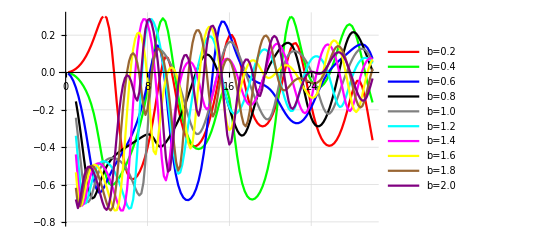

```mathematica
krange=30;
Show[{ListPlot[{Transpose[{v2b02[[All,1]],Re[v2b02[[All,2,1]]]}],Transpose[{v2b04[[All,1]],Re[v2b04[[All,2,1]]]}],Transpose[{v2b06[[All,1]],Re[v2b06[[All,2,1]]]}],v2b08,v2b10,
v2b12,v2b14,v2b16,v2b18,v2b20},PlotRange->{{0,krange},{-0.8,0.3}},GridLines->Automatic,PlotStyle->{{ -Graphics-},{ -Graphics-},{ -Graphics- },{ -Graphics-},{-Graphics-},{ -Graphics-},{ -Graphics-},{ -Graphics-},{-Graphics-},{-Graphics-}},PlotLegends->{"b=0.2","b=0.4","b=0.6","b=0.8","b=1.0","b=1.2","b=1.4","b=1.6","b=1.8","b=2.0"},Joined->{True,True,True,True,True,True}]}]
```

```mathematica
v2b05={{0.0,{0,0}},{0.25,{-0.002938456951618165,-3.227969362910863*^-14}},{0.5,{-0.011987824066760031,4.021660204770938*^-15}},{0.75,{-0.027489582231725585,8.067577996793252*^-15}},{1.,{-0.049673207241812956,3.7457278058170556*^-14}},{1.25,{-0.07869625093774192,4.2870529778493636*^-14}},{1.5,{-0.11478904521078691,-6.03559376280698*^-13}},{1.75,{-0.15842934307912632,-6.173773910246683*^-17}},{2.,{-0.21043098350362172,2.6165229794808745*^-12}},{2.25,{-0.27171803190915444,-1.0639704353256199*^-12}},{2.5,{-0.3424213924636071,-5.932366905386802*^-11}},{2.75,{-0.42002087871594707,3.5364066394616104*^-11}},{3.,{-0.4972644173674114,7.235656197835972*^-12}},{3.25,{-0.5625659954518619,-7.130386632890015*^-9}},{3.5,{-0.6052915303581592,1.429075244880441*^-9}},{3.75,{-0.622229811038092,-3.901792159801831*^-9}},{4.,{-0.6182392496499612,-5.810031857827077*^-10}},{4.25,{-0.6013312155951804,1.2410914177033694*^-9}},{4.5,{-0.5781947006714055,2.591036488672839*^-9}},{4.75,{-0.5528167865667997,-3.5724742528253544*^-11}},{5.,{-0.5269875405595194,1.4711164766567721*^-9}},{5.25,{-0.5011729300700416,3.0448173852832838*^-9}},{5.5,{-0.47516016706781816,1.0229195109058451*^-10}},{5.75,{-0.44841827713628524,-7.077047160566571*^-11}},{6.,{-0.4202732582450019,1.0341700744266162*^-8}},{6.25,{-0.38997600977083585,1.7961477004326268*^-8}},{6.5,{-0.3567243229875822,-3.0597698867327406*^-9}},{6.75,{-0.31966325403765633,-4.4427127965320826*^-11}},{7.,{-0.2778941132463203,-2.4725129555075954*^-11}},{7.25,{-0.23050225331506818,2.1669479279960272*^-10}},{7.5,{-0.17664645052466302,-2.857184168460874*^-10}},{7.75,{-0.11574605378782271,2.749796016498238*^-12}},{8.,{-0.04784975487476216,-1.5138502091204945*^-10}},{8.25,{0.025736206813392126,5.985774889844921*^-10}},{8.5,{0.10150396010825827,-3.034526798876663*^-10}},{8.75,{0.17266377415292417,1.7100070585176775*^-10}},{9.,{0.22858370821263108,-4.3947766735638886*^-8}},{9.25,{0.25609258011114033,-1.3577942013946665*^-10}},{9.5,{0.24376813124225763,1.8011667390216987*^-10}},{9.75,{0.18796068049512732,2.443819765897803*^-10}},{10.,{0.0961155046590976,-3.3259205346396855*^-9}},{10.25,{-0.016198636115687337,9.399263780996269*^-10}},{10.5,{-0.1323163786505354,-8.890644432841953*^-10}},{10.75,{-0.24002869160077248,1.5305942734158065*^-9}},{11.,{-0.3330770203432369,-8.738483812506843*^-11}},{11.25,{-0.4098181982931321,2.5941290659880895*^-8}},{11.5,{-0.4712182818271504,-5.937291443094876*^-11}},{11.75,{-0.5192966506380642,-1.6597701508670132*^-7}},{12.,{-0.5562297130208246,3.19913796332455*^-14}},{12.25,{-0.5839197756374604,-9.157520667061364*^-10}},{12.5,{-0.6038322299731614,-1.343316362613863*^-10}},{12.75,{-0.616938739945281,-5.778974454975404*^-9}},{13.,{-0.6236907488011718,8.207461138109764*^-9}},{13.25,{-0.6239606876578835,-9.897422901042853*^-9}},{13.5,{-0.6169306558236888,-9.211967437549099*^-9}},{13.75,{-0.600898490706012,-5.279470394331098*^-10}},{14.,{-0.5730402045432234,-8.644016844274223*^-9}},{14.25,{-0.5292864072794192,-1.7541721537659674*^-9}},{14.5,{-0.46489414819364877,1.0997562851990259*^-9}},{14.75,{-0.3769982399398858,-3.816230742360049*^-9}},{15.,{-0.2705239563846321,5.503309708162375*^-9}},{15.25,{-0.16460528020206439,-3.3806393546712467*^-9}},{15.5,{-0.08788904708786317,-3.762312300738782*^-9}},{15.75,{-0.05800704164081098,-3.556935692139046*^-9}},{16.,{-0.06878499876237988,2.062934171328411*^-9}},{16.25,{-0.10115685298071576,1.3120938534735412*^-9}},{16.5,{-0.13855980875570828,2.4672428806698927*^-8}},{16.75,{-0.17180854188517203,-1.5562444474266373*^-7}},{17.,{-0.1972233342729097,1.8411741660851327*^-8}},{17.25,{-0.21392374416189008,-1.3223419500324607*^-8}},{17.5,{-0.22212255068948256,-6.6979270358956116*^-9}},{17.75,{-0.2222999680169978,9.570631658988251*^-9}},{18.,{-0.21488978872445233,-6.141738387451158*^-8}},{18.25,{-0.20016656500021887,7.3993359427995766*^-9}},{18.5,{-0.17826266524096887,-2.051531306447595*^-9}},{18.75,{-0.14923729768525473,4.9508993423709655*^-9}},{19.,{-0.11309202110082736,-1.1638647567396398*^-8}},{19.25,{-0.07011799577754321,-3.761351753685475*^-9}},{19.5,{-0.020892587762830508,-9.865868821041999*^-9}},{19.75,{0.0333654135847543,-2.0406918145242254*^-9}},{20.,{0.09054919508087318,-4.2111091151572704*^-9}},{20.25,{0.1474907376861851,-1.2849954166925998*^-8}},{20.5,{0.19998117139037958,-2.5640980954645315*^-8}},{20.75,{0.24320861329078253,-8.280523303273963*^-9}},{21.,{0.27255893481872134,-2.5226475475485584*^-8}},{21.25,{0.28469436029987893,-2.4272839060842995*^-8}},{21.5,{0.2784054912830643,1.9457869988174764*^-8}},{21.75,{0.25490775461040893,-4.160105256434366*^-8}},{22.,{0.21736551866818704,-1.3881977661241984*^-8}},{22.25,{0.1699739612254904,-9.598707512117731*^-9}},{22.5,{0.11699320833341034,-3.669374258505795*^-8}},{22.75,{0.06207602029332124,2.7500516193429834*^-8}},{23.,{0.007946491096557571,-3.0161545891453254*^-8}},{23.25,{-0.04355143004388201,1.2544909730672001*^-8}},{23.5,{-0.09135122158518404,-1.5965272568449384*^-8}},{23.75,{-0.1349185339976241,4.4787391737088*^-9}},{24.,{-0.1740747105500865,-2.1685916430472374*^-8}},{24.25,{-0.2088164716941053,5.945354450993786*^-8}},{24.5,{-0.23921346247044006,-8.451316743334802*^-8}},{24.75,{-0.26531013508033774,3.696442765741613*^-8}},{25.,{-0.2870718920558613,-1.982937774962435*^-8}},{25.25,{-0.3043539998608062,-8.214450833884019*^-7}},{25.5,{-0.3169030155488351,3.5490647835805426*^-9}},{25.75,{-0.32440659814461154,-4.231005868012933*^-9}},{26.,{-0.32660082331163026,-2.8515596397540252*^-8}},{26.25,{-0.32340471380143204,6.474789017690802*^-9}},{26.5,{-0.3150826770163598,-3.3113331079062216*^-7}},{26.75,{-0.3023062513223777,-1.4864711701082616*^-8}},{27.,{-0.2861269844674669,-1.1795391829366478*^-8}},{27.25,{-0.2677348114431766,3.282280327578398*^-8}},{27.5,{-0.24823422412547339,2.3198299137986173*^-8}},{27.75,{-0.22843160822556385,-6.876367485812016*^-7}},{28.,{-0.20873437925488786,-4.389104128178838*^-8}},{28.25,{-0.18926088681205128,-4.57545510406416*^-8}},{28.5,{-0.16984608245571084,-4.89879500666019*^-7}},{28.75,{-0.150243172068624,1.1606970894045416*^-7}},{29.,{-0.13017560847174398,6.184682738605995*^-8}},{29.25,{-0.1094092617836425,-1.7099873299410834*^-8}},{29.5,{-0.08784106737906038,1.6594349754732864*^-8}},{29.75,{-0.06547879208912809,-2.8935991268561376*^-7}},{30.,{-0.04254995956358663,3.993520295392406*^-8}}};
v2b15={{0.0,{0.0,0.0}},{0.25,{-0.015370303774242809,1.7769218865201226*^-14}},{0.5,{-0.062033854653153135,1.1044824126021148*^-13}},{0.75,{-0.13895894530129987,1.1746760402533138*^-12}},{1.,{-0.24227284840377084,-3.705584516153792*^-13}},{1.25,{-0.36479685257132444,2.03300275408307*^-10}},{1.5,{-0.4935462545338007,-1.3736245507186947*^-13}},{1.75,{-0.6066027342700241,3.5199298986767468*^-12}},{2.,{-0.677615358940052,-7.854719824280913*^-17}},{2.25,{-0.6931901738297919,2.5515907936889136*^-9}},{2.5,{-0.6649321089100702,-1.6542396658808482*^-11}},{2.75,{-0.6173983354122009,3.1894069697736614*^-10}},{3.,{-0.5697384783058826,-1.9024686676086125*^-11}},{3.25,{-0.5304853678478362,-1.8187476613841656*^-8}},{3.5,{-0.5012655434825574,2.362139232379727*^-12}},{3.75,{-0.4809341348538826,7.728655260097078*^-11}},{4.,{-0.46776639040835283,2.4043099076459743*^-12}},{4.25,{-0.4602694766355951,2.2842938117113635*^-9}},{4.5,{-0.45737709848908636,-2.6459958623624444*^-10}},{4.75,{-0.45842964327899915,-7.484851498416402*^-9}},{5.,{-0.46310779021610066,-1.3712534670396533*^-9}},{5.25,{-0.47137016379617547,3.4480297702592567*^-9}},{5.5,{-0.48340462829858677,-1.3064862821084218*^-16}},{5.75,{-0.4995850244361453,1.423344748949777*^-11}},{6.,{-0.5204009405259216,2.7476150804417533*^-10}},{6.25,{-0.5462945270855182,2.533566513832376*^-15}},{6.5,{-0.5772326695516907,-1.9307243431914002*^-15}},{6.75,{-0.611624941261184,-1.145481241545447*^-11}},{7.,{-0.6437578704106229,-2.4689414366078834*^-11}},{7.25,{-0.6586511454450078,-2.2671543457063428*^-10}},{7.5,{-0.6260948798292884,-2.906903758874852*^-10}},{7.75,{-0.5094436060825578,-2.8274905450754082*^-9}},{8.,{-0.3127001568032249,-1.4984272522717237*^-10}},{8.25,{-0.11002346166297973,1.76213080455171*^-8}},{8.5,{0.029396586686098465,7.266637614962103*^-9}},{8.75,{0.09911283511377558,5.15503078078277*^-8}},{9.,{0.12317100288371782,-6.3826171831989315*^-9}},{9.25,{0.12301824022670999,-9.50091362653667*^-10}},{9.5,{0.1109669876096405,2.620381383439199*^-10}},{9.75,{0.09293238374440915,-1.3441154978021209*^-9}},{10.,{0.07130896973595931,8.47169445824443*^-9}},{10.25,{0.04672958171071315,4.33892282797973*^-8}},{10.5,{0.018929582991274403,4.932907672318059*^-8}},{10.75,{-0.012780556695824017,3.4346509102841225*^-9}},{11.,{-0.04914309652831915,-8.798252620692403*^-10}},{11.25,{-0.090576688316893,6.4626269237177645*^-9}},{11.5,{-0.136708521058601,-1.1033906130299018*^-8}},{11.75,{-0.18581935335879288,1.566971093523524*^-8}},{12.,{-0.23448917168911598,9.497906648349837*^-10}},{12.25,{-0.27779716282642714,-1.8093309951838823*^-8}},{12.5,{-0.3103659708978077,3.042438163936668*^-8}},{12.75,{-0.32794959786110156,1.952688159417017*^-8}},{13.,{-0.3286914992406541,7.783544369806296*^-10}},{13.25,{-0.3133057245055995,-3.291125763139785*^-8}},{13.5,{-0.2842418950802804,-3.7066213982523582*^-9}},{13.75,{-0.24454795541806823,4.249484658791227*^-9}},{14.,{-0.19705760854870333,9.232773458052011*^-8}},{14.25,{-0.14413238248873098,-6.4626660365719775*^-9}},{14.5,{-0.08782837791280503,9.054399528965831*^-9}},{14.75,{-0.030295842098810748,-1.0398767252133559*^-8}},{15.,{0.025786526327060313,-4.4146709066272754*^-9}},{15.25,{0.07698661849629682,-7.501192091078092*^-10}},{15.5,{0.11931185030441603,-1.6320169373384063*^-7}},{15.75,{0.14894312415829705,-3.9811813532938125*^-8}},{16.,{0.16331182862433666,6.775642060945504*^-9}},{16.25,{0.16195530127928567,1.0904008548060991*^-8}},{16.5,{0.14665473514453153,2.3944201313874438*^-8}},{16.75,{0.1206284574361209,8.18726790090496*^-9}},{17.,{0.08757222390690272,-2.4154818888100097*^-8}},{17.25,{0.05069788314207085,5.209228323515558*^-9}},{17.5,{0.012356457924273449,-8.492074884500232*^-9}},{17.75,{-0.025992938167556212,3.2205245879034055*^-8}},{18.,{-0.0635915975354855,-7.180941484215929*^-8}},{18.25,{-0.10009379366472551,-5.7629362680555393*^-8}},{18.5,{-0.13528958020224263,1.2843834481107857*^-8}},{18.75,{-0.16880500291898254,3.0828820042084766*^-8}},{19.,{-0.1997420713822689,1.2841134839065155*^-8}},{19.25,{-0.22627881062030591,-8.61930011278599*^-9}},{19.5,{-0.2452172603062858,-1.6140369547695166*^-8}},{19.75,{-0.25186087080652686,-2.6623312486213505*^-8}},{20.,{-0.24083540469107942,1.907883119889603*^-8}},{20.25,{-0.20853636764698505,-1.9073111494478228*^-8}},{20.5,{-0.1565706658835486,2.3200394321981184*^-8}},{20.75,{-0.09311662767328212,-1.6078359424170658*^-9}},{21.,{-0.02964418925000249,4.008578860586756*^-8}},{21.25,{0.02450334873765068,1.836253019961593*^-8}},{21.5,{0.06505843044393464,-1.7130306603637772*^-8}},{21.75,{0.09202558699541653,3.627621394360486*^-9}},{22.,{0.10750560900676612,-5.252652172720938*^-8}},{22.25,{0.11397008494126462,-1.0340229048122765*^-8}},{22.5,{0.11346574600033521,-3.85159791992006*^-8}},{22.75,{0.10739191788629823,-9.994343755065057*^-8}},{23.,{0.09648263405551326,-1.8618768637936514*^-7}},{23.25,{0.0809875810098753,8.222807097935609*^-8}},{23.5,{0.06069747547032684,-1.9006903612493493*^-7}},{23.75,{0.035224072437261875,-1.9335605736010814*^-7}},{24.,{0.004120000250285188,3.497660527738634*^-7}},{24.25,{-0.03274223117264212,1.2418090260350386*^-10}},{24.5,{-0.074589548795838,3.2636615680707444*^-7}},{24.75,{-0.11906174069597159,5.446074673066934*^-8}},{25.,{-0.16174085280010547,-1.6816166733325572*^-7}},{25.25,{-0.19657752903538464,-1.1347595581348781*^-7}},{25.5,{-0.21760115667704305,1.0728266843237122*^-7}},{25.75,{-0.22135530947741341,-4.879233309556845*^-7}},{26.,{-0.20822656367240502,1.218161122109372*^-7}},{26.25,{-0.18184339390327633,-6.590028213718615*^-8}},{26.5,{-0.14704513769213645,2.415876776269508*^-7}},{26.75,{-0.10816248250822058,8.392993596909107*^-8}},{27.,{-0.06843004873430975,1.2877566638553538*^-7}},{27.25,{-0.02980228240468462,1.6271806740265945*^-7}},{27.5,{0.00651692447581312,-4.517788570104052*^-7}},{27.75,{0.03971106544028546,2.12269775634385*^-7}},{28.,{0.06904811337710506,5.043033016240346*^-8}},{28.25,{0.09364864844663295,1.0184164896006994*^-7}},{28.5,{0.11241161213775382,2.2229187005210472*^-7}},{28.75,{0.12409777221326003,2.1753433556520006*^-7}},{29.,{0.12752226221839869,-1.6267679742047877*^-7}},{29.25,{0.1218927091839019,8.594358628600922*^-8}},{29.5,{0.10716956129891317,-1.0837082157693481*^-7}},{29.75,{0.08426817499022542,1.8723369294340568*^-8}},{30.,{0.05501261160481038,-4.3629956338177634*^-7}}};
```

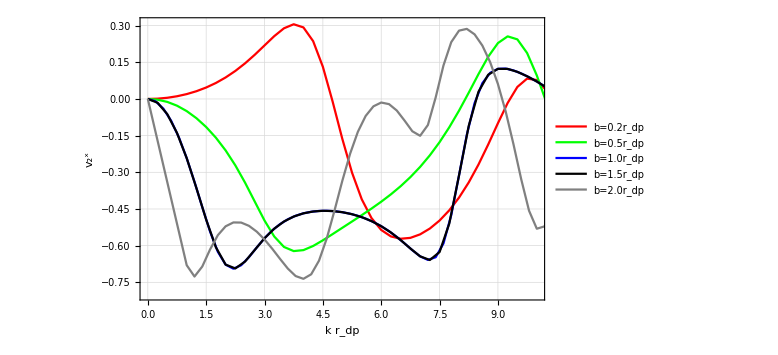

```mathematica
krange=10;
ListLinePlot[{Transpose[{v2b02[[All,1]],Re[v2b02[[All,2,1]]]}],Transpose[{v2b05[[All,1]],Re[v2b05[[All,2,1]]]}],v2b10,
Transpose[{v2b15[[All,1]],Re[v2b15[[All,2,1]]]}],v2b20},PlotRange->{{0,krange},{-0.8,0.31}},GridLines->Automatic,PlotStyle->{{ -Graphics-},{ -Graphics-},{ -Graphics- },{ -Graphics-},{-Graphics-},{ -Graphics-},{ -Graphics-},{ -Graphics-},{-Graphics-},{-Graphics-}},PlotLegends->Placed[{"b=0.2r_dp","b=0.5r_dp","b=1.0r_dp","b=1.5r_dp","b=2.0r_dp"},{0.35,0.6}],Joined->{True,True,True,True,True,True},ImageSize->Large,InterpolationOrder->1,Frame->True,FrameLabel->{"k r_dp","v_2^x"}]
```

## b = 2, ϕ_B=π/2

```mathematica
v2phiA0={{0.,{0.,0.}},{0.25,{0.09146919792496272,-2.2581923611415398*^-15}},{0.5,{0.21995120543294477,8.452979671503303*^-16}},{0.75,{0.3386476425219818,1.1500915780478749*^-10}},{1.,{0.4238277545692831,-3.445367384658075*^-12}},{1.25,{0.45409280721394646,-8.140223292825205*^-12}},{1.5,{0.41735111525866275,2.1943283071298817*^-16}},{1.75,{0.3186082616535235,4.553575904226687*^-16}},{2.,{0.17947706116692377,2.5918266957901536*^-8}},{2.25,{0.02834760833475813,5.466367324468412*^-11}},{2.5,{-0.11098892551573651,-2.787215017710036*^-16}},{2.75,{-0.2249545252279186,-6.3144157307026585*^-9}},{3.,{-0.3095601644575039,-2.0693532151326373*^-10}},{3.25,{-0.3670054690426072,-1.6335827209216845*^-16}},{3.5,{-0.4023550731892407,5.095832943530613*^-10}},{3.75,{-0.4213016870316593,-4.3050805288791556*^-10}},{4.,{-0.4289231533107918,6.390347602382924*^-10}},{4.25,{-0.4290647933333928,-4.692878234663909*^-16}},{4.5,{-0.4240604428132446,4.497476397361143*^-16}},{4.75,{-0.4146620543163549,5.223272504152629*^-9}},{5.,{-0.40026354735956576,-5.733662379860269*^-13}},{5.25,{-0.3795476673542695,-1.6986277980524815*^-10}},{5.5,{-0.35159899244298437,3.324276248259424*^-8}},{5.75,{-0.31711781459263544,-1.6118194204074167*^-7}},{6.,{-0.27905355422500505,6.336982807369349*^-10}},{6.25,{-0.24191908871741286,6.01736252089637*^-8}},{6.5,{-0.21039218509975127,4.318634851181344*^-16}},{6.75,{-0.18751427509906013,-5.832749296028698*^-15}},{7.,{-0.17360214796769102,2.3676584442834*^-9}},{7.25,{-0.16598585699049906,-1.8705810006545222*^-9}},{7.5,{-0.15976643127569293,2.0516605606730965*^-7}},{7.75,{-0.14957975809416907,1.803961757646834*^-7}},{8.,{-0.13184519302239694,-1.3908831053183841*^-15}},{8.25,{-0.10633465743761585,2.5672438518402253*^-9}},{8.5,{-0.07613099972085632,-3.2140833011764754*^-9}},{8.75,{-0.04607615386559864,-1.086908944659777*^-8}},{9.,{-0.02085430503802848,1.1718022101726447*^-8}},{9.25,{-0.003604290728582811,-7.594337540493211*^-9}},{9.5,{0.00452247663559456,-7.913934036024441*^-9}},{9.75,{0.004264485559515954,3.110908194110354*^-8}},{10.,{-0.002474822126193022,-3.0320611329481948*^-9}},{10.25,{-0.013413106602082307,1.240698832434495*^-7}},{10.5,{-0.026580414948384066,-2.7861769552798713*^-8}},{10.75,{-0.04085658682130254,-2.564396074994179*^-8}},{11.,{-0.055915834865355146,6.05461615887009*^-15}},{11.25,{-0.07195320441419809,1.4233482259854649*^-8}},{11.5,{-0.08910973983780643,-5.146071728823905*^-8}},{11.75,{-0.10685944086480252,-7.893682911615357*^-9}},{12.,{-0.12349897252628375,-1.3332185449974222*^-9}},{12.25,{-0.13599761271132244,-1.2998379030384888*^-8}},{12.5,{-0.1405785542306192,-5.7852106653732936*^-8}},{12.75,{-0.1341341940261409,7.356999287812868*^-8}},{13.,{-0.11609610830432124,-6.639473382535551*^-8}},{13.25,{-0.08923108581333812,-1.0354994762543256*^-7}},{13.5,{-0.05889461510944208,-1.8300802720522332*^-8}},{13.75,{-0.030863921470455098,-2.5124443836722147*^-7}},{14.,{-0.009472541806490768,-2.4830586482469347*^-7}},{14.25,{0.0034667917651867663,-1.4905970983474445*^-7}},{14.5,{0.008489065861758308,-3.2896180204513885*^-8}},{14.75,{0.007681989500205423,1.3231159463880484*^-8}},{15.,{0.003985775802518194,2.199357251561524*^-7}},{15.25,{-0.00013109228935277524,-9.675686713248897*^-8}},{15.5,{-0.003038535803150367,1.567122896091707*^-7}},{15.75,{-0.004339150952803433,3.373667972240891*^-7}},{16.,{-0.004587224556757001,-4.5060830840881006*^-7}},{16.25,{-0.004790488994901545,-5.483619645924592*^-7}},{16.5,{-0.0058779641862182035,6.82073008514158*^-7}},{16.75,{-0.008412728434136955,-5.879476775802974*^-7}},{17.,{-0.012172851979255949,1.8546282579525514*^-7}},{17.25,{-0.01649098187157544,-2.353829395203327*^-7}},{17.5,{-0.020527971935869853,1.7285327060197135*^-7}},{17.75,{-0.023764942460127416,-5.114203604328846*^-8}},{18.,{-0.02636270253929486,-1.8253014588648097*^-7}},{18.25,{-0.02905970189122761,-9.944039524020384*^-8}},{18.5,{-0.03307155066527271,-3.4030403661326914*^-7}},{18.75,{-0.039374054221357445,-3.097730197052933*^-8}},{19.,{-0.048193037386635065,1.9953514421754806*^-7}},{19.25,{-0.05860323240023341,4.90617965263513*^-7}},{19.5,{-0.06824115886418766,-7.771860794785417*^-7}},{19.75,{-0.07408308345704336,-9.753730273992618*^-7}},{20.,{-0.07312770520915575,1.229900166447747*^-6}},{20.25,{-0.06399662445416167,-1.2763848897637094*^-6}},{20.5,{-0.04753289847353494,9.46712705707675*^-7}},{20.75,{-0.026809093063894333,-2.8218582358168225*^-6}},{21.,{-0.00555359670677935,-7.188672183148672*^-7}},{21.25,{0.012727441832681334,-1.7079851389832565*^-6}},{21.5,{0.02591407415735143,3.435795120771429*^-6}},{21.75,{0.03328409201369886,3.37335020501702*^-6}},{22.,{0.03525877736018231,3.849058319359097*^-6}},{22.25,{0.03307528850904369,1.8052794758595414*^-6}},{22.5,{0.028074538890620587,6.3044061664015934*^-6}},{22.75,{0.02135095980981245,4.887015960254118*^-7}},{23.,{0.013644976153906276,1.3474068461559003*^-7}},{23.25,{0.005049101638952906,-9.320040333027921*^-7}},{23.5,{-0.004635392498889649,5.668494812383923*^-6}},{23.75,{-0.015489136285684971,1.9267651086958564*^-7}},{24.,{-0.02713871839437648,-2.878722374506093*^-6}},{24.25,{-0.03873331403011905,5.4894617500192675*^-6}},{24.5,{-0.048399180549132725,2.0990445392660243*^-6}},{24.75,{-0.05419431114151648,-0.000010647133212175547}},{25.,{-0.05468473340591535,-4.516655916633917*^-6}},{25.25,{-0.049651024680852786,1.2737187881281575*^-6}},{25.5,{-0.04026672507639463,-1.7477359655625428*^-7}},{25.75,{-0.029155493584620423,-3.611680612452598*^-6}},{26.,{-0.018688147258733787,-9.007872396378987*^-7}},{26.25,{-0.011242746099510372,2.7615000863335203*^-6}},{26.5,{-0.007495737204308013,-2.182993200358714*^-6}},{26.75,{-0.0070185257026036466,-8.725699777577732*^-7}},{27.,{-0.008420406090512611,0.000011617044661436481}},{27.25,{-0.009771864392151226,0.00001029230129967063}},{27.5,{-0.009225185299816538,6.52151524636639*^-6}},{27.75,{-0.006242662232116619,5.7219643697726925*^-6}},{28.,{-0.000997513052025345,4.368624407822899*^-6}},{28.25,{0.005571695129032311,-3.1909410745837876*^-7}},{28.5,{0.011980215616756192,-3.898029417664754*^-6}},{28.75,{0.016882342352572008,-1.2159236551419824*^-6}},{29.,{0.01937165115592786,2.5473606618769585*^-6}},{29.25,{0.019507799354367833,-0.000012187827153509412}},{29.5,{0.017147189475852687,-4.578683406499601*^-6}},{29.75,{0.014192667371940955,0.00010003065812282889}},{30.,{0.0098296435926415,4.087619622600124*^-6}}};
```

## b =2

```mathematica
phA0={{0.,{0.,0.}},{0.25,{0.09146919792496272,-2.2581923611415398*^-15}},{0.5,{0.21995120543294477,8.452979671503303*^-16}},{0.75,{0.3386476425219818,1.1500915780478749*^-10}},{1.,{0.4238277545692831,-3.445367384658075*^-12}},{1.25,{0.45409280721394646,-8.140223292825205*^-12}},{1.5,{0.41735111525866275,2.1943283071298817*^-16}},{1.75,{0.3186082616535235,4.553575904226687*^-16}},{2.,{0.17947706116692377,2.5918266957901536*^-8}},{2.25,{0.02834760833475813,5.466367324468412*^-11}},{2.5,{-0.11098892551573651,-2.787215017710036*^-16}},{2.75,{-0.2249545252279186,-6.3144157307026585*^-9}},{3.,{-0.3095601644575039,-2.0693532151326373*^-10}},{3.25,{-0.3670054690426072,-1.6335827209216845*^-16}},{3.5,{-0.4023550731892407,5.095832943530613*^-10}},{3.75,{-0.4213016870316593,-4.3050805288791556*^-10}},{4.,{-0.4289231533107918,6.390347602382924*^-10}},{4.25,{-0.4290647933333928,-4.692878234663909*^-16}},{4.5,{-0.4240604428132446,4.497476397361143*^-16}},{4.75,{-0.4146620543163549,5.223272504152629*^-9}},{5.,{-0.40026354735956576,-5.733662379860269*^-13}},{5.25,{-0.3795476673542695,-1.6986277980524815*^-10}},{5.5,{-0.35159899244298437,3.324276248259424*^-8}},{5.75,{-0.31711781459263544,-1.6118194204074167*^-7}},{6.,{-0.27905355422500505,6.336982807369349*^-10}},{6.25,{-0.24191908871741286,6.01736252089637*^-8}},{6.5,{-0.21039218509975127,4.318634851181344*^-16}},{6.75,{-0.18751427509906013,-5.832749296028698*^-15}},{7.,{-0.17360214796769102,2.3676584442834*^-9}},{7.25,{-0.16598585699049906,-1.8705810006545222*^-9}},{7.5,{-0.15976643127569293,2.0516605606730965*^-7}},{7.75,{-0.14957975809416907,1.803961757646834*^-7}},{8.,{-0.13184519302239694,-1.3908831053183841*^-15}},{8.25,{-0.10633465743761585,2.5672438518402253*^-9}},{8.5,{-0.07613099972085632,-3.2140833011764754*^-9}},{8.75,{-0.04607615386559864,-1.086908944659777*^-8}},{9.,{-0.02085430503802848,1.1718022101726447*^-8}},{9.25,{-0.003604290728582811,-7.594337540493211*^-9}},{9.5,{0.00452247663559456,-7.913934036024441*^-9}},{9.75,{0.004264485559515954,3.110908194110354*^-8}},{10.,{-0.002474822126193022,-3.0320611329481948*^-9}},{10.25,{-0.013413106602082307,1.240698832434495*^-7}},{10.5,{-0.026580414948384066,-2.7861769552798713*^-8}},{10.75,{-0.04085658682130254,-2.564396074994179*^-8}},{11.,{-0.055915834865355146,6.05461615887009*^-15}},{11.25,{-0.07195320441419809,1.4233482259854649*^-8}},{11.5,{-0.08910973983780643,-5.146071728823905*^-8}},{11.75,{-0.10685944086480252,-7.893682911615357*^-9}},{12.,{-0.12349897252628375,-1.3332185449974222*^-9}},{12.25,{-0.13599761271132244,-1.2998379030384888*^-8}},{12.5,{-0.1405785542306192,-5.7852106653732936*^-8}},{12.75,{-0.1341341940261409,7.356999287812868*^-8}},{13.,{-0.11609610830432124,-6.639473382535551*^-8}},{13.25,{-0.08923108581333812,-1.0354994762543256*^-7}},{13.5,{-0.05889461510944208,-1.8300802720522332*^-8}},{13.75,{-0.030863921470455098,-2.5124443836722147*^-7}},{14.,{-0.009472541806490768,-2.4830586482469347*^-7}},{14.25,{0.0034667917651867663,-1.4905970983474445*^-7}},{14.5,{0.008489065861758308,-3.2896180204513885*^-8}},{14.75,{0.007681989500205423,1.3231159463880484*^-8}},{15.,{0.003985775802518194,2.199357251561524*^-7}},{15.25,{-0.00013109228935277524,-9.675686713248897*^-8}},{15.5,{-0.003038535803150367,1.567122896091707*^-7}},{15.75,{-0.004339150952803433,3.373667972240891*^-7}},{16.,{-0.004587224556757001,-4.5060830840881006*^-7}},{16.25,{-0.004790488994901545,-5.483619645924592*^-7}},{16.5,{-0.0058779641862182035,6.82073008514158*^-7}},{16.75,{-0.008412728434136955,-5.879476775802974*^-7}},{17.,{-0.012172851979255949,1.8546282579525514*^-7}},{17.25,{-0.01649098187157544,-2.353829395203327*^-7}},{17.5,{-0.020527971935869853,1.7285327060197135*^-7}},{17.75,{-0.023764942460127416,-5.114203604328846*^-8}},{18.,{-0.02636270253929486,-1.8253014588648097*^-7}},{18.25,{-0.02905970189122761,-9.944039524020384*^-8}},{18.5,{-0.03307155066527271,-3.4030403661326914*^-7}},{18.75,{-0.039374054221357445,-3.097730197052933*^-8}},{19.,{-0.048193037386635065,1.9953514421754806*^-7}},{19.25,{-0.05860323240023341,4.90617965263513*^-7}},{19.5,{-0.06824115886418766,-7.771860794785417*^-7}},{19.75,{-0.07408308345704336,-9.753730273992618*^-7}},{20.,{-0.07312770520915575,1.229900166447747*^-6}},{20.25,{-0.06399662445416167,-1.2763848897637094*^-6}},{20.5,{-0.04753289847353494,9.46712705707675*^-7}},{20.75,{-0.026809093063894333,-2.8218582358168225*^-6}},{21.,{-0.00555359670677935,-7.188672183148672*^-7}},{21.25,{0.012727441832681334,-1.7079851389832565*^-6}},{21.5,{0.02591407415735143,3.435795120771429*^-6}},{21.75,{0.03328409201369886,3.37335020501702*^-6}},{22.,{0.03525877736018231,3.849058319359097*^-6}},{22.25,{0.03307528850904369,1.8052794758595414*^-6}},{22.5,{0.028074538890620587,6.3044061664015934*^-6}},{22.75,{0.02135095980981245,4.887015960254118*^-7}},{23.,{0.013644976153906276,1.3474068461559003*^-7}},{23.25,{0.005049101638952906,-9.320040333027921*^-7}},{23.5,{-0.004635392498889649,5.668494812383923*^-6}},{23.75,{-0.015489136285684971,1.9267651086958564*^-7}},{24.,{-0.02713871839437648,-2.878722374506093*^-6}},{24.25,{-0.03873331403011905,5.4894617500192675*^-6}},{24.5,{-0.048399180549132725,2.0990445392660243*^-6}},{24.75,{-0.05419431114151648,-0.000010647133212175547}},{25.,{-0.05468473340591535,-4.516655916633917*^-6}},{25.25,{-0.049651024680852786,1.2737187881281575*^-6}},{25.5,{-0.04026672507639463,-1.7477359655625428*^-7}},{25.75,{-0.029155493584620423,-3.611680612452598*^-6}},{26.,{-0.018688147258733787,-9.007872396378987*^-7}},{26.25,{-0.011242746099510372,2.7615000863335203*^-6}},{26.5,{-0.007495737204308013,-2.182993200358714*^-6}},{26.75,{-0.0070185257026036466,-8.725699777577732*^-7}},{27.,{-0.008420406090512611,0.000011617044661436481}},{27.25,{-0.009771864392151226,0.00001029230129967063}},{27.5,{-0.009225185299816538,6.52151524636639*^-6}},{27.75,{-0.006242662232116619,5.7219643697726925*^-6}},{28.,{-0.000997513052025345,4.368624407822899*^-6}},{28.25,{0.005571695129032311,-3.1909410745837876*^-7}},{28.5,{0.011980215616756192,-3.898029417664754*^-6}},{28.75,{0.016882342352572008,-1.2159236551419824*^-6}},{29.,{0.01937165115592786,2.5473606618769585*^-6}},{29.25,{0.019507799354367833,-0.000012187827153509412}},{29.5,{0.017147189475852687,-4.578683406499601*^-6}},{29.75,{0.014192667371940955,0.00010003065812282889}},{30.,{0.0098296435926415,4.087619622600124*^-6}}};
phApio4={{0.,{0.,0.}},{0.25,{-0.05159237403311763,-0.02144134618829293}},{0.5,{-0.13141400923891716,-0.0670045773290171}},{0.75,{-0.14949173522977507,-0.08985151796046552}},{1.,{-0.1168277262018376,-0.058810446246397446}},{1.25,{-0.08911448100541623,0.022914099102275497}},{1.5,{-0.10174872767228778,0.124469002515214}},{1.75,{-0.1527905887221794,0.21175930079939462}},{2.,{-0.2221830176129219,0.2677653461746158}},{2.25,{-0.2926674346358879,0.2918845377828226}},{2.5,{-0.3554464406883236,0.29047478574874724}},{2.75,{-0.4075263107893066,0.2707480650304021}},{3.,{-0.4484395972768003,0.23897133221399433}},{3.25,{-0.4784161041941461,0.2006101168701738}},{3.5,{-0.49771024270379804,0.16085207718380928}},{3.75,{-0.5065540504109788,0.12487907893089417}},{4.,{-0.5053743638143103,0.09763632954906254}},{4.25,{-0.4950173491154723,0.08302698871179055}},{4.5,{-0.4767670430110061,0.08264682255897313}},{4.75,{-0.45198102416379293,0.0944458862667056}},{5.,{-0.4213693146855106,0.1119513053670713}},{5.25,{-0.38423766857248554,0.12481777154738158}},{5.5,{-0.3383387199708303,0.12138727532659506}},{5.75,{-0.28109752320152237,0.09331707061603697}},{6.,{-0.21210570811008633,0.04055078991035308}},{6.25,{-0.13560035129697587,-0.026809660376055828}},{6.5,{-0.06048122565627909,-0.09232718621856169}},{6.75,{0.002352321983818347,-0.1406273045324728}},{7.,{0.043346457685669394,-0.16290901200189814}},{7.25,{0.05604152440256224,-0.15770490542197893}},{7.5,{0.03724570250787317,-0.12860127941019736}},{7.75,{-0.012455224135475677,-0.08196135534967525}},{8.,{-0.08589959776136274,-0.026332129361321264}},{8.25,{-0.1645781649792778,0.027115491989577856}},{8.5,{-0.21887708745644135,0.06616012159741386}},{8.75,{-0.22374220651751794,0.08378903383913552}},{9.,{-0.18030313124147926,0.08363625415930037}},{9.25,{-0.11370444375509164,0.07577561768389654}},{9.5,{-0.05054232237221179,0.06828819020409932}},{9.75,{-0.0059062789876302224,0.06392504777284787}},{10.,{0.015566749938093831,0.06211661855645581}},{10.25,{0.014308676340128692,0.06109594514894554}},{10.5,{-0.007254273368477608,0.05905913374649266}},{10.75,{-0.04551287779683056,0.054634792795135424}},{11.,{-0.09483127432541777,0.04718671817987134}},{11.25,{-0.14597447151332316,0.03706056666164817}},{11.5,{-0.1854944888879892,0.025749977233371538}},{11.75,{-0.19888965031688532,0.015313534192584145}},{12.,{-0.17832289384383543,0.006861675749268092}},{12.25,{-0.12912887305790488,-0.0008819006165092101}},{12.5,{-0.06702062191732035,-0.01118061815969376}},{12.75,{-0.008083303156426754,-0.026912519112568686}},{13.,{0.038102498672509574,-0.048786739024373256}},{13.25,{0.06911055920207038,-0.07423618550590932}},{13.5,{0.08690731878921637,-0.09790274291796107}},{13.75,{0.09473134749425585,-0.11276546995588858}},{14.,{0.09493021993181654,-0.11257753359533844}},{14.25,{0.08780983989202636,-0.09425834756671699}},{14.5,{0.07181260958046504,-0.05930328561978325}},{14.75,{0.044531951525726726,-0.013394767939173415}},{15.,{0.004451019907570294,0.035479479137521634}},{15.25,{-0.04724865495570123,0.07858976154298426}},{15.5,{-0.10467475362626137,0.10787139470065661}},{15.75,{-0.15629747159012333,0.11754371306372018}},{16.,{-0.1869508614653505,0.10649205715847136}},{16.25,{-0.18472361727544084,0.08009848196578423}},{16.5,{-0.14869924582395322,0.048699148215278494}},{16.75,{-0.0902404327493381,0.02243259184267968}},{17.,{-0.026099284158392952,0.0066725711305426535}},{17.25,{0.02929858397623724,0.001560502762259992}},{17.5,{0.0669581292329788,0.004314621631038753}},{17.75,{0.08225240500407868,0.011156236576354558}},{18.,{0.07314051911650489,0.018346839358197798}},{18.25,{0.03939157016375083,0.02211649743448083}},{18.5,{-0.015815438163459334,0.0187Readv2x[v2b02_]:=Transpose[{v2b02[[All,1]],Re[v2b02[[All,2,1]]]}]
Readv2x[v2b02_,n_]:=Transpose[{v2b02[[All,1]],Re[v2b02[[All,2,n]]]}]
SetDirectory[NotebookDirectory[]]6919990824511}},{18.75,{-0.08160224248743325,0.005181991725917837}},{19.,{-0.13616870311675783,-0.019015232876958093}},{19.25,{-0.15260269035597948,-0.04840889198636366}},{19.5,{-0.1200862121764171,-0.07341542852881519}},{19.75,{-0.05530540657029094,-0.08702380408293724}},{20.,{0.01346890649892937,-0.0888933726846251}},{20.25,{0.06571032831342186,-0.08259983620125932}},{20.5,{0.0942143420506589,-0.07122553183728846}},{20.75,{0.09893009452311506,-0.056053009260317574}},{21.,{0.08362648469984765,-0.036872931749464724}},{21.25,{0.05429280644978561,-0.013297067846834548}},{21.5,{0.0179328735980233,0.01475861411511888}},{21.75,{-0.01716578640456289,0.04502612864735422}},{22.,{-0.044455437382354454,0.07302749613483434}},{22.25,{-0.06139726272888189,0.0934303963499998}},{22.5,{-0.06987207437498567,0.1020919809919513}},{22.75,{-0.07404611556044563,0.09722509701353724}},{23.,{-0.07752322752665249,0.07965279739969401}},{23.25,{-0.08141952740975837,0.0524095704691305}},{23.5,{-0.08365032663828886,0.02008920437270143}},{23.75,{-0.07984205617911701,-0.01134345323785288}},{24.,{-0.06527117136508964,-0.03554732933938745}},{24.25,{-0.037831435826455886,-0.04764400410588823}},{24.5,{-0.00012251735713010893,-0.04634848892773221}},{24.75,{0.040933555126086554,-0.034499734210102814}},{25.,{0.07651980785347834,-0.017769234731716353}},{25.25,{0.09870492302021758,-0.0023617202164091205}},{25.5,{0.10191513226563827,0.006325556809989832}},{25.75,{0.08413520805990089,0.004870058748485201}},{26.,{0.047420055790109515,-0.007632680265796094}},{26.25,{-0.00043670557891387004,-0.02895747124893974}},{26.5,{-0.046070502771614855,-0.052568444800250295}},{26.75,{-0.07416101380045274,-0.07002986208315427}},{27.,{-0.07621545995373163,-0.07408625718477119}},{27.25,{-0.05597795371591994,-0.06405081302482106}},{27.5,{-0.02514059845920075,-0.04351845272835839}},{27.75,{0.004199443079984063,-0.01793629317580627}},{28.,{0.02378383761185883,0.008357683027229166}},{28.25,{0.02975099276645291,0.032696527326253534}},{28.5,{0.022049296870250097,0.05372902940886547}},{28.75,{0.0034281356344875833,0.07012836219174233}},{29.,{-0.020611985424221553,0.04375291587404278}},{29.25,{-0.042872292508935234,0.08369119804015959}},{29.5,{-0.05673424277722168,0.07820399007768293}},{29.75,{-0.05854196280335238,0.04591310807780729}},{30.,{-0.049258741418514614,0.02584917673465226}}};
phApio2={{0.,{0.,0.}},{0.25,{-0.0629432274197984,-5.868761532593917*^-14}},{0.5,{-0.24189847126191777,-9.807338549622004*^-14}},{0.75,{-0.48454430255054526,-2.2660032888819035*^-12}},{1.,{-0.6800785363396216,7.439811975583693*^-17}},{1.25,{-0.7220912766079244,2.971052049603001*^-16}},{1.5,{-0.6507318308882671,-4.066801040376059*^-17}},{1.75,{-0.56982123547443,7.270017790425521*^-9}},{2.,{-0.5208747233243992,-4.962526558451378*^-11}},{2.25,{-0.5038285007534247,3.3435616344017983*^-16}},{2.5,{-0.5108651725283525,2.3958034817891372*^-17}},{2.75,{-0.5359088562216001,-1.702521770428188*^-17}},{3.,{-0.5747349714667128,-5.156638782050733*^-11}},{3.25,{-0.6231660710887351,-5.526012625114487*^-11}},{3.5,{-0.6747391729334865,-4.817748971925646*^-9}},{3.75,{-0.718119301422366,-6.083269320047349*^-16}},{4.,{-0.7356515260639354,4.562418420053851*^-11}},{4.25,{-0.7068377906836057,1.5812136714172487*^-10}},{4.5,{-0.6200397671962032,-2.961057911439916*^-10}},{4.75,{-0.4857830652493491,9.089602999141776*^-10}},{5.,{-0.334779210077128,7.184617740263023*^-10}},{5.25,{-0.1994039233903487,6.109209760940033*^-10}},{5.5,{-0.09862110608487154,1.156896766998304*^-10}},{5.75,{-0.037629584808339,-1.5924721123915744*^-7}},{6.,{-0.014591830726602195,-7.964592012881362*^-8}},{6.25,{-0.025891135125228594,-8.520396637084295*^-9}},{6.5,{-0.06648030216450604,5.121406522708991*^-9}},{6.75,{-0.1221953408166166,4.675102163752845*^-9}},{7.,{-0.150659693897783,-6.653650677859898*^-9}},{7.25,{-0.08351907572346969,-7.279697008414999*^-9}},{7.5,{0.07351684868684544,-7.187975099094802*^-7}},{7.75,{0.2131570382210998,-4.768282774950507*^-9}},{8.,{0.2794788117447773,4.509993683853036*^-9}},{8.25,{0.28354887557304587,3.420117482258536*^-7}},{8.5,{0.24410348740864135,3.2793811377399093*^-9}},{8.75,{0.16975516203657415,1.3941640002944918*^-8}},{9.,{0.06115678697680617,-6.158505015797159*^-9}},{9.25,{-0.08326507912618743,1.1007490427883766*^-9}},{9.5,{-0.25712104098567173,-2.6933968704378677*^-8}},{9.75,{-0.42852210021658127,8.656653461304231*^-9}},{10.,{-0.5307494829276748,1.1991728923589865*^-8}},{10.25,{-0.5054459829067908,-2.2812380676426087*^-8}},{10.5,{-0.3725352452622699,4.518470878279646*^-9}},{10.75,{-0.20791915697739455,-3.646429603842585*^-8}},{11.,{-0.06824717974129815,1.9037880289934778*^-8}},{11.25,{0.027885219884035434,7.195414449414235*^-9}},{11.5,{0.08099214076241609,-2.9519283816600687*^-8}},{11.75,{0.09531902142089095,-1.5392451765105192*^-8}},{12.,{0.07303150974721265,-7.584466562641062*^-8}},{12.25,{0.013905340169132249,-1.333823791298348*^-7}},{12.5,{-0.0790213103481187,-1.4255344052397757*^-7}},{12.75,{-0.18233380986642067,-9.24631341477775*^-9}},{13.,{-0.23149069368658606,-7.385188949028936*^-9}},{13.25,{-0.16313303250505207,0.000011533849127363562}},{13.5,{-0.014349447755094853,4.3079720860574816*^-8}},{13.75,{0.12469871960484373,1.1005108621404145*^-7}},{14.,{0.2127269023262249,-7.478634832464372*^-8}},{14.25,{0.24954399283555523,3.955983105207545*^-7}},{14.5,{0.2429660544224109,6.184276683393424*^-8}},{14.75,{0.19686064928461366,-3.144310394165602*^-7}},{15.,{0.11068912238492912,2.9021380297329116*^-8}},{15.25,{-0.015630430143713663,-2.89911475105739*^-8}},{15.5,{-0.17004612765713825,1.4290615222436704*^-8}},{15.75,{-0.3134205946534454,-3.658691470053656*^-7}},{16.,{-0.38584212022113634,-5.599714406641423*^-7}},{16.25,{-0.357081257139944,-1.4554163178997192*^-7}},{16.5,{-0.2582446192832242,9.487655548237904*^-8}},{16.75,{-0.14268739967635632,-3.0804124073355774*^-7}},{17.,{-0.04433913571377814,-4.951558799836798*^-7}},{17.25,{0.024617145147833693,-1.850686849583099*^-7}},{17.5,{0.06258721953101373,1.6448695098874295*^-7}},{17.75,{0.07055541805223584,8.380290818140055*^-7}},{18.,{0.04966711758307069,1.0715545060152563*^-6}},{18.25,{0.0027094864484950554,8.97423607346387*^-7}},{18.5,{-0.06020492901229045,2.141314165604566*^-6}},{18.75,{-0.11442086492902744,-2.525328127074279*^-6}},{19.,{-0.12558534475834948,-5.623738938518076*^-6}},{19.25,{-0.07835197700979774,-1.8168255292679653*^-6}},{19.5,{0.005485260055813972,-6.651141506772394*^-7}},{19.75,{0.09071369124051444,-1.2673220497080748*^-6}},{20.,{0.15477689047735985,2.4172920026230555*^-7}},{20.25,{0.18966365468653185,8.794933669196288*^-9}},{20.5,{0.19368400332001742,5.738993216806788*^-7}},{20.75,{0.16666954012832835,-2.298612742396369*^-7}},{21.,{0.1095902225004414,-5.666023780642329*^-7}},{21.25,{0.028194659156818392,-6.130940823764976*^-7}},{21.5,{-0.06340099040738272,8.730536476219347*^-7}},{21.75,{-0.14243897513144405,3.133458694800064*^-6}},{22.,{-0.18785308061251724,7.078895190919481*^-7}},{22.25,{-0.1931696445800114,-2.7821864466727093*^-6}},{22.5,{-0.16721109982586582,-9.433835459237544*^-7}},{22.75,{-0.1261194369772327,5.683254115931899*^-6}},{23.,{-0.08276298073483196,4.120236957407419*^-6}},{23.25,{-0.04529348684104509,-0.000045703576179569306}},{23.5,{-0.017735329615685348,-9.075614699629089*^-6}},{23.75,{-0.0014710080691105784,-7.711381317480449*^-7}},{24.,{0.004207763045618359,1.6392461673216622*^-6}},{24.25,{0.0019640146438182566,4.057028299742883*^-7}},{24.5,{-0.003641349004786522,6.981745436388381*^-6}},{24.75,{-0.007074659376798813,8.224056943976498*^-6}},{25.,{-0.003818606315808823,0.00003589811712572496}},{25.25,{0.007129399684848423,-0.000010027639166353902}},{25.5,{0.026221768964807282,-4.671120532726626*^-6}},{25.75,{0.04948317309641329,7.1686415665832835*^-6}},{26.,{0.07303292734320768,4.017299205568805*^-6}},{26.25,{0.0929312832412784,-0.000017154249611139892}},{26.5,{0.10561724011380214,-9.921864615752692*^-6}},{26.75,{0.10820046803321859,8.402648331202789*^-6}},{27.,{0.09912631642193036,0.00003315700983111698}},{27.25,{0.07861462573532878,0.000018300865657227393}},{27.5,{0.048542851091766565,-0.00001728993242682422}},{27.75,{0.01173862404784484,-3.429989790745937*^-6}},{28.,{-0.028715172657032557,6.704079506133482*^-6}},{28.25,{-0.06948331453802767,-5.803148343233259*^-6}},{28.5,{-0.10681728739877952,7.264030387385776*^-6}},{28.75,{-0.13581414009926637,-5.49898807774325*^-6}},{29.,{-0.15078120265240685,-0.000011854535120065616}},{29.25,{-0.14678458433197364,2.0920823291843635*^-6}},{29.5,{-0.12215076136323204,-0.000030358160361883972}},{29.75,{-0.08086502751401031,-0.000028040858425593842}},{30.,{-0.032112397924929745,0.00001065087588636486}}};
phA3pio4={{0.,{0.,0.}},{0.25,{-0.0515923740331178,0.021441346188293263}},{0.5,{-0.13141400923891738,0.06700457732901564}},{0.75,{-0.14949173522977505,0.08985151796046527}},{1.,{-0.11682772620183815,0.058810446246397}},{1.25,{-0.08911448100541712,-0.022914099102275525}},{1.5,{-0.10174872767228806,-0.12446900251521445}},{1.75,{-0.15279058872217954,-0.2117593007993949}},{2.,{-0.22218301761292086,-0.26776534617461534}},{2.25,{-0.29266743463588724,-0.29188453778282225}},{2.5,{-0.3554464406883241,-0.2904747857487472}},{2.75,{-0.4075263107893056,-0.27074806503040305}},{3.,{-0.4484395972768001,-0.23897133221399502}},{3.25,{-0.4784161041941456,-0.20061011687017596}},{3.5,{-0.4977102427037989,-0.16085207718380956}},{3.75,{-0.5065540504109787,-0.12487907893088974}},{4.,{-0.5053743638143094,-0.09763632954906361}},{4.25,{-0.49501734911547324,-0.08302698871178962}},{4.5,{-0.47676704301100414,-0.08264682255897178}},{4.75,{-0.4519810241637917,-0.09444588626670478}},{5.,{-0.4213693146855135,-0.11195130536707862}},{5.25,{-0.3842376685724771,-0.12481777154738273}},{5.5,{-0.3383387199708203,-0.12138727532659459}},{5.75,{-0.281097523201522,-0.09331707061604132}},{6.,{-0.21210570811009144,-0.04055078991035082}},{6.25,{-0.13560035129697248,0.026809660376052383}},{6.5,{-0.06048122565627735,0.0923271862185598}},{6.75,{0.0023523219838153687,0.1406273045324736}},{7.,{0.04334645865626851,0.16290901564968946}},{7.25,{0.05604152440256177,0.15770490542197588}},{7.5,{0.03724570250787247,0.12860127941019436}},{7.75,{-0.012455224135476072,0.08196135534968103}},{8.,{-0.0858995977613638,0.026332129361323887}},{8.25,{-0.16457816497928132,-0.02711549198957862}},{8.5,{-0.21887708745643794,-0.06616012159741107}},{8.75,{-0.2237422065175173,-0.0837890338391341}},{9.,{-0.18030313124148167,-0.08363625415930044}},{9.25,{-0.11370444375509134,-0.07577561768389504}},{9.5,{-0.0505423223722117,-0.06828819020409951}},{9.75,{-0.005906278987633015,-0.06392504777284935}},{10.,{0.015566749938093902,-0.062116618556447636}},{10.25,{0.014308676340127094,-0.06109594514895027}},{10.5,{-0.007254273368479211,-0.0590591337464899}},{10.75,{-0.045512877796820755,-0.054634792795134876}},{11.,{-0.09483127432542246,-0.04718671817987321}},{11.25,{-0.14597447151332701,-0.03706056666164047}},{11.5,{-0.18549448888799488,-0.025749977233369095}},{11.75,{-0.19888965031686562,-0.0153135341925832}},{12.,{-0.17832289384383457,-0.006861675749269168}},{12.25,{-0.12912887305790235,0.000881900616512302}},{12.5,{-0.06702062191731506,0.011180618159697241}},{12.75,{-0.008083303156435514,0.02691251911256523}},{13.,{0.0381024986724976,0.04878673902438058}},{13.25,{0.06911055920206878,0.07423618550591106}},{13.5,{0.0869073187892113,0.09790274291797421}},{13.75,{0.09473134749425019,0.11276546995590177}},{14.,{0.09493021993181236,0.11257753359533589}},{14.25,{0.08780983989202468,0.0942583475667177}},{14.5,{0.07181260958045775,0.05930328561978127}},{14.75,{0.04453195152573824,0.013394767939169066}},{15.,{0.004451019907569983,-0.03547947913751322}},{15.25,{-0.047248654955702345,-0.07858976154298508}},{15.5,{-0.10467475362625796,-0.10787139470065694}},{15.75,{-0.156297471590121,-0.11754371306370888}},{16.,{-0.18695086146534312,-0.10649205715847339}},{16.25,{-0.18472361727543643,-0.08009848196580327}},{16.5,{-0.1486992458239543,-0.04869914821526486}},{16.75,{-0.09024043274935144,-0.02243259184268376}},{17.,{-0.0260992841583988,-0.006672571130542383}},{17.25,{0.029298583976228882,-0.0015605027622571988}},{17.5,{0.0669581292329754,-0.004314621631047229}},{17.75,{0.08225240500408688,-0.011156236576354332}},{18.,{0.07314051911651293,-0.01834683935818649}},{18.25,{0.039391570163738274,-0.022116497434480863}},{18.5,{-0.015815438163439086,-0.018769199908246187}},{18.75,{-0.08160224248743253,-0.005181991725923111}},{19.,{-0.13616870311677093,0.019015232876939733}},{19.25,{-0.1526026903559705,0.04840889198636073}},{19.5,{-0.12008621217640683,0.07341542852879643}},{19.75,{-0.055305406570263387,0.08702380408292208}},{20.,{0.013468906498943256,0.08889337268461858}},{20.25,{0.06571032831343103,0.08259983620123221}},{20.5,{0.09421434205065876,0.07122553183726785}},{20.75,{0.09893009452310653,0.05605300926034307}},{21.,{0.0836264846998523,0.036872931749471795}},{21.25,{0.05429280644979444,0.013297067846873522}},{21.5,{0.017932873598027005,-0.014758614115123915}},{21.75,{-0.017165786404557355,-0.04502612864735637}},{22.,{-0.04445543738236635,-0.07302749613483828}},{22.25,{-0.061397262728868675,-0.09343039634999736}},{22.5,{-0.06987207437500811,-0.10209198099193578}},{22.75,{-0.07404611556043554,-0.0972250970135371}},{23.,{-0.07752322752664431,-0.07965279739969616}},{23.25,{-0.08141952740978914,-0.0524095704691251}},{23.5,{-0.08365032663826637,-0.02008920437270467}},{23.75,{-0.07984205617907597,0.011343453237866464}},{24.,{-0.06527117136507933,0.03554732933936154}},{24.25,{-0.037831435826450995,0.04764400410592456}},{24.5,{-0.00012251735710346054,0.04634848892773786}},{24.75,{0.040933555126062095,0.03449973421010809}},{25.,{0.07651980785346377,0.017769234731727236}},{25.25,{0.09870492302022216,0.0023617202163860158}},{25.5,{0.10191513226562039,-0.0063255568099937105}},{25.75,{0.08413520805988917,-0.004870058748499926}},{26.,{0.04742005579012644,0.007632680265798678}},{26.25,{-0.0004367055789089508,0.028957471248908642}},{26.5,{-0.04607050277159674,0.05256844480021715}},{26.75,{-0.07416101380044728,0.0700298620831099}},{27.,{-0.0762154599537045,0.07408625718477414}},{27.25,{-0.055977953715895576,0.06405081302481024}},{27.5,{-0.025140598459183327,0.04351845272836632}},{27.75,{0.004199443079991804,0.01793629317587613}},{28.,{0.023783837611858875,-0.00835768302725149}},{28.25,{0.029750992766451788,-0.03269652732625232}},{28.5,{0.022049296870238953,-0.0537290294088536}},{28.75,{0.0034281356345472794,-0.07012836219176279}},{29.,{-0.02061198542420787,-0.04375291587407434}},{29.25,{-0.042872292508953566,-0.08369119804014997}},{29.5,{-0.05673424277722352,-0.07820399007770432}},{29.75,{-0.05854196280329388,-0.045913108077776675}},{30.,{-0.049258741418456785,-0.02584917673452116}}};
```

```mathematica
phA0phBpio4={{0.,{0.,0.}},{0.25,{0.004615090901717703,-0.026485419923069867}},{0.5,{0.03500559785248984,-0.06478509426088273}},{0.75,{0.0844777193758201,-0.09070363514228949}},{1.,{0.1396996401690294,-0.0968889527851435}},{1.25,{0.18932106849876743,-0.06959082345611402}},{1.5,{0.2188703967505952,0.01316016814270974}},{1.75,{0.2114971715962467,0.15985108763076888}},{2.,{0.16724734921010886,0.3200198930939344}},{2.25,{0.11556622723489957,0.4098631871588579}},{2.5,{0.08021744048586371,0.41256109355159165}},{2.75,{0.05891897944152771,0.3675713658817997}},{3.,{0.0405151252856786,0.3087637938136726}},{3.25,{0.016509749170155495,0.2513523220967847}},{3.5,{-0.018108948408443636,0.2002503557346255}},{3.75,{-0.06608493186072785,0.15663357241881629}},{4.,{-0.1285428796765892,0.12081028489815848}},{4.25,{-0.2046468586061542,0.09328834602145497}},{4.5,{-0.2907332913596554,0.07492917115030713}},{4.75,{-0.37958106778370976,0.06653320855637536}},{5.,{-0.46102611108426395,0.06801512971667861}},{5.25,{-0.5249020361642874,0.0775875358014957}},{5.5,{-0.5652344958278207,0.09173568467203608}},{5.75,{-0.5823551704818417,0.10629698425770584}},{6.,{-0.5806420018145793,0.11785548579713158}},{6.25,{-0.5637730388606587,0.1243900446827776}},{6.5,{-0.5315794583193438,0.12490761838794011}},{6.75,{-0.4812058632950761,0.11883584567038696}},{7.,{-0.4117971856226362,0.10582579114676402}},{7.25,{-0.328695423440145,0.08616484673665371}},{7.5,{-0.24271002603211791,0.06125918815601377}},{7.75,{-0.16514006250006372,0.033659948611121746}},{8.,{-0.10314790265719882,0.0067301517737043785}},{8.25,{-0.05854679212407092,-0.015817407318219897}},{8.5,{-0.02911788314219293,-0.03044257778507807}},{8.75,{-0.010783395208105574,-0.03451213865359921}},{9.,{0.00028357787493437866,-0.027109710024914923}},{9.25,{0.006252999090939574,-0.00945081601942391}},{9.5,{0.00716908481961181,0.015482865095122214}},{9.75,{0.001508568662674375,0.043920555534263495}},{10.,{-0.012682275832218565,0.07225039513898902}},{10.25,{-0.03653794336874045,0.0974686195277747}},{10.5,{-0.06923781424091502,0.11716824193997852}},{10.75,{-0.10716607294683883,0.12933964976957424}},{11.,{-0.14388699307905506,0.13236088550844968}},{11.25,{-0.17174939033047049,0.1255455354786592}},{11.5,{-0.18515571523242422,0.10957504411124543}},{11.75,{-0.18354197816034118,0.08668490924322142}},{12.,{-0.17126009437147416,0.05990482644142104}},{12.25,{-0.15425199673246273,0.03204140637792084}},{12.5,{-0.136474003606679,0.005224705358174227}},{12.75,{-0.11808710221472907,-0.01888740103176312}},{13.,{-0.09666546347333092,-0.038971860413670165}},{13.25,{-0.06994706350295568,-0.05413597630131307}},{13.5,{-0.03854213461351642,-0.0641796456221814}},{13.75,{-0.006685537233441245,-0.06965373326989373}},{14.,{0.01939764929701824,-0.07142561066602822}},{14.25,{0.03400385966640341,-0.06995190069633109}},{14.5,{0.033702006235061775,-0.06480888204114596}},{14.75,{0.018085026747663314,-0.05460168289095081}},{15.,{-0.009932924629805077,-0.03735566057450364}},{15.25,{-0.04376287695588488,-0.011530638288804008}},{15.5,{-0.07421645777947836,0.022441359566370268}},{15.75,{-0.0920650922829109,0.06092298470983881}},{16.,{-0.0924284582375309,0.09744531913309609}},{16.25,{-0.07701778825679495,0.12505776798941823}},{16.5,{-0.052759868902152104,0.13912790922031693}},{16.75,{-0.027735713302405988,0.13835396038927014}},{17.,{-0.007638136290761509,0.12421800328633795}},{17.25,{0.004645382442856037,0.09969716203950456}},{17.5,{0.009424239051436651,0.06850902479162092}},{17.75,{0.007965340872684482,0.034393004253123596}},{18.,{0.0026310448558000588,0.0009793689648762236}},{18.25,{-0.005112251202819664,-0.02890901510222178}},{18.5,{-0.014150509582472921,-0.05347372532346768}},{18.75,{-0.023892651981348167,-0.07185368225727276}},{19.,{-0.03326308214696456,-0.08370834661216565}},{19.25,{-0.04060274839274673,-0.08886897634111873}},{19.5,{-0.04397333410345409,-0.0870922209531377}},{19.75,{-0.04232879624682188,-0.07859071889520608}},{20.,{-0.03672823048598437,-0.06415201935371496}},{20.25,{-0.03056605319988439,-0.045239909740175326}},{20.5,{-0.028184986605909252,-0.023709477909634843}},{20.75,{-0.03365746366770649,-0.001162791661703927}},{21.,{-0.04859347749136761,0.021206518591505286}},{21.25,{-0.07066028779474334,0.042307130479686705}},{21.5,{-0.09339871602412471,0.06119165585072025}},{21.75,{-0.10696686998074668,0.07623884191282378}},{22.,{-0.10194645417196332,0.08567753285587304}},{22.25,{-0.07547447549200295,0.08822043605876854}},{22.5,{-0.03297468432697604,0.0837528416366848}},{22.75,{0.01457662307599332,0.07334372239756999}},{23.,{0.05670085681891176,0.05850337907406021}},{23.25,{0.08602579015126743,0.04089569943890756}},{23.5,{0.09969915369559973,0.021761497222624084}},{23.75,{0.09773224930755686,0.0021026101960771866}},{24.,{0.08203833704339585,-0.016842946552144286}},{24.25,{0.0562067186177795,-0.03380710996881583}},{24.5,{0.02433133774291124,-0.04749557678600904}},{24.75,{-0.009146061418066278,-0.05682899028991954}},{25.,{-0.040808895784975124,-0.06121346830611862}},{25.25,{-0.06862216113201658,-0.0606138190504935}},{25.5,{-0.09153309766840374,-0.05508007532756056}},{25.75,{-0.10874614787719071,-0.04502576699705392}},{26.,{-0.11948194231425156,-0.030583473545185386}},{26.25,{-0.12212966219543542,-0.01255101174953089}},{26.5,{-0.11621469368704143,0.007451487156085278}},{26.75,{-0.102663695308671,0.027042926015817908}},{27.,{-0.08424687606889747,0.04323242262209308}},{27.25,{-0.06419479916247094,0.05359501740036977}},{27.5,{-0.04456126178993465,0.05683917508877293}},{27.75,{-0.026856206748651176,0.03992624101188068}},{28.,{-0.00925296580187397,0.04302330032554937}},{28.25,{0.009513085224735067,0.04633458387327771}},{28.5,{0.030773459746128037,0.01646005399322708}},{28.75,{0.05311506542867309,0.005005978600521669}},{29.,{0.07437746444655796,0.06616813853967526}},{29.25,{0.09076346780741346,0.07200984742329437}},{29.5,{0.09840494580887554,0.07736461274356239}},{29.75,{0.09489588382014062,-0.007669346342200294}},{30.,{0.07878130687019409,0.08526362024509362}}};
phApio4phBpio4={{0.,{0.,0.}},{0.25,{-0.02781638751712455,-0.47987632253622037}},{0.5,{0.12198667873057288,-0.455717746036166}},{0.75,{0.2527857530492796,-0.3740439875268499}},{1.,{0.3411132348953065,-0.25700601884168817}},{1.25,{0.37156156777507643,-0.10254908484985388}},{1.5,{0.33972870276552164,0.0743184313069746}},{1.75,{0.25677616739481224,0.24744569742701839}},{2.,{0.14368470168697065,0.392289736352819}},{2.25,{0.021419260394491532,0.49444658853289586}},{2.5,{-0.0950778861248642,0.5502801087656728}},{2.75,{-0.19750598489956853,0.5633249013309175}},{3.,{-0.28214439278483433,0.5407419974427226}},{3.25,{-0.3476308197156001,0.4913664550430227}},{3.5,{-0.39358383540700675,0.42496777357933463}},{3.75,{-0.42014440253978447,0.3518410756551443}},{4.,{-0.42813799818606363,0.2820408568497129}},{4.25,{-0.4194986168639639,0.22401267609037906}},{4.5,{-0.39751575317581056,0.1830174549618782}},{4.75,{-0.36665247160113346,0.16004870116321795}},{5.,{-0.33196520208734515,0.1518403922139566}},{5.25,{-0.2983564411909132,0.15190833734949172}},{5.5,{-0.2699667720427362,0.15210702663107273}},{5.75,{-0.24973811710069865,0.14416116653019037}},{6.,{-0.23901959321762,0.1211003592726531}},{6.25,{-0.237011753235563,0.07892782459790736}},{6.5,{-0.2401927013107567,0.01879911034506338}},{6.75,{-0.24245528693365054,-0.051186660574207135}},{7.,{-0.2370579957721687,-0.11687848259688502}},{7.25,{-0.21996944644963087,-0.16330188527418882}},{7.5,{-0.19215586851477773,-0.18130841840104592}},{7.75,{-0.1586815614866032,-0.17033185670678821}},{8.,{-0.12573259338332604,-0.13592911422182957}},{8.25,{-0.09812127000094353,-0.08573157186483432}},{8.5,{-0.07834850150944814,-0.027024913483788212}},{8.75,{-0.06670877735520594,0.03388540060537737}},{9.,{-0.06174829963427977,0.09138068029989055}},{9.25,{-0.060880698700471504,0.14036699299641867}},{9.5,{-0.0610512782065003,0.1766061860085131}},{9.75,{-0.05949038905905891,0.19742990275298733}},{10.,{-0.054506229138674644,0.20240531107137782}},{10.25,{-0.04593279567863627,0.19348756445563833}},{10.5,{-0.03513809092669761,0.17438141303441554}},{10.75,{-0.024524308591560882,0.14929465398204209}},{11.,{-0.016766241975588826,0.1216882652987787}},{11.25,{-0.01410784641847514,0.0934682009488631}},{11.5,{-0.017870263476979953,0.06485529655361155}},{11.75,{-0.028247550182094183,0.03483138681141913}},{12.,{-0.044097953114563423,0.0020296786330077747}},{12.25,{-0.06297728608862191,-0.03422922903245605}},{12.5,{-0.08113012540769425,-0.07286368727005983}},{12.75,{-0.09399159799354914,-0.1103010741950354}},{13.,{-0.09729302726906161,-0.14074770475140605}},{13.25,{-0.08879066280135209,-0.15787753434084}},{13.5,{-0.06963459288503701,-0.1575789494441543}},{13.75,{-0.044257129802561655,-0.13987812371486186}},{14.,{-0.01865653322381507,-0.10875767537490416}},{14.25,{0.0017674099326044235,-0.07015333842887088}},{14.5,{0.013568066662227624,-0.029733937433070897}},{14.75,{0.01559640460732223,0.008282757703712272}},{15.,{0.008742133962860424,0.04129103501121846}},{15.25,{-0.0045750454265860415,0.06794340472778923}},{15.5,{-0.02088646462751504,0.08768381244071038}},{15.75,{-0.03635030774301286,0.10043858098245179}},{16.,{-0.0474872666866021,0.10660581639231956}},{16.25,{-0.05197924658007796,0.10686587591658157}},{16.5,{-0.04914146116177374,0.10229984726227033}},{16.75,{-0.04004349597671464,0.09423237361134054}},{17.,{-0.027078833940556157,0.08391101816946893}},{17.25,{-0.013177360241630543,0.07235316800006154}},{17.5,{-0.0013477675604641089,0.06001214039882944}},{17.75,{0.006080789951982573,0.04671321782132457}},{18.,{0.007715562013893704,0.0316789503558798}},{18.25,{0.003080018452082777,0.013740121665394373}},{18.5,{-0.006660506019918713,-0.008081555915090324}},{18.75,{-0.01910926727380893,-0.033910045781188954}},{19.,{-0.03116853938810134,-0.0622591118015021}},{19.25,{-0.0392440260982045,-0.08978097495982612}},{19.5,{-0.04107759198057327,-0.11184970605623963}},{19.75,{-0.03637432484815935,-0.12406071293336207}},{20.,{-0.02694943865760393,-0.12390764150499696}},{20.25,{-0.015913348958498465,-0.11152369655840617}},{20.5,{-0.006368732239429182,-0.08923563274336799}},{20.75,{-0.0005722698954234369,-0.060420036856857276}},{21.,{0.0005123944651555924,-0.028597007509818084}},{21.25,{-0.002855902740209437,0.0032841771008174565}},{21.5,{-0.009260625343684915,0.03294440982991962}},{21.75,{-0.016849024195966913,0.05872257225678353}},{22.,{-0.02338823631721411,0.07940200861857678}},{22.25,{-0.026691037635428533,0.09428660757458296}},{22.5,{-0.02576720164485012,0.10290069267900824}},{22.75,{-0.02050970491644282,0.10528618755127857}},{23.,{-0.01208372165037102,0.10177157149553455}},{23.25,{-0.002396781804735969,0.09291498296202985}},{23.5,{0.0062542654012632546,0.07944418837684279}},{23.75,{0.011801533523184157,0.0621555714376013}},{24.,{0.012709680917956538,0.041779317432123035}},{24.25,{0.008309821699326286,0.019006106689621417}},{24.5,{-0.000978796171916138,-0.005452110630280871}},{24.75,{-0.013484929127054462,-0.030738844009484872}},{25.,{-0.02666438116244743,-0.05548416681923668}},{25.25,{-0.03725957125824573,-0.07799625489709652}},{25.5,{-0.04221141970476755,-0.09594658177701748}},{25.75,{-0.03983466667203926,-0.10703356843229803}},{26.,{-0.030468078693146664,-0.10953360421410292}},{26.25,{-0.01653816994653488,-0.10274024930651951}},{26.5,{-0.0015284380566044835,-0.08753558324179016}},{26.75,{0.01094604183777677,-0.06570448217891985}},{27.,{0.018288709271856444,-0.03986378091366326}},{27.25,{0.01945432399533668,-0.012766608631776033}},{27.5,{0.014619864646979425,0.013225894619006112}},{27.75,{0.005334155599416658,0.03608236542859313}},{28.,{-0.0061131628616995,0.05442547633047099}},{28.25,{-0.017066353208243793,0.06754332509351407}},{28.5,{-0.025060995496377695,0.07541378388484916}},{28.75,{-0.02850178817309942,0.07848244879747328}},{29.,{-0.026829518950338038,0.0775517867076327}},{29.25,{-0.020664504119640457,0.05895885970202188}},{29.5,{-0.011873010679443331,0.06694089701275092}},{29.75,{-0.00235714654654737,0.058289273084184155}},{30.,{0.005553373877754847,-0.015484499600453379}}};
phA3pio4phBpio4={{0.,{0.,0.}},{0.25,{-0.024970864692842473,1.4264184536567443*^-8}},{0.5,{-0.07058141588320914,9.678133794780433*^-8}},{0.75,{-0.11912299955441866,1.0208617261331628*^-8}},{1.,{-0.18386840226495638,1.2224878708512275*^-7}},{1.25,{-0.29035308565377943,3.4090191003919375*^-8}},{1.5,{-0.45122017408680776,-2.501288841676404*^-10}},{1.75,{-0.5964326621617796,5.76471968806972*^-8}},{2.,{-0.5817610797588244,-2.3908204400860993*^-7}},{2.25,{-0.4315078545979979,1.787000145316296*^-7}},{2.5,{-0.278172422959661,-1.5286666885924457*^-7}},{2.75,{-0.17223750568007462,2.291040387253138*^-7}},{3.,{-0.11192293286715542,2.698140297478123*^-7}},{3.25,{-0.08797994186219125,1.8572792331054318*^-9}},{3.5,{-0.09471206412287472,9.469065296063046*^-8}},{3.75,{-0.13043827656587112,2.2593495201725478*^-7}},{4.,{-0.19620454890211023,-1.0102258683192242*^-7}},{4.25,{-0.2938453616390663,1.4551106029275912*^-7}},{4.5,{-0.4219593744714784,1.7647484016876078*^-7}},{4.75,{-0.5679113472198499,1.571923585555714*^-7}},{5.,{-0.6977341551980037,9.488452471758422*^-8}},{5.25,{-0.7594694803595557,-5.66363832025168*^-8}},{5.5,{-0.719277826262077,-4.326637705885106*^-6}},{5.75,{-0.5990544646836183,-3.498074826440253*^-8}},{6.,{-0.45627809634403593,5.620195379826598*^-7}},{6.25,{-0.3363709371784149,-3.6189536814757104*^-7}},{6.5,{-0.25665701689537634,-4.79565583417101*^-7}},{6.75,{-0.2150871386368165,-4.31241965332381*^-7}},{7.,{-0.19927629668597008,-6.884249179489338*^-7}},{7.25,{-0.19073793741487688,-9.215637154197691*^-8}},{7.5,{-0.1700419439843642,4.334330499032933*^-7}},{7.75,{-0.12758794099960966,-7.006209339459814*^-7}},{8.,{-0.07057502124384123,-1.0856349898675907*^-6}},{8.25,{-0.016274198200581316,-9.313127378745759*^-7}},{8.5,{0.020763083219484748,-1.1634992211015484*^-6}},{8.75,{0.03409879041611386,-6.9780124667055*^-7}},{9.,{0.02301657428886387,-7.577567537643332*^-7}},{9.25,{-0.010368846734352757,-1.8532519755406983*^-6}},{9.5,{-0.06255449468239724,-2.4658470098313602*^-6}},{9.75,{-0.1284808517480981,-1.5437601022881545*^-6}},{10.,{-0.20027262965682827,-6.03681065058094*^-7}},{10.25,{-0.2659571850029397,-2.7649783751149595*^-6}},{10.5,{-0.3099465698763455,1.5308579305249024*^-6}},{10.75,{-0.3174230192133728,2.131660003143903*^-6}},{11.,{-0.28200296734982083,0.00007316196515765054}},{11.25,{-0.21081884454577896,2.3103475146588653*^-6}},{11.5,{-0.12110016193789507,4.771624202453799*^-6}},{11.75,{-0.03134512552178845,6.19371970145052*^-7}},{12.,{0.044962228160952,0.000012356221471088806}},{12.25,{0.10030835608117204,2.4874401033743615*^-6}},{12.5,{0.1310322233376023,3.122981717232704*^-6}},{12.75,{0.1352360121711936,-2.2690209185041043*^-7}},{13.,{0.1116720647203307,-2.5171694023148057*^-6}},{13.25,{0.06073221664647812,-4.972926941002785*^-6}},{13.5,{-0.012133145282813151,-6.469907928634245*^-6}},{13.75,{-0.0916818891299895,-0.000015438621125851707}},{14.,{-0.15319140892597613,-0.000016911047976077095}},{14.25,{-0.17578447087649735,-0.000014230935224204961}},{14.5,{-0.15947521719001506,-0.00002108649594736911}},{14.75,{-0.12337516430741316,-0.000022927274243772124}},{15.,{-0.08923157278832669,-0.000018956614840585996}},{15.25,{-0.07049193700393332,-0.000012088627702662331}},{15.5,{-0.07111126227833911,-0.00003991603812856052}},{15.75,{-0.08783582281648683,-0.00003485887138262127}},{16.,{-0.11089640874583712,-0.000026369910400258745}},{16.25,{-0.12513674589487492,-0.000027656023607087003}},{16.5,{-0.11536991716313494,0.000029795136507096708}},{16.75,{-0.07591782816167356,-0.000018282362426409768}},{17.,{-0.015381236195730572,-7.992046911185014*^-6}},{17.25,{0.04912593223568182,0.000017739354703439984}},{17.5,{0.10222216063777834,8.596080693005738*^-6}},{17.75,{0.13480590254430877,0.00003110561991250941}},{18.,{0.14272860998310968,0.00001112590602515935}},{18.25,{0.12449565131404315,0.000055933546335011026}},{18.5,{0.07978883499617959,0.00004045310488378364}},{18.75,{0.010080632576774395,0.00003300054394886378}},{19.,{-0.07863256401085046,0.00005409354320618402}},{19.25,{-0.17143414793103323,0.000059963530132724315}},{19.5,{-0.24384602374666658,0.00005957644351915794}},{19.75,{-0.27233212148516406,0.00006302076355170543}},{20.,{-0.2513320563076632,0.000060379100836723126}},{20.25,{-0.19646709263679826,0.00005975431813102799}},{20.5,{-0.13011192263069998,0.00006454277032862777}},{20.75,{-0.06830630395918064,0.00009443972067215591}},{21.,{-0.017894063900930186,0.00009713855413817341}},{21.25,{0.019304438320371566,0.00012023306817575893}},{21.5,{0.04394015732147206,0.00013027971318557477}},{21.75,{0.057460149389175666,0.00017916368113674123}},{22.,{0.06109957430977011,0.0001334185510765588}},{22.25,{0.0569378128294492,0.00015658595985125408}},{22.5,{0.04776245788750628,0.0001691581298473667}},{22.75,{0.037004068653303655,0.00015964491908857786}},{23.,{0.028066000340225012,0.0001520530435458829}},{23.25,{0.022738864584261293,0.00016605435346899787}},{23.5,{0.02028055715665143,0.00019154044767172394}},{23.75,{0.017406416073815403,0.00005368528513366162}},{24.,{0.008428138858378412,0.00008426071250493592}},{24.25,{-0.01220158402817561,0.00012929807413204736}},{24.5,{-0.04858662322986334,0.00005314771830313066}},{24.75,{-0.10124950938688373,0.00001678017902775086}},{25.,{-0.1636499435169078,-9.05338831131457*^-6}},{25.25,{-0.2171667781671642,0.000013457605615796798}},{25.5,{-0.23486640352831908,1.7144817284659493*^-7}},{25.75,{-0.19851031270022274,0.00006112305001902095}},{26.,{-0.11865577158453851,8.403364896676154*^-6}},{26.25,{-0.022579761397750465,0.000012235362338562018}},{26.5,{0.05966875194602332,-1.1718673528318631*^-6}},{26.75,{0.1160218254885451,1.1878297116437634*^-6}},{27.,{0.14314939836374427,-3.3111178151606325*^-6}},{27.25,{0.14289805530260039,-7.843499493941169*^-6}},{27.5,{0.1187453733250558,-0.000019464751606416443}},{27.75,{0.07622220716788786,-0.000011710122708403468}},{28.,{0.023297705047671886,-0.000037393119945556836}},{28.25,{-0.028207660197382623,-0.000013723287286385418}},{28.5,{-0.06661311925462299,-8.122039271826025*^-6}},{28.75,{-0.08447271632133929,-0.000028371576233850685}},{29.,{-0.08400139624853828,-0.000027467988692145555}},{29.25,{-0.07310151709507148,0.000016127641550879695}},{29.5,{-0.06075406824651052,0.000010125661752559492}},{29.75,{-0.05313100577728412,-0.00041789704992809055}},{30.,{-0.052205513197617855,-0.0003998887274669233}}};
phA0phB0={{0.,{0.,0.}},{0.25,{0.0013596214259268698,4.682827803224571*^-14}},{0.5,{0.0072353164590404995,5.125128779622947*^-13}},{0.75,{0.011444061543916991,-1.5642515066416058*^-16}},{1.,{0.003587070676432353,-9.830090108915945*^-9}},{1.25,{-0.02946643763917331,-2.475141583943198*^-16}},{1.5,{-0.1071625817113977,-7.178104364591109*^-17}},{1.75,{-0.24706125833797776,1.6776981270788024*^-12}},{2.,{-0.34545916014453854,2.229980536843745*^-17}},{2.25,{-0.10456017150990751,3.395333562970819*^-8}},{2.5,{0.17754875366355688,-2.924905053318967*^-11}},{2.75,{0.28617747940284555,-6.881677902406722*^-16}},{3.,{0.30611123445993427,-7.011034355641338*^-13}},{3.25,{0.28736013789930753,-1.0435026198124052*^-9}},{3.5,{0.24647276980330213,1.4947001036186561*^-7}},{3.75,{0.18857018384233284,8.725245461145071*^-16}},{4.,{0.11544507611380438,-1.5797402155123203*^-7}},{4.25,{0.028738115499431487,-6.369517807837074*^-17}},{4.5,{-0.06844667570217616,-2.1864841216176588*^-16}},{4.75,{-0.17084258048630185,-2.3188180696792227*^-10}},{5.,{-0.2715593374354137,1.483292498234541*^-9}},{5.25,{-0.36380971883929,4.45589925327327*^-16}},{5.5,{-0.44295333761455047,2.848648607908022*^-15}},{5.75,{-0.5073042867785998,3.0203102533170658*^-15}},{6.,{-0.5573785505953226,2.985355487994986*^-7}},{6.25,{-0.5947575504825231,1.4469580704838594*^-15}},{6.5,{-0.6218249030315501,5.986555971191423*^-15}},{6.75,{-0.6422500817892839,-1.5026302341993954*^-15}},{7.,{-0.6607916889948773,1.198271414354803*^-9}},{7.25,{-0.6810866354099262,-3.239183003354629*^-15}},{7.5,{-0.7013192848114347,-7.575144545725468*^-17}},{7.75,{-0.7094177480232361,-2.15013296921928*^-17}},{8.,{-0.6824713921852648,3.188353060311156*^-7}},{8.25,{-0.5980143896640995,8.315263375389612*^-9}},{8.5,{-0.45499208339133634,1.3316883658735358*^-8}},{8.75,{-0.2816079732548295,3.1373046604555887*^-9}},{9.,{-0.11587205517634419,1.076142496107212*^-8}},{9.25,{0.016991205188051816,3.234163701263556*^-9}},{9.5,{0.10890941260556004,-1.2415431230029618*^-8}},{9.75,{0.1618559949048344,1.6476382166687045*^-8}},{10.,{0.18103262359231623,-2.8910545710362742*^-8}},{10.25,{0.17185269044536866,-1.8832237923631224*^-8}},{10.5,{0.13941371422258497,4.453611472272954*^-8}},{10.75,{0.0891030584206095,1.260087982832756*^-8}},{11.,{0.027186453831642417,1.0941298848428428*^-8}},{11.25,{-0.039410051693061166,4.027517839536242*^-8}},{11.5,{-0.10417745243514745,2.0528465813683946*^-8}},{11.75,{-0.16288710974101883,-3.0553666774152943*^-9}},{12.,{-0.21379142515684504,-1.0369161418111398*^-8}},{12.25,{-0.25694704229755566,1.3246362357252728*^-14}},{12.5,{-0.29340893303581,-4.834657842043461*^-8}},{12.75,{-0.32433039298597927,5.460588604613263*^-8}},{13.,{-0.35156069305075566,5.969051243384045*^-8}},{13.25,{-0.3771044064327696,3.781161947963682*^-9}},{13.5,{-0.4018118549742963,9.573148627582134*^-16}},{13.75,{-0.42253864312792605,2.6852502272949953*^-7}},{14.,{-0.42962796465854475,8.598610000607953*^-8}},{14.25,{-0.4079603280576925,1.5269644779335116*^-8}},{14.5,{-0.3451004447207231,-6.111377746546964*^-7}},{14.75,{-0.24275150103088927,1.658633062893113*^-7}},{15.,{-0.11952337502426515,-2.444626561900715*^-7}},{15.25,{0.0003034053549589408,2.082243977455874*^-7}},{15.5,{0.09906150790403279,-1.650164800076807*^-7}},{15.75,{0.16915026851528875,-2.9664321998932484*^-8}},{16.,{0.20988512400380835,9.967590495991901*^-8}},{16.25,{0.22358138564238608,2.439379558999405*^-7}},{16.5,{0.21369269756620807,4.102357795675788*^-7}},{16.75,{0.18398924532139305,1.1492025913002985*^-6}},{17.,{0.13879742448810387,-3.1188774358018416*^-8}},{17.25,{0.08389120423446438,1.0335171246654057*^-7}},{17.5,{0.025365447875642422,-4.308124316862272*^-7}},{17.75,{-0.03122127865337376,1.0763227625895358*^-7}},{18.,{-0.08233936411892674,1.49476769583108*^-7}},{18.25,{-0.12681669196038475,-7.787261477824957*^-7}},{18.5,{-0.1651024657728558,1.4774224050300257*^-6}},{18.75,{-0.1981369914830444,1.7787375515450538*^-6}},{19.,{-0.2272530429396467,-1.7972017964568134*^-6}},{19.25,{-0.2533085465745823,1.846751722855281*^-6}},{19.5,{-0.27761006349919287,1.7389939344809757*^-7}},{19.75,{-0.300398577008546,-1.98104966250137*^-7}},{20.,{-0.31911411766249487,1.7124984039305143*^-7}},{20.25,{-0.3265910889092965,-4.440645057992455*^-8}},{20.5,{-0.31163985470857963,-8.782453783545654*^-7}},{20.75,{-0.26472767063289604,-1.804932917957617*^-6}},{21.,{-0.1857178890658388,-1.6531668770594978*^-6}},{21.25,{-0.08675590755312518,9.648329548196526*^-7}},{21.5,{0.013371061960893745,-1.4674922651286418*^-6}},{21.75,{0.09954055058160981,-9.85973245282489*^-7}},{22.,{0.16326073000236244,-2.5349047024344594*^-7}},{22.25,{0.20185825045797626,3.695720788838694*^-8}},{22.5,{0.21646185399694484,-2.3411068312603237*^-7}},{22.75,{0.20943340737123828,-1.6120617981216885*^-6}},{23.,{0.1839671973782716,-8.475485361924058*^-8}},{23.25,{0.14432863504123408,2.9324839513911566*^-6}},{23.5,{0.09551734304240588,-1.930511954447102*^-6}},{23.75,{0.04369722486506838,1.322728347752876*^-7}},{24.,{-0.006375260759108615,2.181682403083512*^-6}},{24.25,{-0.05142294722338054,3.7785833175185083*^-6}},{24.5,{-0.09070310664985815,5.200878528837385*^-7}},{24.75,{-0.12470202561999652,-1.9893056563082238*^-6}},{25.,{-0.15420343303172582,-3.179037298497579*^-6}},{25.25,{-0.18018562535280727,1.3938223325532447*^-6}},{25.5,{-0.20393131325724537,1.0215156001015694*^-7}},{25.75,{-0.225863396531865,3.427841335316164*^-6}},{26.,{-0.24642714099518773,4.036192128550798*^-6}},{26.25,{-0.2635526333828922,-4.307664873111908*^-6}},{26.5,{-0.27141564746278485,-8.261627113098505*^-6}},{26.75,{-0.2609432434979429,-2.0410603069592034*^-6}},{27.,{-0.22500642940201235,7.01494913480102*^-6}},{27.25,{-0.16096109703143888,-3.481029789513912*^-6}},{27.5,{-0.07708992226970035,-7.857622516695553*^-7}},{27.75,{0.011506485637848823,-3.6461178202936294*^-6}},{28.,{0.08972506880691401,0.000010412984546111006}},{28.25,{0.150557603480686,-0.000011834028076129933}},{28.5,{0.18884949411444976,0.00002682226673174371}},{28.75,{0.20579513773333502,-6.705672231223714*^-6}},{29.,{0.20178027320526382,7.196794418076986*^-6}},{29.25,{0.1804708423401588,-5.183852061974896*^-6}},{29.5,{0.1471077721489925,2.379094656504089*^-6}},{29.75,{0.10275328886862173,-0.000010211695420964305}},{30.,{0.05569346299440188,-7.539771310144469*^-6}}};
```

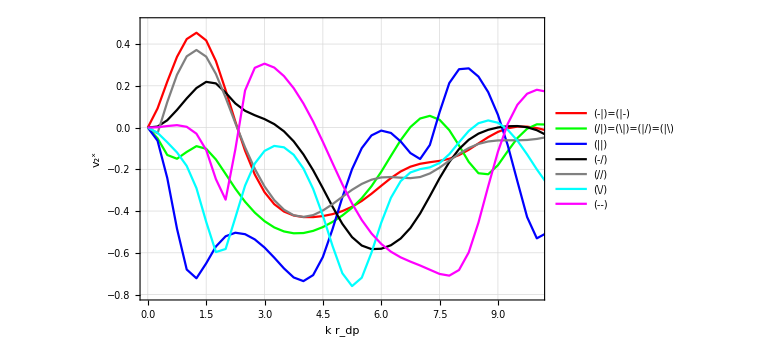

```mathematica
ListLinePlot[{Readv2x[phA0],Readv2x[phApio4],Readv2x[phApio2],Readv2x[phA0phBpio4],Readv2x[phApio4phBpio4],Readv2x[phA3pio4phBpio4],Readv2x[phA0phB0]},PlotRange->{{0,10},{-0.8,0.5}},GridLines->Automatic,PlotStyle->{{ -Graphics-},{ -Graphics-},{ -Graphics- },{ -Graphics-},{-Graphics-},{ -Graphics-},{ -Graphics-},{ -Graphics-},{-Graphics-},{-Graphics-}},PlotLegends->Placed[LineLegend[{"(-|)=(|-)","(/|)=(\|)=(|/)=(|\)","(||)","(-/)","(//)","(\/)","(--)"},LegendLayout->{"Column",3}],{0.42,0.85}],Joined->{True,True,True,True,True,True},ImageSize->Large,InterpolationOrder->1,Frame->True,FrameLabel->{"k r_dp","v_2^x"}]
```

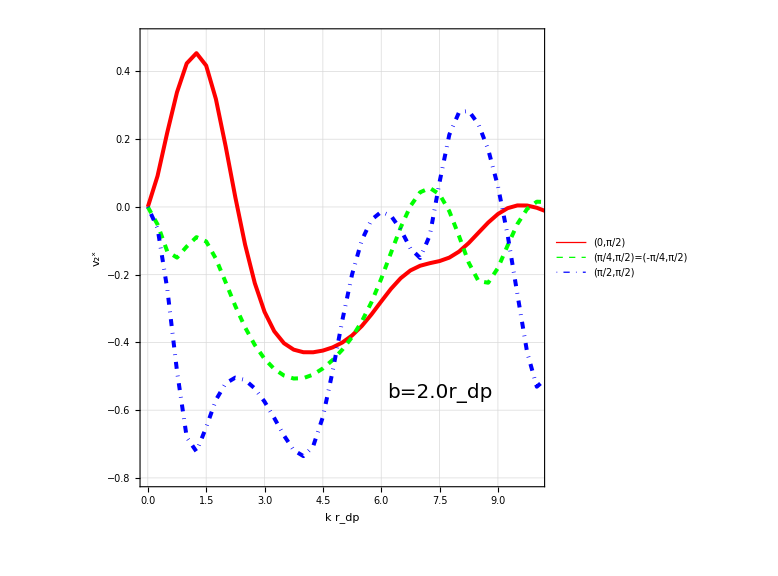

```mathematica
thick=0.005;
lp=ListLinePlot[{Readv2x[phA0],Readv2x[phApio4],Readv2x[phApio2]},PlotRange->{{0,10},{-0.8,0.5}},GridLines->Automatic,PlotStyle->{{ -Graphics-,Solid,Thickness[thick]},{ -Graphics-,Dashed,Thickness[thick]},{ -Graphics- ,DotDashed,Thickness[thick]},{ -Graphics-},{-Graphics-},{ -Graphics-},{ -Graphics-},{ -Graphics-},{-Graphics-},{-Graphics-}},PlotLegends->Placed[LineLegend[{Style["(0,π/2)",fsize],Style["(π/4,π/2)=(-π/4,π/2)",fsize],Style["(π/2,π/2)","(-/)",fsize]},LegendLayout->{"Column",1}],{0.5,0.89}],Joined->{True,True,True,True,True,True},ImageSize->Large,AspectRatio->1,InterpolationOrder->1,FrameLabel->{"k r_dp","v_2^x"},FrameStyle->Directive[FontSize->fsize],Frame->True];
text = Graphics[Text[Style["b=2.0r_dp",FontSize->fsize],{7.5,-0.55}]];
Show[{lp,text}]
```

## b = 0.5

#### r_dp and ϕ_i

```mathematica
phA0={{0.,{0.,0.}},{0.25,{0.022199610226677494,-3.233708957421098*^-16}},{0.5,{0.057020100648264696,2.4545802520967873*^-12}},{0.75,{0.09244554133270713,4.0054843471252503*^-13}},{1.,{0.1263693012014677,-6.2292293564778526*^-18}},{1.25,{0.15835852650914017,-8.205819464950639*^-17}},{1.5,{0.1882864094104682,-2.950080576406507*^-12}},{1.75,{0.21604093648018155,-5.843373470448591*^-10}},{2.,{0.24146612815931182,-4.179647114405998*^-12}},{2.25,{0.26434709304507953,-1.7677993548771128*^-14}},{2.5,{0.28441143051059403,-7.599369155670256*^-18}},{2.75,{0.30133044599258324,4.5441818907657596*^-12}},{3.,{0.3147243094328582,4.557108242627649*^-12}},{3.25,{0.32416878763138074,1.432566697736931*^-9}},{3.5,{0.3292097299210605,1.3020281005144584*^-17}},{3.75,{0.3293862949327113,6.397678628549379*^-9}},{4.,{0.32426868779519336,4.104137222172409*^-12}},{4.25,{0.3135145928400089,-6.185320700656885*^-17}},{4.5,{0.2969440427071676,-1.8298201593614884*^-9}},{4.75,{0.2746342467023483,1.2009764466574291*^-12}},{5.,{0.24702096203217158,3.5979744465027785*^-11}},{5.25,{0.2149867290058925,1.4250803676591577*^-9}},{5.5,{0.17990761755165782,2.8808831337374534*^-12}},{5.75,{0.14361928172150035,-1.6437752880314936*^-9}},{6.,{0.10828639384264392,2.0081346648901766*^-11}},{6.25,{0.0761717836894857,1.3666439071652599*^-8}},{6.5,{0.04935212875093234,-2.7787109733606735*^-10}},{6.75,{0.029446794200211825,5.092572506602096*^-11}},{7.,{0.01743495305725886,5.834004221749032*^-12}},{7.25,{0.013595072822594723,1.815318732978952*^-8}},{7.5,{0.017580492888943238,-4.214260709711403*^-8}},{7.75,{0.028572689316942405,5.2791111066478064*^-11}},{8.,{0.04547570678965424,2.8676058829004298*^-8}},{8.25,{0.06708835574556736,3.772564353619331*^-11}},{8.5,{0.09224145434519901,-1.2488209006914417*^-10}},{8.75,{0.11988167058937424,-1.0730981859917307*^-10}},{9.,{0.14911282753952865,2.1511553879634192*^-10}},{9.25,{0.17920622791681884,2.30835166134295*^-10}},{9.5,{0.20958878315938034,-2.1632853313380796*^-9}},{9.75,{0.23982207402570752,6.955105194640857*^-9}},{10.,{0.2695755990359157,2.4040120677721057*^-8}},{10.25,{0.29860068868834877,2.6779489376895326*^-10}},{10.5,{0.32670399213432394,2.2740789969074668*^-10}},{10.75,{0.35372685944089266,-1.1482722119426775*^-8}},{11.,{0.3795219141790549,-3.9381817237844456*^-11}},{11.25,{0.40393912716406816,-5.715627794165289*^-10}},{11.5,{0.4268097583541037,6.796027138824559*^-9}},{11.75,{0.4479415809751975,9.37176058531316*^-9}},{12.,{0.4671183647411953,-2.7039935272475596*^-10}},{12.25,{0.4841167889843586,1.846236117951979*^-9}},{12.5,{0.4987293398690844,6.413986587551963*^-11}},{12.75,{0.5107969258671928,-2.6307044732328535*^-10}},{13.,{0.5202300909977985,1.941686866148576*^-10}},{13.25,{0.527012120098051,2.4896745881355735*^-9}},{13.5,{0.5311662153627403,-6.55033039209892*^-10}},{13.75,{0.532707698718055,7.709740293127159*^-8}},{14.,{0.5315826932165859,7.16467500444179*^-10}},{14.25,{0.5276323763008932,4.1658235243538185*^-8}},{14.5,{0.5205749240864513,4.841728242272841*^-10}},{14.75,{0.5100191062111326,6.18242222882949*^-8}},{15.,{0.4954952289054072,-2.554342592899317*^-10}},{15.25,{0.47649789834698325,1.2206056302336295*^-9}},{15.5,{0.45254444920372555,-4.447310435913265*^-10}},{15.75,{0.42323854897097596,7.10370286328924*^-10}},{16.,{0.38835012187758106,3.070225377210291*^-7}},{16.25,{0.3478909190412796,6.190112537168756*^-10}},{16.5,{0.30219722755128803,7.105148534869831*^-9}},{16.75,{0.2519878853288751,1.2048179317471696*^-8}},{17.,{0.1983885767218807,-9.820064882035985*^-10}},{17.25,{0.14290005940383158,-2.892986308133414*^-9}},{17.5,{0.08730905331517917,-8.328987655554015*^-10}},{17.75,{0.03352230971781106,-8.566285129306036*^-10}},{18.,{-0.01659470783844711,4.040486379861708*^-8}},{18.25,{-0.061415144858937704,3.8014244506710975*^-8}},{18.5,{-0.09969679216959103,-1.960617409555274*^-9}},{18.75,{-0.13064173821265992,-2.085085253694762*^-9}},{19.,{-0.15397780910247275,5.298263237805645*^-10}},{19.25,{-0.1697789245969233,-3.044236910851411*^-9}},{19.5,{-0.17847824881494687,5.330904271186362*^-10}},{19.75,{-0.18072965134357877,-3.828753205370342*^-8}},{20.,{-0.17730299740748653,-1.8299369896747634*^-9}},{20.25,{-0.1690136606252958,-4.734310937458002*^-9}},{20.5,{-0.15664353431976907,-8.319179235596244*^-9}},{20.75,{-0.1409320535072345,-6.51648721696346*^-9}},{21.,{-0.12252490209019701,-1.970731271906051*^-9}},{21.25,{-0.10200198733496846,-5.8727872096069326*^-9}},{21.5,{-0.07985397717850207,2.1590493548829147*^-9}},{21.75,{-0.05651258520390734,-2.7443044276187826*^-9}},{22.,{-0.03234914248684555,-1.2892177755225047*^-8}},{22.25,{-0.007699364168515819,1.0207179911922385*^-8}},{22.5,{0.01713399397063298,-8.947039113079027*^-9}},{22.75,{0.04186444534207364,-1.1951455250353467*^-8}},{23.,{0.0662378780130944,-3.6711249864972083*^-9}},{23.25,{0.0899928492480079,1.824622534306414*^-8}},{23.5,{0.11290524615241479,-5.283965666147993*^-9}},{23.75,{0.1347812557521044,-2.3865608893983965*^-8}},{24.,{0.15546528637278154,-8.151373269828486*^-9}},{24.25,{0.17485683632199786,3.499731503433054*^-8}},{24.5,{0.1929071050077821,-1.428644003472946*^-8}},{24.75,{0.20962926327387363,-9.983987113872535*^-9}},{25.,{0.225061493204569,-4.4720926751389104*^-10}},{25.25,{0.23926807324466187,-7.57694519430747*^-10}},{25.5,{0.2522888600654309,-2.0050949432638445*^-8}},{25.75,{0.26412060064671716,-1.768001037332893*^-8}},{26.,{0.27467963910799453,-2.09888229326627*^-8}},{26.25,{0.2837766212722862,-1.2714377942246642*^-8}},{26.5,{0.2911143475633295,-6.640791653444014*^-9}},{26.75,{0.2962921158805989,-1.302313591576596*^-8}},{27.,{0.2988205576059515,1.8128262167541036*^-7}},{27.25,{0.2981703031466765,-4.554119402471526*^-9}},{27.5,{0.2938188644754394,-1.1328638703142311*^-8}},{27.75,{0.2853297448766344,-6.315553682894834*^-8}},{28.,{0.2723776038861305,-1.8380678096516887*^-8}},{28.25,{0.25488721820966076,1.3839086713840356*^-8}},{28.5,{0.23293909385088107,-2.530628240699977*^-8}},{28.75,{0.20692303997382072,-2.1284576025215667*^-8}},{29.,{0.17741466207916531,-2.3381934175973887*^-8}},{29.25,{0.14515443896255487,-6.322640410202894*^-8}},{29.5,{0.1109995202257693,-3.9775625245640615*^-8}},{29.75,{0.07583148989020967,-8.033876116617157*^-8}},{30.,{0.040540868035599885,-9.465017585408205*^-8}}};
phApio4={{0.,{0.,0.}},{0.25,{-0.003093061372563969,0.0007509538362622593}},{0.5,{-0.0119144561610959,0.0032308192980803362}},{0.75,{-0.025150295053533,0.007786327246516058}},{1.,{-0.04079586534095944,0.014603656485239064}},{1.25,{-0.05648376283152627,0.02362469316037341}},{1.5,{-0.06989355442822608,0.03456141433130068}},{1.75,{-0.07910223574048664,0.04697076309432284}},{2.,{-0.08278276620637898,0.06034666905165019}},{2.25,{-0.08024428009270014,0.07419434663142321}},{2.5,{-0.0713665979551536,0.08806964136724309}},{2.75,{-0.05649575493853101,0.10158340987392002}},{3.,{-0.036352530218432266,0.11438191957552031}},{3.25,{-0.011973691497340863,0.12611209387367817}},{3.5,{0.015309928954082215,0.13638286098885657}},{3.75,{0.043876659811600376,0.14472986110848127}},{4.,{0.0718237488161075,0.15059077071156465}},{4.25,{0.09701511495691943,0.15330190329756896}},{4.5,{0.11720215269869841,0.15212262264645948}},{4.75,{0.13023743292552575,0.1462998333241364}},{5.,{0.1343818590938626,0.13516878213858388}},{5.25,{0.12865252447981268,0.11827784064992725}},{5.5,{0.11312776429323027,0.09550989239832565}},{5.75,{0.08909523147049926,0.06716411295777064}},{6.,{0.058967522145176345,0.03395983028225719}},{6.25,{0.025963728694016235,-0.0030308206254508153}},{6.5,{-0.00636036871810935,-0.0425091133900384}},{6.75,{-0.03460508068122762,-0.08308857733656969}},{7.,{-0.05592934358201362,-0.12340785595889406}},{7.25,{-0.06830776091721849,-0.1621996345666178}},{7.5,{-0.07064681559295277,-0.19831594758990445}},{7.75,{-0.0627976449471277,-0.23072633290355077}},{8.,{-0.045508666004185246,-0.25852009419731303}},{8.25,{-0.0203368517353224,-0.2809100058187721}},{8.5,{0.010476854704707097,-0.2972811052458509}},{8.75,{0.04418656159908712,-0.3072502180919101}},{9.,{0.0777857414639741,-0.31073997070819415}},{9.25,{0.10831038250425874,-0.3080324064458574}},{9.5,{0.13316522201080555,-0.299786402381154}},{9.75,{0.15041548128070864,-0.2869938628437492}},{10.,{0.1589789479373257,-0.27087751977094665}},{10.25,{0.15867735133379082,-0.252744166268821}},{10.5,{0.1501482554201939,-0.2338925017061865}},{10.75,{0.1346496621296208,-0.21538765414822794}},{11.,{0.11381766876729851,-0.19809442888138726}},{11.25,{0.08943239247883827,-0.18259445642269445}},{11.5,{0.06323093283615928,-0.16920994782069007}},{11.75,{0.03677711703954671,-0.1580402418520763}},{12.,{0.011394412199744392,-0.14901432809021856}},{12.25,{-0.011861321768847247,-0.14193655848475203}},{12.5,{-0.032195734278959776,-0.13653434779146864}},{12.75,{-0.04905394168537024,-0.13249466175007063}},{13.,{-0.062096558324804395,-0.129492087762667}},{13.25,{-0.07117086862776228,-0.1272115403346915}},{13.5,{-0.07628949648477656,-0.12536428171748115}},{13.75,{-0.07761242842325236,-0.12369870762795245}},{14.,{-0.07543198835792535,-0.12201074213430295}},{14.25,{-0.0701604065806974,-0.12015061244140578}},{14.5,{-0.06231663815322206,-0.11802429867017872}},{14.75,{-0.052510079462690186,-0.11559872086528773}},{15.,{-0.04141848317562637,-0.11289638176723234}},{15.25,{-0.029761807672447783,-0.10999073741384924}},{15.5,{-0.01826758541576333,-0.10699846560028652}},{15.75,{-0.0076323316863965065,-0.10406430590162728}},{16.,{0.001519653325849282,-0.10134513423460939}},{16.25,{0.00867459777449235,-0.09899405637790688}},{16.5,{0.0134627498054457,-0.09714309766072644}},{16.75,{0.015678148407328084,-0.09588750744667998}},{17.,{0.015288438993058368,-0.0952776133385938}},{17.25,{0.01242600342961524,-0.09531310082509106}},{17.5,{0.007368778718192585,-0.09594730574094759}},{17.75,{0.0005092027832118072,-0.09709090252094006}},{18.,{-0.0076832038811795594,-0.09862701991049881}},{18.25,{-0.016699528430075467,-0.10042057025869754}},{18.5,{-0.026028137424979954,-0.10233692180717596}},{18.75,{-0.03518419445421109,-0.10424855687980362}},{19.,{-0.04373385265957032,-0.10605815272267313}},{19.25,{-0.051310600635047714,-0.10769271753905638}},{19.5,{-0.05762512782588711,-0.10910596638344579}},{19.75,{-0.06246777673745753,-0.11031109103599192}},{20.,{-0.0657108462485215,-0.11134433628429409}},{20.25,{-0.06730405234237555,-0.11227674295431957}},{20.5,{-0.06727046104143178,-0.11321479262848962}},{20.75,{-0.0657009408227465,-0.11428741050962075}},{21.,{-0.06274807089359859,-0.11564093717488419}},{21.25,{-0.058619987144754575,-0.11742985090880671}},{21.5,{-0.05357271622939861,-0.11980741816464203}},{21.75,{-0.04790102551981693,-0.12291406853594966}},{22.,{-0.04192979722904807,-0.12686631656836012}},{22.25,{-0.035999126010017375,-0.13174714765929402}},{22.5,{-0.030449437975121646,-0.13759491320796866}},{22.75,{-0.025603143544441834,-0.1443989603371122}},{23.,{-0.02174463254966374,-0.15209089143240198}},{23.25,{-0.019101379708546404,-0.16055456404326887}},{23.5,{-0.01782553236286143,-0.16962371680960373}},{23.75,{-0.017980838332224355,-0.17910307547180587}},{24.,{-0.019537056016925514,-0.18877663735185418}},{24.25,{-0.022372766509204205,-0.19843476927980966}},{24.5,{-0.026282918966651542,-0.2078873473048152}},{24.75,{-0.030999800452730496,-0.21698551951556028}},{25.,{-0.03621063206957967,-0.22562629485943783}},{25.25,{-0.041583132509972726,-0.23376909665347595}},{25.5,{-0.046788775928943094,-0.24142820626175965}},{25.75,{-0.05152121267678501,-0.24867329805703162}},{26.,{-0.05551326483307927,-0.25562154354143934}},{26.25,{-0.05854549295205339,-0.26242308736875425}},{26.5,{-0.060458500188615684,-0.26925180508233215}},{26.75,{-0.06115166860773026,-0.27629537949942695}},{27.,{-0.06058934321921671,-0.2837411048001687}},{27.25,{-0.0587953485959065,-0.29175605766162005}},{27.5,{-0.055861211513715515,-0.3004894063686929}},{27.75,{-0.05193517171014329,-0.31005236739735736}},{28.,{-0.04722210374669174,-0.3205158270672678}},{28.25,{-0.041979484221190876,-0.33188239511693063}},{28.5,{-0.03650288136849152,-0.3441045301675682}},{28.75,{-0.031115098541575237,-0.3570681072405184}},{29.,{-0.026144350751422615,-0.3705968020276974}},{29.25,{-0.02190129656933798,-0.3844546235682197}},{29.5,{-0.018653703362092686,-0.39836679583354456}},{29.75,{-0.016596317621825497,-0.41203502665699804}},{30.,{-0.01583388160104821,-0.42516275894837574}}};
phApio2={{0.,{0.,0.}},{0.25,{-0.0029384569516181795,-3.2226551041161135*^-14}},{0.5,{-0.011987824066760059,4.017973990101121*^-15}},{0.75,{-0.027489582231725564,8.055719724382482*^-15}},{1.,{-0.04967320724181299,3.743593394425996*^-14}},{1.25,{-0.07869625093774191,4.287928842533006*^-14}},{1.5,{-0.11478904521078694,-6.036240530205267*^-13}},{1.75,{-0.15842934307912618,-3.551285877575524*^-17}},{2.,{-0.21043098350362172,2.6165299729990428*^-12}},{2.25,{-0.27171803190915444,-1.0639758629050718*^-12}},{2.5,{-0.34242139246360714,-5.932361609380844*^-11}},{2.75,{-0.42002087871594695,3.5364038565674925*^-11}},{3.,{-0.4972644173674113,7.235608432264125*^-12}},{3.25,{-0.562565995451862,-7.13038658621127*^-9}},{3.5,{-0.6052915303581591,1.4290752645761118*^-9}},{3.75,{-0.622229811038092,-4.080250728736563*^-9}},{4.,{-0.6182392496499612,-5.810032065509867*^-10}},{4.25,{-0.6013312155951804,1.2410913977594729*^-9}},{4.5,{-0.5781947006714057,4.044566703679034*^-9}},{4.75,{-0.5528167865667997,-3.572472087703265*^-11}},{5.,{-0.5269875405595194,1.4711164597427916*^-9}},{5.25,{-0.5011729300700418,3.044817383348484*^-9}},{5.5,{-0.47516016706781833,1.0229195515237303*^-10}},{5.75,{-0.44841827713628507,-7.077050624463947*^-11}},{6.,{-0.4202732582450019,1.0341700775340025*^-8}},{6.25,{-0.3899760097708357,1.7961476981085666*^-8}},{6.5,{-0.35672432298758233,-3.0597698636101196*^-9}},{6.75,{-0.3196632540376562,-4.442713618603858*^-11}},{7.,{-0.27789411324632035,-2.4725137396080575*^-11}},{7.25,{-0.23050225331506813,2.166948597701972*^-10}},{7.5,{-0.17664645052466302,-2.8571844345804556*^-10}},{7.75,{-0.1157460537878227,2.749800238019795*^-12}},{8.,{-0.04784975487476223,-1.5138503664647824*^-10}},{8.25,{0.025736206813392108,5.98577407699245*^-10}},{8.5,{0.10150396010825827,-3.034526843960164*^-10}},{8.75,{0.17266377415292417,1.7100062520410394*^-10}},{9.,{0.22858370821263102,-4.394776672883426*^-8}},{9.25,{0.2560925801111403,-1.3577941335610532*^-10}},{9.5,{0.24376813124225755,1.8011665185413034*^-10}},{9.75,{0.18796068049512732,2.4438194130503804*^-10}},{10.,{0.09611550465909753,-3.3259204583403514*^-9}},{10.25,{-0.01619863611568729,9.399264191380824*^-10}},{10.5,{-0.13231637865053547,-8.890643393387889*^-10}},{10.75,{-0.2400286916007725,1.5305942600634823*^-9}},{11.,{-0.33307702034323683,-8.738490463152343*^-11}},{11.25,{-0.40981819829313193,2.594129065566776*^-8}},{11.5,{-0.47121828182715025,-5.937289436146524*^-11}},{11.75,{-0.5192966506380639,-1.6597701501497007*^-7}},{12.,{-0.5562297130208246,3.201141337391603*^-14}},{12.25,{-0.5839197756374606,-9.157520232586777*^-10}},{12.5,{-0.6038322299731612,-1.3433166574579774*^-10}},{12.75,{-0.6169387399452809,-5.778974423634576*^-9}},{13.,{-0.6236907488011719,8.207461165861919*^-9}},{13.25,{-0.6239606876578837,-9.897422872280066*^-9}},{13.5,{-0.6169306558236884,-9.211967454182378*^-9}},{13.75,{-0.600898490706012,-5.279471111272664*^-10}},{14.,{-0.5730402045432234,-8.644016823942533*^-9}},{14.25,{-0.5292864072794194,-1.754171990679515*^-9}},{14.5,{-0.46489414819364877,1.099756278140487*^-9}},{14.75,{-0.37699823993988574,-3.816230768572758*^-9}},{15.,{-0.2705239563846323,5.503309804476*^-9}},{15.25,{-0.164605280202064,-3.38063934490749*^-9}},{15.5,{-0.0878890470878632,-3.762312366349213*^-9}},{15.75,{-0.058007041640810976,-3.5569358379418617*^-9}},{16.,{-0.0687849987623797,2.0629341177616333*^-9}},{16.25,{-0.1011568529807157,-1.3120925520563492*^-9}},{16.5,{-0.13855980875570825,2.4672428813657955*^-8}},{16.75,{-0.171808541885172,-1.5562444475438931*^-7}},{17.,{-0.19722333427290992,1.8411741718482985*^-8}},{17.25,{-0.21392374416189,-1.3223419548221664*^-8}},{17.5,{-0.22212255068948256,-6.697927040887866*^-9}},{17.75,{-0.22229996801699792,9.57063161159883*^-9}},{18.,{-0.21488978872445244,-6.141738381454145*^-8}},{18.25,{-0.20016656500021873,7.3993359193801835*^-9}},{18.5,{-0.1782626652409688,-2.051531361806665*^-9}},{18.75,{-0.14923729768525473,4.9508993843707815*^-9}},{19.,{-0.11309202110082749,-1.1638647590194544*^-8}},{19.25,{-0.07011799577754328,-3.761351773468653*^-9}},{19.5,{-0.02089258776283046,-9.865868932722835*^-9}},{19.75,{0.03336541358475436,-2.040691883075188*^-9}},{20.,{0.09054919508087308,-4.211109095706056*^-9}},{20.25,{0.14749073768618506,-1.2849954168039903*^-8}},{20.5,{0.19998117139037974,-2.5640980931705442*^-8}},{20.75,{0.24320861329078253,-8.280523321321073*^-9}},{21.,{0.27255893481872157,-2.5226475461771145*^-8}},{21.25,{0.2846943602998791,-2.427283908759082*^-8}},{21.5,{0.2784054912830645,1.945787001117301*^-8}},{21.75,{0.2549077546104089,-4.1601052450150425*^-8}},{22.,{0.21736551866818693,-1.3881977526506388*^-8}},{22.25,{0.16997396122549033,-9.598707451870646*^-9}},{22.5,{0.11699320833341048,-3.6693742579688936*^-8}},{22.75,{0.06207602029332116,2.7500516251999697*^-8}},{23.,{0.007946491096557602,-3.0161545912495524*^-8}},{23.25,{-0.04355143004388203,1.2544909760159035*^-8}},{23.5,{-0.09135122158518409,-1.5965272674416005*^-8}},{23.75,{-0.13491853399762402,4.4787392848879234*^-9}},{24.,{-0.17407471055008647,-2.1685916462796676*^-8}},{24.25,{-0.2088164716941053,5.945354447151854*^-8}},{24.5,{-0.23921346247044004,-8.451316744682769*^-8}},{24.75,{-0.2653101350803379,3.6964427678861074*^-8}},{25.,{-0.2870718920558611,-1.9829377684529027*^-8}},{25.25,{-0.30435399986080647,-8.214450834473106*^-7}},{25.5,{-0.3169030155488349,3.5490647576583835*^-9}},{25.75,{-0.3244065981446116,-4.231005973981436*^-9}},{26.,{-0.32660082331163043,-2.851559636668207*^-8}},{26.25,{-0.32340471380143165,6.474788896134409*^-9}},{26.5,{-0.31508267701635967,-3.3113331073768096*^-7}},{26.75,{-0.3023062513223773,-1.4864711566633473*^-8}},{27.,{-0.28612698446746715,-1.1795391841042435*^-8}},{27.25,{-0.267734811443176,3.2822803233213226*^-8}},{27.5,{-0.2482342241254729,2.319829906956299*^-8}},{27.75,{-0.22843160822556383,-6.876367481894245*^-7}},{28.,{-0.20873437925488783,-4.3891041184715276*^-8}},{28.25,{-0.18926088681205114,-4.575455096160719*^-8}},{28.5,{-0.16984608245571087,-4.898795006320929*^-7}},{28.75,{-0.1502431720686245,1.16069709013022*^-7}},{29.,{-0.13017560847174348,6.184682742119325*^-8}},{29.25,{-0.1094092617836429,-1.7099873183635688*^-8}},{29.5,{-0.08784106737906043,1.6594349803987257*^-8}},{29.75,{-0.06547879208912816,-2.893599127081024*^-7}},{30.,{-0.0425499595635865,3.9935202689336*^-8}}};
phA0phBpio4={{0.,{0.,0.}},{0.25,{-0.011213911912050858,-0.005842683874067}},{0.5,{-0.04070559737328949,-0.02452408406775642}},{0.75,{-0.07421133031260645,-0.054260794476999996}},{1.,{-0.0957599882323035,-0.08825166285911971}},{1.25,{-0.10000046766930648,-0.12005612263947572}},{1.5,{-0.0912173296457293,-0.14725438181924086}},{1.75,{-0.07579541037249823,-0.17021969978342974}},{2.,{-0.05836240375056968,-0.1900193005194686}},{2.25,{-0.041495277445785274,-0.20743898927206628}},{2.5,{-0.026415727956796604,-0.22279148666000118}},{2.75,{-0.013593274238978482,-0.23598529528579001}},{3.,{-0.003098612662217715,-0.24663666396852377}},{3.25,{0.0052132705929912385,-0.2541758499993773}},{3.5,{0.011612644158812954,-0.25794878226715945}},{3.75,{0.016446023022082232,-0.2573237514690558}},{4.,{0.020102111093294833,-0.2518030815508355}},{4.25,{0.02297854245627976,-0.2411329785903828}},{4.5,{0.025445843935395215,-0.22539100313622137}},{4.75,{0.027810903902175818,-0.20503217223923573}},{5.,{0.030285537767318335,-0.1808776243644108}},{5.25,{0.03296804515881137,-0.15404215583612674}},{5.5,{0.035841299277307496,-0.12581973709159988}},{5.75,{0.03878784612175759,-0.0975503115546302}},{6.,{0.041617258612625954,-0.07049617800793362}},{6.25,{0.0440996237357186,-0.04575607338995614}},{6.5,{0.04599799017025788,-0.024219624405665982}},{6.75,{0.047097092715415706,-0.006557403167418255}},{7.,{0.04721893620097227,0.0067518156695910445}},{7.25,{0.046247081331779655,0.015393405942545402}},{7.5,{0.044127847261481376,0.019169449162171216}},{7.75,{0.040880968928987724,0.017968494110636578}},{8.,{0.03660467989459879,0.011739452517031698}},{8.25,{0.03148027404772205,0.000483823082815365}},{8.5,{0.025773676005751346,-0.015743050224058534}},{8.75,{0.019833446910164112,-0.03681156144609722}},{9.,{0.014079829066136616,-0.06249190845401018}},{9.25,{0.00898107604224219,-0.09241611656206145}},{9.5,{0.005015365995029918,-0.12605054875161992}},{9.75,{0.002614888642961751,-0.16267354965363096}},{10.,{0.0020982343465088403,-0.20138709751747041}},{10.25,{0.0036023905840392853,-0.24115787030161812}},{10.5,{0.007029939829832744,-0.28089797029165847}},{10.75,{0.012028293376970575,-0.31956749730745637}},{11.,{0.01801476729412897,-0.356279036841941}},{11.25,{0.024244330326541576,-0.3903766561230165}},{11.5,{0.02990786448258749,-0.4214668934224791}},{11.75,{0.034242300731385705,-0.44939598458951974}},{12.,{0.03662766989446997,-0.474178648470973}},{12.25,{0.03665904161008362,-0.49590270354787697}},{12.5,{0.03418780432759728,-0.5146273007994215}},{12.75,{0.029332077487428478,-0.5302957512821996}},{13.,{0.02246878812517203,-0.5426855821368595}},{13.25,{0.014181105599497154,-0.5513843562231814}},{13.5,{0.005209759444281266,-0.5558214604384182}},{13.75,{-0.0036346859735018233,-0.555336715416592}},{14.,{-0.011572698225258147,-0.5492787372322604}},{14.25,{-0.017962399103178723,-0.5371282498359268}},{14.5,{-0.02239221778870198,-0.518602471928163}},{14.75,{-0.02474743118807887,-0.4937364052786587}},{15.,{-0.02521930691269253,-0.4629015021428958}},{15.25,{-0.02426321410458094,-0.42677166092766855}},{15.5,{-0.022508136586728174,-0.38623999983267976}},{15.75,{-0.0206388267267868,-0.34231828648620793}},{16.,{-0.019279226877212723,-0.2960373878893079}},{16.25,{-0.018897895425056044,-0.24838118980297663}},{16.5,{-0.019733742691384438,-0.2002461771672908}},{16.75,{-0.02178203591532366,-0.15244446290968713}},{17.,{-0.024807946740523522,-0.1057103015453966}},{17.25,{-0.028385594730902595,-0.060726512965476764}},{17.5,{-0.03197544064764539,-0.018144777805377942}},{17.75,{-0.03500034613828887,0.021429458894435236}},{18.,{-0.03692901768975841,0.05742651077031257}},{18.25,{-0.037346860184298496,0.08935036265099591}},{18.5,{-0.03600865135044999,0.11679969588923168}},{18.75,{-0.03285122380531,0.1394751338519989}},{19.,{-0.02798907501156258,0.157256667204148}},{19.25,{-0.021681339643165074,0.1700734289602614}},{19.5,{-0.014289509319995005,0.177995948339073}},{19.75,{-0.006228468776989576,0.18117810631109582}},{20.,{0.002075653702248902,0.17982603907319844}},{20.25,{0.01022155360398833,0.174190525205572}},{20.5,{0.017856064815584258,0.1645341730481178}},{20.75,{0.024693967148486304,0.15114364867478572}},{21.,{0.030521407568931586,0.1343102802604872}},{21.25,{0.03520309260914457,0.11435220918082391}},{21.5,{0.03867851286044611,0.09161787205082973}},{21.75,{0.040960965912980964,0.06651187154198814}},{22.,{0.04212373493614269,0.03949719088175662}},{22.25,{0.04230134500369646,0.011120576860812354}},{22.5,{0.04165898267780167,-0.017998753809744923}},{22.75,{0.040384686282520586,-0.0471733103938875}},{23.,{0.03865302629809848,-0.07570804655481075}},{23.25,{0.036611189764351446,-0.10290082813416461}},{23.5,{0.03433964883817308,-0.12815620767572486}},{23.75,{0.03184773175404372,-0.1510315800055509}},{24.,{0.029054682056504428,-0.1712805450459169}},{24.25,{0.025799703251185246,-0.18889276626044338}},{24.5,{0.021888390483463478,-0.20407445418931458}},{24.75,{0.017112755913693035,-0.21721109642666897}},{25.,{0.011301343308436414,-0.2287855439114118}},{25.25,{0.004369951705677847,-0.23929747172670146}},{25.5,{-0.003621431346933134,-0.24915344057186872}},{25.75,{-0.012466279477962838,-0.25860005256744273}},{26.,{-0.02175604729619833,-0.2676393696454342}},{26.25,{-0.030926283586409916,-0.27599984600925453}},{26.5,{-0.03926219675491241,-0.2831262761081366}},{26.75,{-0.04599226067252802,-0.28823428665849893}},{27.,{-0.05040961626088303,-0.29041330334778603}},{27.25,{-0.05195924775810526,-0.2887624739082132}},{27.5,{-0.050383507195010904,-0.28255519999809675}},{27.75,{-0.04578382385907016,-0.27138853827351556}},{28.,{-0.038620628689653526,-0.2552539452639651}},{28.25,{-0.029643111232029517,-0.23455442301461216}},{28.5,{-0.019754583679289527,-0.209967704682267}},{28.75,{-0.009881708698714919,-0.18242814464882995}},{29.,{-0.0008472686372413432,-0.1528889658390937}},{29.25,{0.006720392365165678,-0.12226444161970454}},{29.5,{0.012407841320653807,-0.09134628904852692}},{29.75,{0.016039952133059233,-0.0607772766146025}},{30.,{0.017645644980855715,-0.031057333457377382}}};
phApio4phBpio4={{0.,{0.,0.}},{0.25,{-0.004478844003344312,-0.001719489057138558}},{0.5,{-0.01791974196461528,-0.007085547643933221}},{0.75,{-0.03972114529606895,-0.016485598269596013}},{1.,{-0.0680912773523376,-0.030231455999695935}},{1.25,{-0.09989499612177087,-0.04831591535250244}},{1.5,{-0.13091779514180138,-0.07013608817681928}},{1.75,{-0.15654249520130745,-0.09425160275145586}},{2.,{-0.17267571321115407,-0.11828008079898332}},{2.25,{-0.17663918922138402,-0.13902341526734827}},{2.5,{-0.16775365482888152,-0.1528716904501385}},{2.75,{-0.1474525903797542,-0.1564530871275919}},{3.,{-0.11890515818565757,-0.1473934434766045}},{3.25,{-0.08625286848620231,-0.12495070353780133}},{3.5,{-0.053678709070932494,-0.09027177225515874}},{3.75,{-0.0245865486765059,-0.04614420112942278}},{4.,{-0.0011198574204871747,0.0036608915374594046}},{4.25,{0.015899083947940366,0.0551890320473368}},{4.5,{0.02671184888386904,0.10495502641945563}},{4.75,{0.032222101576018035,0.1503064324066059}},{5.,{0.03361275323380653,0.18949471384598687}},{5.25,{0.03207033320553323,0.22155534886284903}},{5.5,{0.028626906248511278,0.24610559246360839}},{5.75,{0.024097449263419356,0.26314250476046935}},{6.,{0.019075149018139385,0.2728666284286636}},{6.25,{0.013956988464836393,0.2755689949302626}},{6.5,{0.00897689310633815,0.2715495758481979}},{6.75,{0.004240376328472719,0.2610791134746712}},{7.,{-0.0002536107174409492,0.24438285786979877}},{7.25,{-0.004585543325511634,0.2216544818933173}},{7.5,{-0.008911456120969746,0.19308074688661922}},{7.75,{-0.013451599298107752,0.15889588676354327}},{8.,{-0.01849072737389596,0.11945183362773033}},{8.25,{-0.024372180519071734,0.07531873948942931}},{8.5,{-0.03149340657189894,0.02740368992683573}},{8.75,{-0.04028609859766998,-0.02291487434820942}},{9.,{-0.05118581285764722,-0.07367149511807759}},{9.25,{-0.06457340603417373,-0.12226330627779936}},{9.5,{-0.0807002630933697,-0.16553282965026525}},{9.75,{-0.09960018826069804,-0.20005192526658808}},{10.,{-0.12102188904274548,-0.2226216589392906}},{10.25,{-0.1444066592618846,-0.23090489872003095}},{10.5,{-0.16894977617473875,-0.2240001110931252}},{10.75,{-0.19373040266290695,-0.20272625208410788}},{11.,{-0.21787954192439252,-0.1694782777085942}},{11.25,{-0.24072139918998564,-0.12771038094748904}},{11.5,{-0.26184774376218245,-0.0812494453874427}},{11.75,{-0.28111220679824866,-0.033683785893723166}},{12.,{-0.29857138379024656,0.012024167789068774}},{12.25,{-0.31439880152895844,0.053681748008874076}},{12.5,{-0.3288048929688992,0.08982425519060162}},{12.75,{-0.3419674768239274,0.11957550752878489}},{13.,{-0.3540013313019441,0.14249654984197832}},{13.25,{-0.3648987371042387,0.1584173243457696}},{13.5,{-0.37453608173335207,0.16735177232077397}},{13.75,{-0.38264901570011206,0.16942203008411102}},{14.,{-0.38882268718505353,0.16483636631792695}},{14.25,{-0.39249488899069923,0.15390629097188258}},{14.5,{-0.39296502944009204,0.13709042917061068}},{14.75,{-0.3894275793027552,0.11506847690447054}},{15.,{-0.38103676720705437,0.0888208167947862}},{15.25,{-0.3670116745859644,0.059700942836856945}},{15.5,{-0.34678262027279955,0.02945210528524277}},{15.75,{-0.32016157183845423,0.00014471316305937292}},{16.,{-0.2874929926199014,-0.026009656401000118}},{16.25,{-0.24973511974975546,-0.046950866120737504}},{16.5,{-0.208407407979065,-0.061096690687802206}},{16.75,{-0.1654029722377384,-0.06762956565223818}},{17.,{-0.1227074184536582,-0.06664875058414561}},{17.25,{-0.08209622442143963,-0.059080786429084285}},{17.5,{-0.044925969201249576,-0.046457721453153855}},{17.75,{-0.012017753223149692,-0.03060524890248129}},{18.,{0.01628901970332141,-0.013362725276601725}},{18.25,{0.04005288515239532,0.003617913094369697}},{18.5,{0.059593270820438686,0.0189896149165235}},{18.75,{0.07534842088235999,0.031740841798089954}},{19.,{0.08785901459984802,0.04116637072390613}},{19.25,{0.09754006323497753,0.046841968274470555}},{19.5,{0.10478806563683916,0.04857878118483129}},{19.75,{0.10990445214155481,0.04638358169860869}},{20.,{0.11308144786067484,0.0404470519755695}},{20.25,{0.11441633606292764,0.0311370678779464}},{20.5,{0.11390684205203686,0.019003495081253905}},{20.75,{0.11148261639689558,0.004796114335940374}},{21.,{0.10700722974672294,-0.01053472829289655}},{21.25,{0.10032305509348474,-0.025842017332273086}},{21.5,{0.09127742441038927,-0.03982222163823627}},{21.75,{0.07978139695247487,-0.051097071305340684}},{22.,{0.06583868911595099,-0.05833954572169718}},{22.25,{0.04959938075500391,-0.06044108522338247}},{22.5,{0.03136897071421122,-0.056675539469381524}},{22.75,{0.011605476294423099,-0.04684875764043744}},{23.,{-0.009142030148728261,-0.03135495200412809}},{23.25,{-0.03025478053309163,-0.011149812500036192}},{23.5,{-0.051153819937972286,0.01237805603696313}},{23.75,{-0.07135469657699701,0.03760144288498301}},{24.,{-0.09049308368877189,0.06282420719264317}},{24.25,{-0.10835209118972586,0.08645541774419678}},{24.5,{-0.12482548393536368,0.10712166466822981}},{24.75,{-0.1399095773139763,0.12369757331480286}},{25.,{-0.1536599240720453,0.13531246659521529}},{25.25,{-0.16615448412239736,0.14132884913582125}},{25.5,{-0.17745648553904314,0.14132101681325868}},{25.75,{-0.18759042171841125,0.1350276785805144}},{26.,{-0.1965111582390225,0.12236777124697566}},{26.25,{-0.20408437613131125,0.10344378347563961}},{26.5,{-0.2100663134705187,0.07860765690629261}},{26.75,{-0.2141042671219257,0.04851069769024316}},{27.,{-0.21574763647234718,0.014199003906583987}},{27.25,{-0.21446407972960652,-0.02278641094502713}},{27.5,{-0.20973017984621756,-0.060411313359632346}},{27.75,{-0.2011110799653265,-0.09619821100575512}},{28.,{-0.18838781654012876,-0.1274290553077182}},{28.25,{-0.171668429526873,-0.15150057128496544}},{28.5,{-0.15142034498557302,-0.16633162139447671}},{28.75,{-0.1285063679445216,-0.17077892413718448}},{29.,{-0.10401697212468114,-0.1648216908077299}},{29.25,{-0.0791117622172213,-0.1495406940362319}},{29.5,{-0.0548606413776587,-0.12683805019584993}},{29.75,{-0.0320920496321402,-0.09904662180827321}},{30.,{-0.01135601717419268,-0.06854152887790073}}};
phA3pio4phBpio4={{0.,{0.,0.}},{0.25,{-0.009896727642826007,5.350923272424131*^-8}},{0.5,{-0.036288752744939666,4.27214384115397*^-8}},{0.75,{-0.07202353256400419,2.7458997296881137*^-9}},{1.,{-0.10995813462385196,6.74367355731095*^-8}},{1.25,{-0.14526836032098198,7.024183087333231*^-8}},{1.5,{-0.17578564114581616,-1.372168665476364*^-8}},{1.75,{-0.20121452300164253,4.154632619614095*^-8}},{2.,{-0.2222170628682311,5.359477384491958*^-8}},{2.25,{-0.23978432288350424,3.2793537869090303*^-10}},{2.5,{-0.25490948882845754,7.407814105620189*^-8}},{2.75,{-0.26845401861132906,3.321266900079942*^-8}},{3.,{-0.28111466813377733,-3.30795095163154*^-9}},{3.25,{-0.2934278409250344,5.940096405733222*^-9}},{3.5,{-0.3057869386465111,6.949585876711336*^-9}},{3.75,{-0.31845671754910926,6.467223710736692*^-10}},{4.,{-0.3315797372377865,-1.2933714117573857*^-8}},{4.25,{-0.3451723337265469,-1.6826185227538256*^-8}},{4.5,{-0.35910962823768283,-8.412518639113728*^-9}},{4.75,{-0.37310058538506186,-3.9832638925821464*^-8}},{5.,{-0.386654100273246,-3.586641970656888*^-8}},{5.25,{-0.3990471538574886,-1.5123755802169018*^-8}},{5.5,{-0.4093104495677122,-7.805691354046128*^-9}},{5.75,{-0.4162474947932705,1.9178767872747125*^-7}},{6.,{-0.41856812217277556,-2.5056679882117728*^-8}},{6.25,{-0.4150933920422142,-1.6768538563938123*^-8}},{6.5,{-0.40510121274428496,-3.911470124478581*^-8}},{6.75,{-0.3886745028377105,1.587916810679051*^-8}},{7.,{-0.3669018615861006,-1.698404372436691*^-8}},{7.25,{-0.3417651839639288,-1.8209560236549144*^-7}},{7.5,{-0.31569739590530294,1.8047972666515494*^-8}},{7.75,{-0.2909909671883598,-7.348634409813946*^-8}},{8.,{-0.26933847663201277,-3.421916070203346*^-9}},{8.25,{-0.25161217754730186,2.177814257922171*^-9}},{8.5,{-0.23795604666939166,1.5167409099662682*^-7}},{8.75,{-0.22798965768556745,6.436613700386417*^-8}},{9.,{-0.22103949448507848,2.700045796501003*^-7}},{9.25,{-0.2163290696662175,2.868596513838953*^-7}},{9.5,{-0.2131000180173717,4.156201187684641*^-8}},{9.75,{-0.2106774764310626,7.990264315073883*^-8}},{10.,{-0.2084991165025597,5.839338241687116*^-8}},{10.25,{-0.20612097871834853,-6.494981633393311*^-8}},{10.5,{-0.20321258893985347,-1.1672855336950807*^-7}},{10.75,{-0.1995461764292631,3.9491724306712336*^-8}},{11.,{-0.19498563524629567,-7.041283887979683*^-8}},{11.25,{-0.1894751950472848,-4.044104988320591*^-8}},{11.5,{-0.1830276761602771,-5.693832780930836*^-8}},{11.75,{-0.17571628258783747,-9.595550763434402*^-8}},{12.,{-0.16766080930840122,-1.2425055965320416*^-7}},{12.25,{-0.15902568906076414,-1.358331831931221*^-7}},{12.5,{-0.1500029636712639,-2.4802069665621373*^-6}},{12.75,{-0.14080573091900095,-6.341199494544419*^-8}},{13.,{-0.1316574898978207,-1.0672256181725557*^-7}},{13.25,{-0.12277933919742116,-1.5416178416288492*^-7}},{13.5,{-0.11438012498043823,-7.731201468245692*^-8}},{13.75,{-0.10664321477972134,-8.556960432965893*^-8}},{14.,{-0.09971547179503398,-8.042985039758008*^-8}},{14.25,{-0.09369956377924318,-8.598684730823643*^-8}},{14.5,{-0.08864880783400209,-7.973301633836835*^-8}},{14.75,{-0.0845648208935331,8.662112654629555*^-8}},{15.,{-0.08140257110995992,5.451633618876271*^-9}},{15.25,{-0.07907759895924532,-3.651490537435315*^-8}},{15.5,{-0.07748030892753457,3.784365980691446*^-8}},{15.75,{-0.07648582591248144,1.228302633242851*^-7}},{16.,{-0.07597118986048675,1.5810726453040227*^-7}},{16.25,{-0.07582283535467768,1.6457244331336147*^-7}},{16.5,{-0.07594712927101467,-8.083924693710099*^-7}},{16.75,{-0.07627308347883659,1.8490004384969598*^-7}},{17.,{-0.07675504007367083,5.311048366428433*^-8}},{17.25,{-0.07736819901469959,-5.597496886336879*^-8}},{17.5,{-0.07810728593167306,8.421831151760871*^-8}},{17.75,{-0.07898005493534163,4.2584626108179057*^-7}},{18.,{-0.08000283376810208,-9.162917190886522*^-8}},{18.25,{-0.08119608204321846,-1.2557901406068646*^-7}},{18.5,{-0.08257958601810753,-2.467230479162195*^-7}},{18.75,{-0.08416725322657659,-9.056673051203812*^-8}},{19.,{-0.08596985816447124,-1.2685343863927586*^-7}},{19.25,{-0.08799344756006953,-3.46350883488209*^-6}},{19.5,{-0.09022565813999867,-1.563710203954009*^-7}},{19.75,{-0.09265750967480656,-1.1510051374396358*^-7}},{20.,{-0.09526773232556734,-4.32249391477524*^-7}},{20.25,{-0.09803655505488408,-4.1084227900313535*^-7}},{20.5,{-0.1009460337373065,-2.1699536502069592*^-7}},{20.75,{-0.10398400364338896,-2.1860033645457636*^-7}},{21.,{-0.10714882325972744,-1.2180623726611804*^-7}},{21.25,{-0.11045465808692312,-1.7318650000285001*^-7}},{21.5,{-0.11393239613669832,-4.366453794335946*^-8}},{21.75,{-0.11763168244755935,-1.0043662642378686*^-7}},{22.,{-0.12161958150492429,-7.811618507623269*^-8}},{22.25,{-0.12597736996875544,1.4513977127338746*^-7}},{22.5,{-0.13079268373298242,3.255585059231113*^-7}},{22.75,{-0.13615448363827276,6.26698466288456*^-7}},{23.,{-0.14214466207334853,3.3135117205467585*^-7}},{23.25,{-0.14883000266145746,4.379809107774797*^-7}},{23.5,{-0.15625826812536747,6.151246082329288*^-7}},{23.75,{-0.1644504621096827,1.2112915736230473*^-6}},{24.,{-0.17340141267895215,4.82795327268739*^-7}},{24.25,{-0.183077749304596,6.09673759924574*^-7}},{24.5,{-0.19341985496819386,2.1854921518240266*^-7}},{24.75,{-0.20434145295031475,2.2133762272998382*^-7}},{25.,{-0.2157410795144334,2.8363989183086446*^-7}},{25.25,{-0.2274969223913242,-1.3264872861415781*^-7}},{25.5,{-0.23948387013479241,-1.1885601678190777*^-7}},{25.75,{-0.2515706457436333,-4.4484472756484837*^-7}},{26.,{-0.2636355622880513,-3.638307344039532*^-7}},{26.25,{-0.27556649619082707,-5.3796179338736504*^-8}},{26.5,{-0.28727592414100944,2.1878491587773796*^-6}},{26.75,{-0.2987008051235932,0.000013717280027360374}},{27.,{-0.30981020877601567,3.86071939935596*^-7}},{27.25,{-0.32061172536852467,3.2571313672265806*^-6}},{27.5,{-0.33115372660755554,2.1371972767259914*^-6}},{27.75,{-0.3415119950852638,-1.4048556553461737*^-6}},{28.,{-0.3518118544029662,-2.161206258444664*^-6}},{28.25,{-0.3621723030940335,-2.3130715508482407*^-6}},{28.5,{-0.3727314778506459,-2.5582403662246048*^-6}},{28.75,{-0.3836194779060888,-2.583192757300756*^-6}},{29.,{-0.39493690264389225,-3.410082921548179*^-6}},{29.25,{-0.40674324523083094,-2.8125572491146254*^-6}},{29.5,{-0.41904104285488963,-3.4775808404706944*^-6}},{29.75,{-0.4317627988241728,-3.5405245817454715*^-6}},{30.,{-0.4447691646512323,-2.8268320587921535*^-6}}};
phA0phB0={{0.,{0.,0.}},{0.25,{-0.010671489732478808,7.286638230545592*^-17}},{0.5,{-0.04345139321047324,-9.877396002748261*^-17}},{0.75,{-0.09714262946155987,-1.2871274624629047*^-14}},{1.,{-0.16576369001126184,-1.5003206185019727*^-13}},{1.25,{-0.23964480295328072,1.561127523604568*^-9}},{1.5,{-0.3093231058796487,6.250791776646042*^-15}},{1.75,{-0.3689319412565229,1.2287698026108584*^-14}},{2.,{-0.4167144765776438,-5.736744035786903*^-17}},{2.25,{-0.4534077768798939,-1.1406419659859704*^-11}},{2.5,{-0.48038251348990546,-4.272890974116736*^-9}},{2.75,{-0.4985125818601698,-8.53376052127705*^-17}},{3.,{-0.507813354264437,1.904414863300274*^-9}},{3.25,{-0.5075793711489072,-2.8687496903633908*^-12}},{3.5,{-0.496806596691569,1.2098992304067598*^-13}},{3.75,{-0.4747341867810167,-1.1830778984018085*^-16}},{4.,{-0.44136454700097155,4.850758994999296*^-17}},{4.25,{-0.39779452981755326,6.346612472183521*^-17}},{4.5,{-0.3462411398151024,5.38102907949745*^-10}},{4.75,{-0.28974402556398177,1.3858249566447963*^-9}},{5.,{-0.23167202103212178,2.5028964282952203*^-12}},{5.25,{-0.17520993096257265,-2.5782285131576615*^-12}},{5.5,{-0.12299343092660239,-4.490871727268634*^-13}},{5.75,{-0.07694212316308069,1.7335656818580897*^-17}},{6.,{-0.03827687078192014,2.583858658495727*^-11}},{6.25,{-0.007637648450735674,-1.54390287001587*^-11}},{6.5,{0.014742760522162545,-4.463300990090912*^-11}},{6.75,{0.028907511774607927,1.1097003488438822*^-10}},{7.,{0.03503558540261417,-3.4619609907928217*^-8}},{7.25,{0.033372969026386805,2.4535537709008377*^-16}},{7.5,{0.024182861025625658,-2.1492621299296777*^-16}},{7.75,{0.007736291814233934,-1.8227546498447394*^-16}},{8.,{-0.015679435985851805,-2.262758493439842*^-8}},{8.25,{-0.045724937898678375,4.242185982592154*^-10}},{8.5,{-0.08196390479789052,1.3488574996020465*^-8}},{8.75,{-0.12380267849182248,3.1705613163559425*^-16}},{9.,{-0.17043492406502653,-1.223519795788135*^-16}},{9.25,{-0.22079409617720117,-3.892337860822741*^-11}},{9.5,{-0.27354070656784824,-6.20743960297579*^-9}},{9.75,{-0.3270933227340044,5.633790151436712*^-11}},{10.,{-0.37972280389870816,3.070215231247308*^-17}},{10.25,{-0.4296963915037659,-6.819698098856205*^-17}},{10.5,{-0.47545998692421726,-2.5744783783697827*^-16}},{10.75,{-0.5158048275497141,-3.8489000915776736*^-16}},{11.,{-0.5499861297173596,-2.9593345256197467*^-16}},{11.25,{-0.5777494139500174,-3.4869983055141136*^-16}},{11.5,{-0.5992729069537716,7.467849733774418*^-8}},{11.75,{-0.6150417291009914,1.3899113172297737*^-9}},{12.,{-0.6257022380069559,-8.418051330092148*^-16}},{12.25,{-0.6319318795531945,2.197796064865979*^-11}},{12.5,{-0.634356132074513,-1.0054744134688715*^-12}},{12.75,{-0.6335152104399194,3.3546965738653515*^-8}},{13.,{-0.6298754407541078,6.302809443870462*^-11}},{13.25,{-0.6238593099862644,9.140973059215197*^-11}},{13.5,{-0.6158710734973314,-1.4232267123270519*^-16}},{13.75,{-0.6062979882764647,-2.4135941910049108*^-8}},{14.,{-0.5954716217061594,8.6701422490238*^-11}},{14.25,{-0.5835972228125462,-1.5693093253638244*^-10}},{14.5,{-0.5706541170608573,3.7505834452996825*^-16}},{14.75,{-0.556304962830884,-4.573230065652814*^-8}},{15.,{-0.5398199478087824,-1.312047596380369*^-8}},{15.25,{-0.5200771874148625,3.0100611958554*^-9}},{15.5,{-0.4956684111692863,-1.1268055403970783*^-15}},{15.75,{-0.4650864357590437,1.871637636326516*^-10}},{16.,{-0.42706094891247726,-8.545309781889111*^-17}},{16.25,{-0.38091043744993924,-3.1610827766786204*^-9}},{16.5,{-0.3268613727266535,3.1517700509461447*^-9}},{16.75,{-0.26616923329797576,-4.690245225528923*^-10}},{17.,{-0.20099235022095244,-3.914454892044713*^-8}},{17.25,{-0.13403898174786397,6.940826678277076*^-16}},{17.5,{-0.06814528390524334,-1.3271337762171306*^-9}},{17.75,{-0.0058247376856259,-1.6185120820852359*^-9}},{18.,{0.05093554399543576,-1.615446623119808*^-9}},{18.25,{0.1007906877472649,-9.892691624899338*^-9}},{18.5,{0.14297249316752175,1.3415698927059312*^-9}},{18.75,{0.17716030574343503,-7.369416816595939*^-10}},{19.,{0.2034223782781825,-9.348674347608587*^-10}},{19.25,{0.2219280885705371,2.0313704999518006*^-7}},{19.5,{0.2329894960117699,8.596475460081882*^-9}},{19.75,{0.23695838708953837,-2.197997190688315*^-7}},{20.,{0.23418091745897604,-1.2808321915837636*^-8}},{20.25,{0.22501270422212855,4.5777880995714625*^-9}},{20.5,{0.20980747090386162,4.4173920702589825*^-9}},{20.75,{0.18896469481540015,-6.077093576456367*^-9}},{21.,{0.1629505464912289,-1.4400180212863281*^-9}},{21.25,{0.13234328893784178,-3.1691193008903193*^-15}},{21.5,{0.09784531817222492,-2.466168394103019*^-9}},{21.75,{0.0603548245091686,-5.436803642599649*^-15}},{22.,{0.020864169470788,5.75727015468934*^-9}},{22.25,{-0.019475815605770466,6.5533727850976826*^-9}},{22.5,{-0.05952254207881412,7.076653493769178*^-9}},{22.75,{-0.09818150769963532,1.5520527595167647*^-15}},{23.,{-0.1345626429194528,5.196634546632998*^-9}},{23.25,{-0.16797847457148582,1.9299480358757964*^-10}},{23.5,{-0.19805678888450906,1.950483206657236*^-9}},{23.75,{-0.22469853842920565,-2.167507030242099*^-9}},{24.,{-0.24801763835148385,2.7023583297511533*^-16}},{24.25,{-0.2682717987823493,6.185132898342218*^-9}},{24.5,{-0.28579588196580236,-2.6936374431644166*^-9}},{24.75,{-0.3008982392615673,4.5223710836679434*^-8}},{25.,{-0.3138591052467858,5.7468764918038595*^-8}},{25.25,{-0.32495523388878117,7.995371610724266*^-10}},{25.5,{-0.3343578785729638,7.743696450618045*^-8}},{25.75,{-0.3422541644432431,4.6669893570138005*^-9}},{26.,{-0.348852370931174,9.763811999396304*^-8}},{26.25,{-0.354268436707396,1.0624973373922917*^-7}},{26.5,{-0.3586132017218828,1.0456476433141562*^-7}},{26.75,{-0.36187024299022513,-1.7824139023273282*^-8}},{27.,{-0.3638528584059754,3.6449584541833126*^-9}},{27.25,{-0.3641251066446323,-1.4817046319700273*^-9}},{27.5,{-0.36196212149451634,1.048575910056194*^-8}},{27.75,{-0.3563548674810136,-2.430998663435476*^-9}},{28.,{-0.3460722955855886,-1.1007981225490491*^-8}},{28.25,{-0.329849790496197,-2.316220259825042*^-8}},{28.5,{-0.30656807292228827,1.6066540867213727*^-9}},{28.75,{-0.27560063206204777,4.129989014858644*^-9}},{29.,{-0.23701114241280294,7.3387104423501*^-9}},{29.25,{-0.19166100590698235,1.072286078297457*^-8}},{29.5,{-0.1411947788018996,-2.05185958205899*^-8}},{29.75,{-0.08774944683110752,-1.106634316497856*^-8}},{30.,{-0.03368549002273221,-1.494958151845508*^-8}}};
```

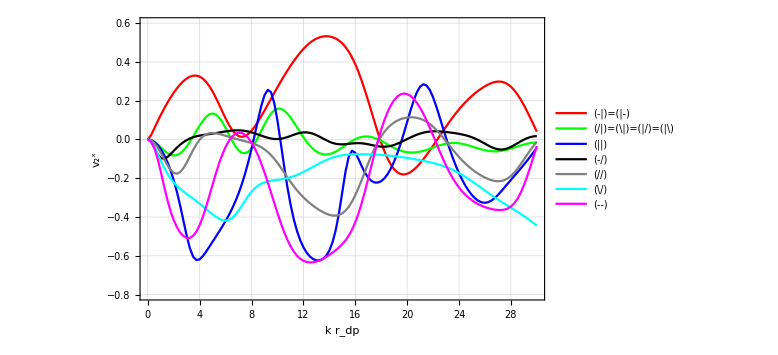

```mathematica
ListLinePlot[{Readv2x[phA0],Readv2x[phApio4],Readv2x[phApio2],Readv2x[phA0phBpio4],Readv2x[phApio4phBpio4],Readv2x[phA3pio4phBpio4],Readv2x[phA0phB0]},PlotRange->{{0,30},{-0.8,0.6}},GridLines->Automatic,PlotStyle->{{ -Graphics-},{ -Graphics-},{ -Graphics- },{ -Graphics-},{-Graphics-},{ -Graphics-},{ -Graphics-},{ -Graphics-},{-Graphics-},{-Graphics-}},PlotLegends->Placed[LineLegend[{"(-|)=(|-)","(/|)=(\|)=(|/)=(|\)","(||)","(-/)","(//)","(\/)","(--)"},LegendLayout->{"Column",3}],{0.42,0.85}],Joined->{True,True,True,True,True,True},ImageSize->Large,InterpolationOrder->1,Frame->True,FrameLabel->{"k r_dp","v_2^x"}]
```

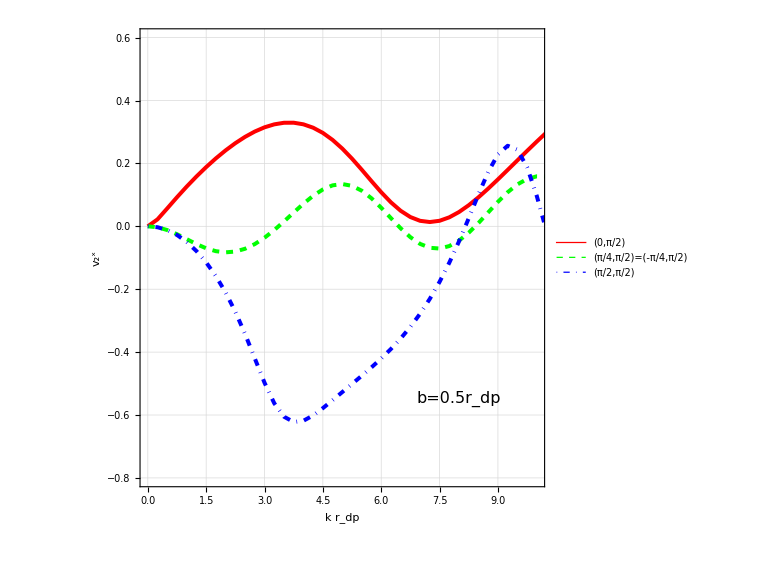

```mathematica
thick=0.005;
lp=ListLinePlot[{Readv2x[phA0],Readv2x[phApio4],Readv2x[phApio2]},PlotRange->{{0,10},{-0.8,0.6}},GridLines->Automatic,PlotStyle->{{ -Graphics-,Solid,Thickness[thick]},{ -Graphics-,Dashed,Thickness[thick]},{ -Graphics- ,DotDashed,Thickness[thick]},{ -Graphics-},{-Graphics-},{ -Graphics-},{ -Graphics-},{ -Graphics-},{-Graphics-},{-Graphics-}},PlotLegends->Placed[LineLegend[{Style["(0,π/2)",fsize],Style["(π/4,π/2)=(-π/4,π/2)",fsize],Style["(π/2,π/2)","(-/)",fsize]},LegendLayout->{"Column",1}],{0.7,0.9}],Joined->{True,True,True,True,True,True},ImageSize->Large,AspectRatio->1,InterpolationOrder->1,FrameLabel->{"k r_dp","v_2^x"},FrameStyle->Directive[FontSize->fsize],Frame->True];
text = Graphics[Text[Style["b=0.5r_dp",FontSize->fsize],{8,-0.55}]];
b05phii=Show[{lp,text}]
```

```mathematica
Export["v2b05.pdf",b05phii]
```

v2b05.pdf

#### r_dp only

```mathematica
v2b05rdp1:={{0.0,{0,0,0}},{0.2,{-0.8450619140785403+0. ⅈ,251.92518948215837,-0.003354416109860219+0. ⅈ}},{0.30000000000000004,{-0.8591146914453338+0. ⅈ,110.02676036510726,-0.007808234002296267+0. ⅈ}},{0.4,{-0.7435963712879634+0. ⅈ,60.752296859839866,-0.01223980671880598+0. ⅈ}},{0.5,{-0.6077730002264161+0. ⅈ,38.289006613954164,-0.01587330291313741+0. ⅈ}},{0.6,{-0.6306940471104658+0. ⅈ,25.34139009357965,-0.024887902549207627+0. ⅈ}},{0.7000000000000001,{-0.6008765052506944+0. ⅈ,18.633411316358313,-0.03224726246037319+0. ⅈ}},{0.8,{-0.5790789692819629+0. ⅈ,13.658932073021896,-0.04239562552812723+0. ⅈ}},{0.9,{-0.5223805312329703+0. ⅈ,10.679168319589838,-0.04891584396836567+0. ⅈ}},{1.,{-0.4912233791641175+0. ⅈ,8.644308974606883,-0.05682621718024105+0. ⅈ}},{1.1,{-0.44689561302359904+0. ⅈ,7.021302001765713,-0.06364853881961123+0. ⅈ}},{1.2000000000000002,{-0.4145611715346497+0. ⅈ,5.803523848474406,-0.07143266442225907+0. ⅈ}},{1.3000000000000003,{-0.3971748295270319+0. ⅈ,4.827178763852315,-0.08227887322119137+0. ⅈ}},{1.4000000000000001,{-0.3562602613390731+0. ⅈ,4.149531888414664,-0.08585553043555064+0. ⅈ}},{1.5000000000000002,{-0.32641961549207077+0. ⅈ,3.563306681238521,-0.09160581580326255+0. ⅈ}},{1.6,{-0.2900626842871774+0. ⅈ,3.174697743512554,-0.09136702379932579+0. ⅈ}},{1.7000000000000002,{-0.2730290421827045+0. ⅈ,2.7522720747877365,-0.09920132703586776+0. ⅈ}},{1.8000000000000003,{-0.24417017482231163+0. ⅈ,2.412205160400101,-0.10122280593322845+0. ⅈ}},{1.9000000000000001,{-0.2211071569445541+0. ⅈ,2.179686218872751,-0.10143990223459877+0. ⅈ}},{2.,{-0.19723069754225558+0. ⅈ,1.94214367517021,-0.10155309314331251+0. ⅈ}},{2.1,{-0.1810999629783065+0. ⅈ,1.7661651433450927,-0.10253852175754394+0. ⅈ}},{2.2,{-0.15829974561030224+0. ⅈ,1.6061584580020905,-0.09855798773877653+0. ⅈ}},{2.3000000000000003,{-0.14353779712164463+0. ⅈ,1.459687562983781,-0.09833460307645267+0. ⅈ}},{2.4000000000000004,{-0.12742840980401235+0. ⅈ,1.337022208843663,-0.09530762388324131+0. ⅈ}},{2.5000000000000004,{-0.11161067708462516+0. ⅈ,1.230270629360037,-0.09072042721419993+0. ⅈ}},{2.6,{-0.09665037225357395+0. ⅈ,1.1150971992781336,-0.0866743924351539+0. ⅈ}},{2.7,{-0.08435197808181398+0. ⅈ,1.0238036985872807,-0.08239077295599637+0. ⅈ}},{2.8000000000000003,{-0.07590489213992957+0. ⅈ,0.9473891524658349,-0.08012007731180655+0. ⅈ}},{2.9000000000000004,{-0.06634440509717689+0. ⅈ,0.8784505784821942,-0.07552434561749412+0. ⅈ}},{3.0000000000000004,{-0.057254607862488614+0. ⅈ,0.8020462425787227,-0.07138566933298604+0. ⅈ}},{3.1,{-0.0498523264275038+0. ⅈ,0.7546264722014294,-0.06606225498831549+0. ⅈ}},{3.2,{-0.04264957145171227+0. ⅈ,0.689209270116799,-0.061881888855738296+0. ⅈ}},{3.3000000000000003,{-0.03725822898993197+0. ⅈ,0.6377484280610057,-0.05842151442569753+0. ⅈ}},{3.4000000000000004,{-0.03140676477220597+0. ⅈ,0.5925238792290113,-0.05300506169147524+0. ⅈ}},{3.5000000000000004,{-0.026574201126851098+0. ⅈ,0.5593912862621765,-0.047505568605507836+0. ⅈ}},{3.6,{-0.022435057579845458+0. ⅈ,0.5220232840835166,-0.04297712049230385+0. ⅈ}},{3.7,{-0.019526063420887366+0. ⅈ,0.4851809032481749,-0.04024491337182657+0. ⅈ}},{3.8000000000000003,{-0.015832916272430306+0. ⅈ,0.455001017447107,-0.034797540368733025+0. ⅈ}},{3.9000000000000004,{-0.013943294501109746+0. ⅈ,0.4268763892316454,-0.03266354113940789+0. ⅈ}},{4.,{-0.010932042897742585+0. ⅈ,0.3942644782030124,-0.027727689158224187+0. ⅈ}},{4.1,{-0.009498760548669417+0. ⅈ,0.37167209392006806,-0.025556830076977007+0. ⅈ}},{4.2,{-0.0078060860363375695+0. ⅈ,0.3451169703276188,-0.022618667603993132+0. ⅈ}},{4.3,{-0.00693290779150708+0. ⅈ,0.3277058117457872,-0.021155889041373416+0. ⅈ}},{4.3999999999999995,{-0.005069803608512689+0. ⅈ,0.3072846857818175,-0.016498718755260135+0. ⅈ}},{4.5,{-0.004433422151792887+0. ⅈ,0.2866267670143371,-0.01546757896331129+0. ⅈ}},{4.6,{-0.0036796285781021823+0. ⅈ,0.26977418481870363,-0.013639661558332586+0. ⅈ}},{4.7,{-0.00362348284193046+0. ⅈ,0.2535560880581286,-0.014290656042539053+0. ⅈ}},{4.8,{-0.0031524039970179706+0. ⅈ,0.24248257303025483,-0.013000538379410223+0. ⅈ}},{4.9,{-0.0028278379217244972+0. ⅈ,0.22914341246707917,-0.012340908653137783+0. ⅈ}},{5.,{-0.0025880652432973853+0. ⅈ,0.21632997359377965,-0.011963507415561403+0. ⅈ}},{5.1,{-0.0021809461495141307+0. ⅈ,0.20344538839490034,-0.010720056948554551+0. ⅈ}},{5.2,{-0.0020982496111140946+0. ⅈ,0.1917674417763643,-0.010941636347013667+0. ⅈ}},{5.3,{-0.0020083095027239512+0. ⅈ,0.18432998787903843,-0.010895185996767113+0. ⅈ}},{5.4,{-0.0018620301591558322+0. ⅈ,0.17342016148848244,-0.010737103132495339+0. ⅈ}},{5.5,{-0.0018548927874468264+0. ⅈ,0.16461219685300632,-0.011268258506404536+0. ⅈ}},{5.6,{-0.001645203558731068+0. ⅈ,0.1560787289101388,-0.01054085697787994+0. ⅈ}},{5.7,{-0.0017494457359345482+0. ⅈ,0.14815343885787197,-0.011808337014794803+0. ⅈ}},{5.8,{-0.0018074371065629142+0. ⅈ,0.13986202226069838,-0.012923001379129988+0. ⅈ}},{5.9,{-0.0015404328405923878+0. ⅈ,0.13408283439905705,-0.011488665551384116+0. ⅈ}},{6.,{-0.0015012476937422844+0. ⅈ,0.1295889464749655,-0.011584689393491608+0. ⅈ}},{6.1,{-0.0015445168452532052+0. ⅈ,0.12092225114970415,-0.012772809227154253+0. ⅈ}},{6.2,{-0.0016024354437923448+0. ⅈ,0.11587958460061926,-0.01382845347017046+0. ⅈ}},{6.3,{-0.0014893183271967292+0. ⅈ,0.1108894061102079,-0.013430663752645261+0. ⅈ}},{6.4,{-0.0014688743039304197+0. ⅈ,0.10571939812462379,-0.013894085002251774+0. ⅈ}},{6.5,{-0.001330098301716536+0. ⅈ,0.10168979036179852,-0.013079959128485034+0. ⅈ}},{6.6,{-0.0012456865969357471+0. ⅈ,0.0976133984023443,-0.012761430472907604+0. ⅈ}},{6.7,{-0.0009558919619808755+0. ⅈ,0.09263341998681335,-0.010319083135621568+0. ⅈ}},{6.8,{-0.0010298142621351408+0. ⅈ,0.08865230970760787,-0.01161632748804474+0. ⅈ}},{6.9,{-0.0007642245465868918+0. ⅈ,0.08452704330546981,-0.009041183941866784+0. ⅈ}},{7.,{-0.0008219953768556189+0. ⅈ,0.0797955381093697,-0.01030126992475409+0. ⅈ}},{7.1,{-0.0006058322437372102+0. ⅈ,0.07616665721772391,-0.00795403482137107+0. ⅈ}},{7.2,{-0.0005080187764810636+0. ⅈ,0.07344366777017926,-0.00691712154233312+0. ⅈ}},{7.3,{-0.00033628960754362525+0. ⅈ,0.06923529175728398,-0.004857199255006325+0. ⅈ}},{7.4,{-0.0003396622357396039+0. ⅈ,0.0662947170412431,-0.00512351890013037+0. ⅈ}},{7.5,{-0.0001571431977419058+0. ⅈ,0.06404621475975035,-0.0024535907130714923+0. ⅈ}},{7.6,{-0.00010362972511875193+0. ⅈ,0.060705150552874544,-0.001707099384071041+0. ⅈ}},{7.7,{-0.00003736309577809108+0. ⅈ,0.0584126890125444,-0.0006396400578317355+0. ⅈ}},{7.8,{0.00013462619455226413,0.05513011301001866,0.0024419720403583943}},{7.9,{0.00022037623270948316,0.052456213524862155,0.004201146401942138}},{8.,{0.0002891460046198786,0.05018123870432003,0.005762034020794039}},{8.1,{0.0003421868556727075,0.04799742558333346,0.007129275195783164}},{8.2,{0.0004526654866298238,0.045818342977378246,0.009879569124822279}},{8.3,{0.0005072116093674186,0.044247031930122305,0.011463178144207256}},{8.4,{0.00047184304315994545,0.041222011044166805,0.011446385831452889}},{8.5,{0.0006159847116960232,0.03973408388946762,0.015502678088906518}},{8.6,{0.0005950701588531117,0.03782081882052021,0.015733931136632295}},{8.7,{0.000639735135584994,0.03593244374301748,0.017803830436924}},{8.8,{0.0006873597638225392,0.03438229812727382,0.019991675986233443}},{8.9,{0.0006484097159013809,0.03308850115774182,0.01959622506955624}},{9.,{0.0006573699526199431,0.0317125207988047,0.02072903496983187}},{9.1,{0.0006417857126662784,0.029895040983573325,0.021467965640820687}},{9.2,{0.0006511791436287415,0.02873744595611203,0.02265960394055984}},{9.3,{0.0006356506096057196,0.027092175321883422,0.02346251646660058}},{9.4,{0.0005757630111990249,0.026432786406327017,0.021782153509976112}},{9.5,{0.000628072305876721,0.024977755275793958,0.025145266215550938}},{9.6,{0.0005978371034711849,0.024314058098202165,0.024588125151983175}},{9.700000000000001,{0.0005517239698880905,0.023064197359146128,0.023921230004100007}},{9.8,{0.0005310424160771779,0.022057906429160515,0.024074923782210843}},{9.9,{0.00046578827384032213,0.020966950698971677,0.022215355991806986}},{10.,{0.00045402178360107057,0.02003675017797226,0.022659452234934138}}}
b05hi:=
{{1.,{-40.94470262198085,700.448947297802,-0.05845494204815024}},{1.1,{-26.66836121934872,478.72498674523683,-0.05570705928817714}},{1.2,{-17.95291678360616,338.2470924705987,-0.053076337338115245}},{1.3,{-12.602973135766934,245.75862991361106,-0.051281914861737}},{1.4,{-8.862885594105478,182.85766673584442,-0.048468766731606466}},{1.5,{-6.33320735993966,138.87452048655328,-0.04560381081965919}},{1.6,{-4.586213793847289,107.37134300301962,-0.0427135738976303}},{1.7000000000000002,{-3.358297824390614,84.32786690433952,-0.03982429471624398}},{1.8,{-2.5676698237801507,67.15719146470273,-0.038233728477607594}},{1.9000000000000001,{-1.918879688692357,55.85154795156776,-0.034356786142370366}},{2.,{-1.4459056275784854,45.48030082914704,-0.03179190993063628}},{2.1,{-1.1440221791683187,37.41007275785452,-0.030580592199680307}},{2.2,{-0.8744869360557491,31.054929507430103,-0.028159359880257407}},{2.3000000000000003,{-0.665353361148805,25.99578554107693,-0.025594662646276058}},{2.4000000000000004,{-0.5102401515292303,21.928256368748144,-0.023268614838725513}},{2.5000000000000004,{-0.39879404031120846,18.628149480059434,-0.021408140445624987}},{2.6,{-0.31258498734372286,15.928207371408902,-0.019624618141575196}},{2.7,{-0.24640269385817265,13.702170099817918,-0.017982749598287866}},{2.8,{-0.1959497732969217,11.85368513179647,-0.016530705102947577}},{2.9,{-0.1574555565498646,10.308480489591972,-0.015274371107249093}},{3.,{-0.1280794511599126,9.008768395440823,-0.014217198793203666}},{3.1,{-0.10363006306816508,7.909195040315332,-0.013102479144835128}},{3.2,{-0.08678697043681176,6.973876145874005,-0.01244458155285107}},{3.3000000000000003,{-0.0739786151944723,6.174204350099039,-0.011981886409912173}},{3.4000000000000004,{-0.06424710420842561,5.4872114807727534,-0.011708516144046596}},{3.5000000000000004,{-0.05685516949917689,4.894334001135644,-0.01161652831334859}},{3.6,{-0.052355025279592404,4.380474315561827,-0.011951907831898223}},{3.7,{-0.04795027357045209,3.933281219849635,-0.012190909037591057}},{3.8000000000000003,{-0.0445545238859036,3.542594103194342,-0.012576807443372914}},{3.9000000000000004,{-0.04190523920379504,3.200010526916043,-0.013095344171939496}},{4.,{-0.03953093267052015,2.8985474890240757,-0.013638186995456124}},{4.1,{-0.037985000708335354,2.6323743566097773,-0.014429938740649358}},{4.2,{-0.0366421282270842,2.396601007957017,-0.015289206716273474}},{4.3,{-0.03538316494087128,2.1871087892787155,-0.016178054385918433}},{4.4,{-0.034363960799026885,2.0004148840565747,-0.01717841687387436}},{4.5,{-0.031394389080995705,1.8335629147125472,-0.017122068094356877}},{4.6,{-0.030488139333963722,1.684034257543184,-0.01810422751045604}},{4.699999999999999,{-0.029601065499131322,1.5496758025324056,-0.019101456866499875}},{4.800000000000001,{-0.026999082310720915,1.428640837488494,-0.018898439413354905}},{4.9,{-0.026390999240555022,1.3193404587886324,-0.020003175878337137}},{5.,{-0.025529616482021993,1.2204034655839084,-0.020918997038251782}},{5.1,{-0.024627338905755136,1.1306431222377271,-0.021781708499684336}},{5.2,{-0.022796311828539147,1.049029505782375,-0.021730858572502655}},{5.3,{-0.02189100149052798,0.9449147092173915,-0.023167171890740072}},{5.4,{-0.020952952652232737,0.8781991011000411,-0.02385900034056839}},{5.5,{-0.019989333591999257,0.8172320913534876,-0.024459800102677346}},{5.6000000000000005,{-0.01900747349903422,0.7614192964575082,-0.024963214863960245}},{5.7,{-0.018014622397793275,0.7102377122254679,-0.025364215512220584}},{5.800000000000001,{-0.017017772522048856,0.6632261180882667,-0.025659080753789032}},{5.9,{-0.01602352886425754,0.6199769001169629,-0.02584536433733997}},{6.,{-0.015038019003444132,0.58012906324498,-0.02592185076770373}},{6.1,{-0.014066834207702154,0.5433622434855803,-0.025888501411996726}},{6.2,{-0.013114995320541572,0.5093915636590051,-0.02574639286590337}},{6.3,{-0.012196925204796606,0.47796320277898835,-0.025518544385594682}},{6.4,{-0.011297695095524791,0.4488505710058362,-0.025170281214542317}},{6.5,{-0.010429121566977192,0.4218509999052799,-0.024722287180352517}},{6.6000000000000005,{-0.009593965533704658,0.39678287241384064,-0.02417938424443444}},{6.7,{-0.008794461273336914,0.3734831290037611,-0.023547144677714075}},{6.800000000000001,{-0.008032349001164887,0.35180509654374664,-0.02283181534343142}},{6.9,{-0.007308910466934478,0.3316165946510333,-0.02204024341612273}},{7.,{-0.006735241408720371,0.3127982812353675,-0.02153222000491872}},{7.1,{-0.006084954862582731,0.29524220469655904,-0.020610044112211744}},{7.2,{-0.0054752616851490915,0.27885053505686225,-0.01963511271022878}},{7.3,{-0.004905950296104293,0.2635344503521585,-0.01861597331790405}},{7.4,{-0.004376541199388786,0.24921315800584942,-0.017561437102314083}},{7.5,{-0.0038863212348073674,0.23581303377616258,-0.016480519217170687}},{7.6000000000000005,{-0.0034343760165855613,0.22326686329099,-0.015382381272179392}},{7.7,{-0.0030196203554567784,0.21151317323829782,-0.014276275606034113}},{7.800000000000001,{-0.0026464505469775998,0.20049564102534434,-0.013199541563315416}},{7.9,{-0.0023017572845874545,0.1901625732066569,-0.012104155122501669}},{8.,{-0.0019901925083792367,0.1804664442505372,-0.01102804743920316}},{8.1,{-0.0017102392288745496,0.17136348830128267,-0.009980184494538843}},{8.2,{-0.0014603317859075587,0.16281333752800842,-0.00896936214243714}},{8.299999999999999,{-0.0013203182174070646,0.1547787014548453,-0.008530361122019431}},{8.4,{-0.0011221426688383142,0.14722508236131007,-0.007621953072401248}},{8.5,{-0.0009392976340230528,0.14012052244246348,-0.006703497943413312}},{8.600000000000001,{-0.000755820099185902,0.1334353789400973,-0.0056643156049731745}},{8.700000000000001,{-0.0006320341867780679,0.127142123910287,-0.004971084069855862}},{8.8,{-0.0006777061022240349,0.12121516568910332,-0.005590934916198837}},{8.9,{-0.000586850171452952,0.11563068946534535,-0.0050752112105050765}},{9.,{-0.0005138563330234999,0.11036651467381894,-0.00465590794945522}},{9.1,{-0.0005616843818612898,0.10540196719083084,-0.005328974371458905}},{9.200000000000001,{-0.0005152543926416945,0.10071776455014222,-0.0051158243527652525}},{9.3,{-0.0004826202845231416,0.09629591260685536,-0.005011846001122831}},{9.4,{-0.0004866841215672088,0.09211961226211612,-0.005283175966724688}},{9.5,{-0.00047655264045288136,0.09083321911581828,-0.005246457684663203}},{9.6,{-0.00047099264582786964,0.0869585215246281,-0.005416290865691371}},{9.700000000000001,{-0.00047879126766379207,0.08329887058751269,-0.005747872261494594}},{9.8,{-0.0004951133678157129,0.07984049585899133,-0.006201281223129517}},{9.9,{-0.0005179958145411141,0.07657048924941277,-0.0067649536997713075}},{10.,{-0.0005444025407787489,0.07347675491848311,-0.0074091805140649196}}}
```

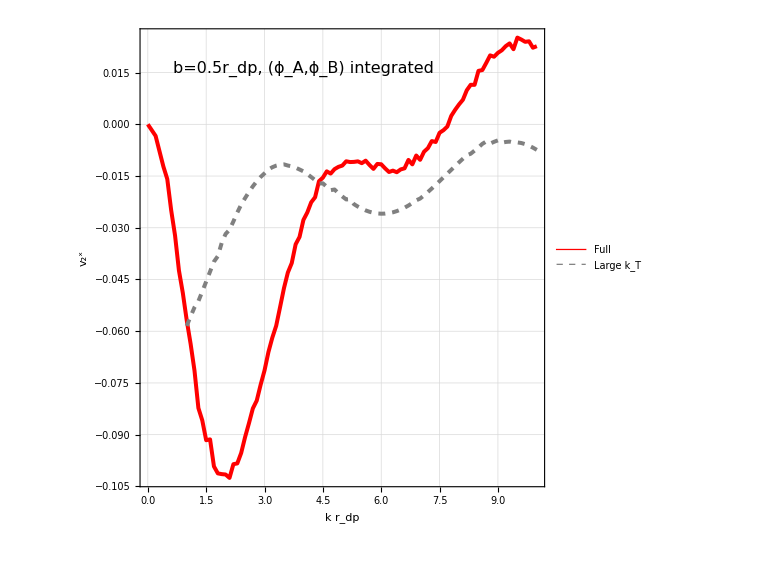

```mathematica
thick=0.005;fsize=16;
lp=ListLinePlot[{Readv2x[v2b05rdp1,3],Readv2x[b05hi,3]},GridLines->Automatic,PlotStyle->{{ -Graphics-,Solid,Thickness[thick]},{ Gray,Dashed,Thickness[thick]},{ -Graphics- ,DotDashed,Thickness[thick]},{ -Graphics-},{-Graphics-},{ -Graphics-},{ -Graphics-},{ -Graphics-},{-Graphics-},{-Graphics-}},Joined->{True,True,True,True,True,True},ImageSize->Large,AspectRatio->1,InterpolationOrder->1,FrameLabel->{"k r_dp","v_2^x"},FrameStyle->Directive[FontSize->fsize],Frame->True,PlotRange->{{0,10},Full},PlotLegends->Placed[LineLegend[{Style["Full",fsize],Style["Large k_T",fsize]},LegendLayout->{"Column",1}],{0.8,0.2}]
];
text = Graphics[Text[Style["b=0.5r_dp, (ϕ_A,ϕ_B) integrated",FontSize->fsize],{4.0,0.016}]];
b05=Show[{lp,text}]
```

```mathematica
Export["v2b05rdp.pdf",b05]
```

v2b05rdp.pdf

```mathematica
v2b20rdp1:={{0.0,{0,0,0}},{0.2,{-0.049759645999870074+0. ⅈ,5.141028871155737,-0.009678927554570177+0. ⅈ}},{0.30000000000000004,{-0.043109288418374477+0. ⅈ,2.3705949159762474,-0.0181850083824302+0. ⅈ}},{0.4,{-0.04102884909059704+0. ⅈ,1.400394824511739,-0.029298058213619964+0. ⅈ}},{0.5,{-0.023512473718450902+0. ⅈ,0.9233672193089782,-0.025463838467264376+0. ⅈ}},{0.6,{-0.00801521096135522+0. ⅈ,0.6474896904623982,-0.01237890128510191+0. ⅈ}},{0.7000000000000001,{0.000299000346101716,0.5005442663247694,0.0005973504567280665}},{0.8,{0.006475692109977335,0.38877042197558237,0.016656853875534946}},{0.9,{0.009008577851039028,0.29877753529901435,0.030151456474206834}},{1.,{0.011149568883841289,0.2447279387235673,0.04555903564584547}},{1.1,{0.011777476952687476,0.1982512278862224,0.05940682980004866}},{1.2000000000000002,{0.011175354728183255,0.15524711669510213,0.07198429810539486}},{1.3000000000000003,{0.00950882901601347,0.12999661185992334,0.07314674498024319}},{1.4000000000000004,{0.008044372189941364,0.10929332813216143,0.07360350652158583}},{1.5000000000000002,{0.0057670712126042635,0.09191848945540695,0.06274114432006721}},{1.6000000000000003,{0.0033921417151054323,0.08046797104945319,0.04215517889746125}},{1.7000000000000002,{0.0014191760832087915,0.06947737941886788,0.020426448076759036}},{1.8000000000000003,{-0.00026695564429995137+0. ⅈ,0.06349676839093805,-0.004204239854481318+0. ⅈ}},{1.9000000000000001,{-0.0022793792788883055+0. ⅈ,0.05691488116257079,-0.04004891571990674+0. ⅈ}},{2.,{-0.0034935541632762634+0. ⅈ,0.05344431589859957,-0.06536811454195837+0. ⅈ}},{2.1,{-0.004672582146653646+0. ⅈ,0.05104844248204687,-0.09153231557058646+0. ⅈ}},{2.2,{-0.005286323535411542+0. ⅈ,0.046608050798278566,-0.11342082418960092+0. ⅈ}},{2.3000000000000003,{-0.006115730971144422+0. ⅈ,0.04476538173498935,-0.1366174202947602+0. ⅈ}},{2.4000000000000004,{-0.006461783474579244+0. ⅈ,0.042123312723053426,-0.15340159775807025+0. ⅈ}},{2.5000000000000004,{-0.006676403284346525+0. ⅈ,0.03974461401094738,-0.16798259211946442+0. ⅈ}},{2.6000000000000005,{-0.006854608700778127+0. ⅈ,0.03848548528153341,-0.1781089325140248+0. ⅈ}},{2.7,{-0.006779171556284989+0. ⅈ,0.0372226052264879,-0.18212512302768313+0. ⅈ}},{2.8000000000000003,{-0.0070344868720341154+0. ⅈ,0.0351531974231568,-0.20010944630033062+0. ⅈ}},{2.9000000000000004,{-0.006774214518738454+0. ⅈ,0.034517535122416294,-0.19625429494643026+0. ⅈ}},{3.0000000000000004,{-0.0064362373867013385+0. ⅈ,0.032301281591992345,-0.1992564093276384+0. ⅈ}},{3.1,{-0.006133272774198585+0. ⅈ,0.030557969544909455,-0.2007094340867391+0. ⅈ}},{3.2,{-0.006026717829866887+0. ⅈ,0.02825451056885111,-0.21330108745578413+0. ⅈ}},{3.3000000000000003,{-0.005628269994239278+0. ⅈ,0.026888560356267726,-0.20931838371656547+0. ⅈ}},{3.4000000000000004,{-0.005383959245146063+0. ⅈ,0.02527352908974394,-0.21302759998527024+0. ⅈ}},{3.5000000000000004,{-0.005290306356517956+0. ⅈ,0.02330675442336089,-0.22698597412668325+0. ⅈ}},{3.6000000000000005,{-0.005152788402395531+0. ⅈ,0.02124720101051182,-0.24251610364331025+0. ⅈ}},{3.7,{-0.004787794426116425+0. ⅈ,0.019654960393378614,-0.24359216860743932+0. ⅈ}},{3.8000000000000003,{-0.004572214839312645+0. ⅈ,0.018079601099161617,-0.2528935685159927+0. ⅈ}},{3.9000000000000004,{-0.004388842186038781+0. ⅈ,0.0164961291521125,-0.26605285067598683+0. ⅈ}},{4.,{-0.004185822255785997+0. ⅈ,0.01508623344678172,-0.2774597297961699+0. ⅈ}},{4.1,{-0.004089820092011745+0. ⅈ,0.013302831785385156,-0.3074398111614799+0. ⅈ}},{4.199999999999999,{-0.003809695505548297+0. ⅈ,0.011865315742605666,-0.32107830825508854+0. ⅈ}},{4.3,{-0.0036005897230653146+0. ⅈ,0.01082488526277006,-0.33262151382322674+0. ⅈ}},{4.3999999999999995,{-0.0032994798457308796+0. ⅈ,0.009629185187476238,-0.3426541063954402+0. ⅈ}},{4.5,{-0.003108779714110773+0. ⅈ,0.008729641171905254,-0.35611769749664046+0. ⅈ}},{4.6,{-0.0029299918056137782+0. ⅈ,0.007720154285047484,-0.37952503245804714+0. ⅈ}},{4.7,{-0.0027296197260959425+0. ⅈ,0.006869394104965367,-0.39735960470267767+0. ⅈ}},{4.8,{-0.002468922489882132+0. ⅈ,0.006193711819118573,-0.39861759183905404+0. ⅈ}},{4.9,{-0.002279195752720308+0. ⅈ,0.005446860478451831,-0.41844210288421546+0. ⅈ}},{5.,{-0.0021043432588265507+0. ⅈ,0.004966178664306873,-0.4237349078781588+0. ⅈ}},{5.1,{-0.0019508108914071771+0. ⅈ,0.004384345687313196,-0.44494915103345056+0. ⅈ}},{5.199999999999999,{-0.0017272141104819603+0. ⅈ,0.003916989016018858,-0.44095454529445244+0. ⅈ}},{5.3,{-0.001604436978028959+0. ⅈ,0.003580470743597208,-0.44810783076446026+0. ⅈ}},{5.3999999999999995,{-0.0013933708232432643+0. ⅈ,0.0031827834140933852,-0.43778373893536376+0. ⅈ}},{5.5,{-0.0012498342604531406+0. ⅈ,0.002878681540521628,-0.43416899120653196+0. ⅈ}},{5.6,{-0.0011387750349536193+0. ⅈ,0.0026281770471150477,-0.4332946428413769+0. ⅈ}},{5.7,{-0.0010156913867295744+0. ⅈ,0.0023661479725308543,-0.4292594539821536+0. ⅈ}},{5.8,{-0.0009035226222432336+0. ⅈ,0.0021855227841229685,-0.4134125843056857+0. ⅈ}},{5.9,{-0.0007924636303426934+0. ⅈ,0.0019773717365679936,-0.4007661360216088+0. ⅈ}},{6.,{-0.0006977449446781043+0. ⅈ,0.001789010530526627,-0.39001723733437765+0. ⅈ}},{6.1,{-0.000626203623994845+0. ⅈ,0.0016546501270590956,-0.3784507756378882+0. ⅈ}},{6.199999999999999,{-0.0005455312170749013+0. ⅈ,0.0015348760825193188,-0.35542362232883057+0. ⅈ}},{6.3,{-0.0004941337453360255+0. ⅈ,0.0014136660785104471,-0.3495406396513983+0. ⅈ}},{6.3999999999999995,{-0.00043512762994891757+0. ⅈ,0.0013080497610996886,-0.3326537283895851+0. ⅈ}},{6.5,{-0.0003839303039570079+0. ⅈ,0.001199791443175466,-0.3199975346889178+0. ⅈ}},{6.6,{-0.0003432239828257064+0. ⅈ,0.0011022620154741403,-0.3113814846264732+0. ⅈ}},{6.7,{-0.0003190270828499152+0. ⅈ,0.0010275948449586095,-0.31045998762553667+0. ⅈ}},{6.8,{-0.0002767039490154731+0. ⅈ,0.0009391110654797961,-0.2946445411907736+0. ⅈ}},{6.9,{-0.0002520392297829464+0. ⅈ,0.0008769158459765936,-0.28741552674562315+0. ⅈ}},{7.,{-0.00021753208705009154+0. ⅈ,0.0008056297852453054,-0.27001495107812507+0. ⅈ}},{7.1,{-0.00019576649220672267+0. ⅈ,0.0007718138785819495,-0.25364469030591114+0. ⅈ}},{7.199999999999999,{-0.0001757936846054158+0. ⅈ,0.0007217954234752009,-0.243550566944618+0. ⅈ}},{7.3,{-0.0001518110405173513+0. ⅈ,0.0006851007494586603,-0.2215893657061482+0. ⅈ}},{7.3999999999999995,{-0.00013914625880719113+0. ⅈ,0.0006382147263852648,-0.21802420573290576+0. ⅈ}},{7.5,{-0.0001208635649199725+0. ⅈ,0.0006101688901106052,-0.1980821488589226+0. ⅈ}},{7.6,{-0.00010839916038911177+0. ⅈ,0.0005688349079038949,-0.1905634813948969+0. ⅈ}},{7.7,{-0.00010053996306345672+0. ⅈ,0.0005395486298072245,-0.1863408736657874+0. ⅈ}},{7.8,{-0.0000916454972035602+0. ⅈ,0.0005112636766271906,-0.17925290098476404+0. ⅈ}},{7.9,{-0.00007481664256220907+0. ⅈ,0.0005036837330323815,-0.14853892960128445+0. ⅈ}},{8.,{-0.00007105506162876075+0. ⅈ,0.0004788474075455,-0.14838769200605748+0. ⅈ}},{8.1,{-0.00006030781984681383+0. ⅈ,0.0004613681577509375,-0.13071517579540043+0. ⅈ}},{8.2,{-0.00005466695504510265+0. ⅈ,0.0004444923545055212,-0.12298739110128745+0. ⅈ}},{8.3,{-0.000048264256389223055+0. ⅈ,0.00043468138768627986,-0.1110336392504032+0. ⅈ}},{8.4,{-0.000042031446704536904+0. ⅈ,0.00041853271476427196,-0.10042571398082958+0. ⅈ}},{8.5,{-0.00003509074590746102+0. ⅈ,0.00039954669568632016,-0.08782639497789863+0. ⅈ}},{8.6,{-0.000030491118861330006+0. ⅈ,0.00039582813013963017,-0.07703120758641921+0. ⅈ}},{8.7,{-0.00002596075341136263+0. ⅈ,0.00038008879609585053,-0.06830181178193916+0. ⅈ}},{8.799999999999999,{-0.000019939924307633243+0. ⅈ,0.00037073928380436616,-0.053784222980144875+0. ⅈ}},{8.9,{-0.000017749918082743332+0. ⅈ,0.0003590604502877501,-0.04943434474200262+0. ⅈ}},{9.,{-0.000013385447780801004+0. ⅈ,0.0003530057591207702,-0.03791849689404524+0. ⅈ}},{9.1,{-0.000012535094216232597+0. ⅈ,0.00034603421509779667,-0.03622501379723364+0. ⅈ}},{9.2,{-9.573914622115674*^-6+0. ⅈ,0.00033376023555606093,-0.028685006786878197+0. ⅈ}},{9.3,{-7.710719086222195*^-6+0. ⅈ,0.0003201176541711948,-0.024087141042519956+0. ⅈ}},{9.4,{-6.006080449615849*^-6+0. ⅈ,0.0003141445195986696,-0.01911884522858722+0. ⅈ}},{9.5,{-5.036376258113557*^-6+0. ⅈ,0.00030088091509695975,-0.016738769411448282+0. ⅈ}},{9.6,{-5.487693927909284*^-6+0. ⅈ,0.000297137592098424,-0.018468527960916966+0. ⅈ}},{9.700000000000001,{-3.902457259165611*^-6+0. ⅈ,0.0002858905065512477,-0.013650181344745249+0. ⅈ}},{9.8,{-2.704455248003935*^-6+0. ⅈ,0.000273170684273847,-0.009900239680524371+0. ⅈ}},{9.9,{-1.617573879221421*^-6+0. ⅈ,0.00026895411434317085,-0.0060143117095337855+0. ⅈ}},{10.,{-4.4555802404283256*^-6+0. ⅈ,0.0002514044024760016,-0.017722761401736564+0. ⅈ}}}
b20hi:={{1.,{-0.005100552815327652,1.106589387958551,-0.0046092551318761615}},{1.1,{-0.008003161593502166,0.7970951332811449,-0.01004040955633254}},{1.2,{-0.00954041808765973,0.5946548646923839,-0.016043622366723607}},{1.3,{-0.010139247033556124,0.4568532294298915,-0.022193663917422495}},{1.4,{-0.010091126009467696,0.35982737938911147,-0.028044352896657476}},{1.5,{-0.009602844609426484,0.28949346347355,-0.03317119666262815}},{1.6,{-0.008825593195460333,0.23719246078222275,-0.03720857385751191}},{1.7000000000000002,{-0.00787230686588567,0.19740980912281295,-0.03987799238987226}},{1.8,{-0.006828398744052043,0.1665245809061782,-0.04100535012244973}},{1.9000000000000001,{-0.005758649423408447,0.14209514766597114,-0.04052671409262714}},{2.,{-0.004711802913984436,0.12243658932969792,-0.038483617844796925}},{2.1,{-0.0037237697101731807,0.10636254487281126,-0.03501015996398055}},{2.2,{-0.002819972134772938,0.09302311361382953,-0.030314746789487156}},{2.3000000000000003,{-0.002017153005092096,0.0818003181956741,-0.02465947626593426}},{2.4000000000000004,{-0.0013248450101701077,0.07223910294238799,-0.0183397212341728}},{2.5000000000000004,{-0.0007466193924505426,0.06400077522959219,-0.011665786699804323}},{2.6,{-0.0002811845694156454,0.05683094600929019,-0.00494773691378778}},{2.7,{0.00007662502773102825,0.050537019382153256,0.0015162158090804968}},{2.8,{0.0003349493784578296,0.04497211535211065,0.007447934699876411}},{2.9,{0.0005040833447872366,0.04002339702051405,0.012594716648586026}},{3.,{0.0005957355326736955,0.03560347611849303,0.016732510350703108}},{3.1,{0.0006223672562665781,0.03164400059399983,0.01966778045076223}},{3.2,{0.0005966149123164484,0.028090853140826762,0.021238760863739613}},{3.3000000000000003,{0.0005307986800563468,0.02490049123261586,0.021316795524141355}},{3.4000000000000004,{0.00043651947878863874,0.022037194705552838,0.019808305214031912}},{3.5,{0.0003243444340042953,0.019470954012289567,0.01665786041092683}},{3.6,{0.00020357848179099533,0.017175928173287315,0.01185254617608431}},{3.7,{0.00008211820987341054,0.015129234146271212,0.0054277836590723655}},{3.8000000000000003,{-0.00003361842653025116,0.01331013630672687,-0.0025257762772317055}},{3.9000000000000004,{-0.00013869453527527693,0.011699423612588768,-0.011854817798548585}},{4.,{-0.00022959829459733263,0.010279027630491575,-0.022336577237739415}},{4.1,{-0.00030413894389600706,0.009031763178517045,-0.03367437098211699}},{4.2,{-0.0003613057093726528,0.00794119789617264,-0.04549763324079717}},{4.300000000000001,{-0.0004011007437760204,0.006991602923811143,-0.057368925001447205}},{4.4,{-0.0004243565541636787,0.0061679637382329,-0.06880010521677536}},{4.5,{-0.0004325480318312782,0.005456021978246186,-0.0792790119900358}},{4.6,{-0.00042760771413189683,0.004842356520570083,-0.08830570659459731}},{4.7,{-0.00041175191239431995,0.004314441597482999,-0.09543573672072227}},{4.800000000000001,{-0.00038732355558321037,0.0038606969618770874,-0.10032477539881607}},{4.9,{-0.000356656347354207,0.0034705788402571774,-0.10276566641194008}},{5.,{-0.0003219629615990587,0.0031345844634578027,-0.10271312365400324}},{5.1000000000000005,{-0.00028524865721395095,0.0028442715347142614,-0.10028882746689209}},{5.2,{-0.0002482503238273473,0.0025922466914094244,-0.09576647340318205}},{5.3,{-0.00021239961742588193,0.0023721318826433763,-0.08953954836153342}},{5.4,{-0.0001788080868555402,0.002178511444928611,-0.08207810304223565}},{5.5,{-0.00014827126689462026,0.0020068623119033767,-0.0738821323292452}},{5.6000000000000005,{-0.00012128833369160616,0.0018534704493797305,-0.06543850414890384}},{5.7,{-0.00009809359728278945,0.0017153410303722997,-0.05718606128222742}},{5.800000000000001,{-0.0000786961454362263,0.0015901005779668494,-0.04949130044141583}},{5.9,{-0.00006292406027634195,0.001475900955542601,-0.042634338056383}},{6.,{-0.00005047000477080703,0.001371324430686151,-0.03680383988022006}},{6.1000000000000005,{-0.000040935403199165096,0.0012752963060123869,-0.03209873894104065}},{6.2,{-0.00003387102797809133,0.001187004490139527,-0.028534877719047166}},{6.300000000000001,{-0.000028812297648162046,0.0011058290070567836,-0.026054930250787457}},{6.4,{-0.00002530825932815475,0.0010312830082425935,-0.02454055688484821}},{6.5,{-0.000022943757953189294,0.0009629647026370567,-0.02382616713817063}},{6.6000000000000005,{-0.000021354729720986452,0.0009005198843397473,-0.023713779220592715}},{6.7,{-0.00002023709545634761,0.0008436155616206858,-0.02398852792315702}},{6.800000000000001,{-0.00001934992183511638,0.0007919218952489122,-0.024434129111980705}},{6.9,{-0.000018513883571461873,0.0007451022509299466,-0.02484744013100897}},{7.,{-0.000017606029739569308,0.0007028093883023562,-0.025050931351524582}},{7.1000000000000005,{-0.000016552067670913883,0.0006646872479299234,-0.02490203884979441}},{7.2,{-0.000015317197498298957,0.0006303735047788938,-0.024298606115546576}},{7.300000000000001,{-0.000013896502731974963,0.0005995071130058868,-0.02317987965530362}},{7.4,{-0.000012305702230657795,0.0005717342933785926,-0.021523463561961238}},{7.5,{-0.000010572920212219598,0.0005467150363749376,-0.019338996568165873}},{7.6000000000000005,{-8.731880500293218*^-6,0.0005241285754563447,-0.016659806217759837}},{7.7,{-6.816780958985106*^-6,0.0005036774629952921,-0.013534020201036518}},{7.800000000000001,{-4.858884166649311*^-6,0.00048509000843740147,-0.010016458970781556}},{7.9,{-2.8847245580478023*^-6,0.00046812129360009465,-0.006162344241730129}},{8.,{-9.15704384848371*^-7,0.00045255226875009943,-0.0020234223714698145}},{8.100000000000001,{1.0312356130342081*^-6,0.0004381888456798978,0.0023534045268407814}},{8.2,{2.9422230008790143*^-6,0.00042485782485912653,0.006925194332609011}},{8.3,{4.804700534202556*^-6,0.0004124058376639256,0.011650418338932348}},{8.4,{6.605648718105152*^-6,0.0004006949001315856,0.016485482385565426}},{8.5,{8.330069491236213*^-6,0.0003895997518919141,0.021381095472430403}},{8.600000000000001,{9.959944699968212*^-6,0.00037900628562538287,0.026279101634247865}},{8.7,{0.000011473800525832533,0.00036880896315137233,0.031110416698639932}},{8.8,{0.00001284693704982147,0.0003589103047216725,0.03579428308636612}},{8.9,{0.000014052282242738016,0.0003492205572888964,0.04023898922740999}},{9.,{0.000015061792191575458,0.0003396580928699465,0.04434398151479508}},{9.1,{0.000015848233530882743,0.00033015031846960136,0.04800308418403653}},{9.200000000000001,{0.000016387188156682764,0.00032063502285597687,0.05110854082850324}},{9.3,{0.000016659065616127163,0.00031106143735611303,0.05355554760410669}},{9.4,{0.00001665094805335921,0.0003013917145751454,0.05524686727646477}},{9.5,{0.00001635808745175251,0.0002916018884023243,0.056097330306665194}},{9.6,{0.00001578492950975228,0.00028168236501562987,0.05603804664476036}},{9.700000000000001,{0.000014945549999200995,0.0002716378739744537,0.055020125803983265}},{9.8,{0.000013863516236705364,0.00026148691243559253,0.053018011905739716}},{9.9,{0.000012571093060333879,0.0002512605162386947,0.050032107107475174}},{10.,{0.000011107937297676699,0.00024100046785513918,0.046090936654751516}}}
```

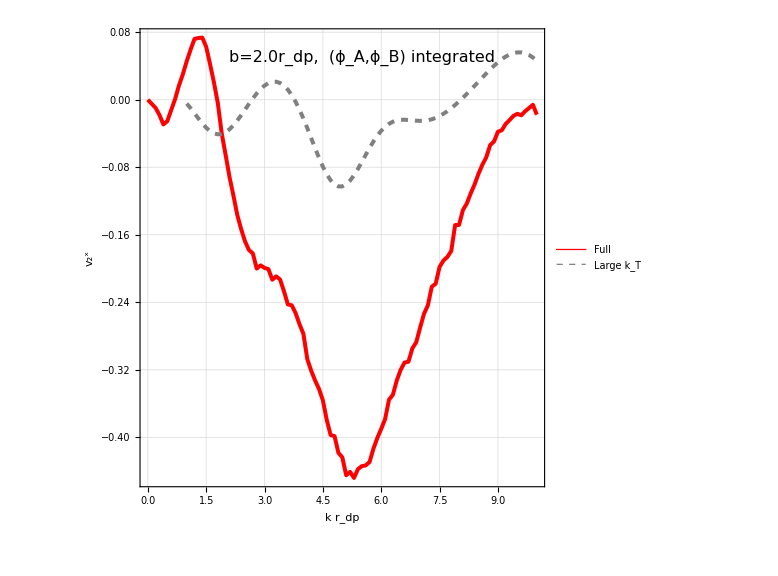

```mathematica
thick=0.005;fsize=16;
lp=ListLinePlot[{Readv2x[v2b20rdp1,3],Readv2x[b20hi,3]},GridLines->Automatic,PlotStyle->{{ -Graphics-,Solid,Thickness[thick]},{ Gray,Dashed,Thickness[thick]},{ -Graphics- ,DotDashed,Thickness[thick]},{ -Graphics-},{-Graphics-},{ -Graphics-},{ -Graphics-},{ -Graphics-},{-Graphics-},{-Graphics-}},Joined->{True,True,True,True,True,True},ImageSize->Large,AspectRatio->1,InterpolationOrder->1,FrameLabel->{"k r_dp","v_2^x"},FrameStyle->Directive[FontSize->fsize],Frame->True,PlotRange->{{0,10},Full},PlotLegends->Placed[LineLegend[{Style["Full",fsize],Style["Large k_T",fsize]},LegendLayout->{"Column",1}],{0.85,0.2}]];
text = Graphics[Text[Style["b=2.0r_dp,  (ϕ_A,ϕ_B) integrated",FontSize->fsize],{5.5,0.05}]];
b20=Show[{lp,text}]
```

```mathematica
Export["v2b20rdp.pdf",b20]
```

v2b20rdp.pdf